# Savage 1803.03326

```mathematica
SetDirectory[NotebookDirectory[]]; (* by default, files are saved in the same directory as the notebook *)
imageRes = 250; (* image resolution for exporting images *)
```

## Lattice, Configuration, and Hamiltonian

Define a 1D lattice with periodic boundary conditions

```mathematica
L=4; (* number of spatial sites *)
nfs =2 L; (* number of fermion sites *)
```

```mathematica
ClearAll[fs]; 
fs[n_]:=Mod[n, nfs];
```

```mathematica
fs[nfs] == fs[0] (* check PBC *)
fs[-1] == fs[nfs-1]
```

True

True

```mathematica
lattice = Table[fs[n], {n, 0, nfs-1}]
```

{0,1,2,3,4,5,6,7}

Define the parameters of the model

```mathematica
ClearAll[a, g,w, J,m, m0, w0, J0];
a = 1.;
w0 = 1/(2a); (* fix that! a = 1 *)
(* Relevant dimless parameters are wrt w0 *)
j0w0 = 1.667;
m0w0 = 0.167;
w0t0 = 0.1;
(* the rest is determined *)
J0 = j0w0 w0;
m0 = m0w0 w0 ; 
t0 = w0t0 / w0;
g = 2 √(J0 w0); 
params = {J-> J0, w-> w0, m->m0};
```

```mathematica
(* Relate to the parameters from Savage's paper *)
```

```mathematica
x = 1/(a g)^2
μ = (2 m0)/(a g^2)
```

0.59988

0.10018

Define Truncation Parameters

```mathematica
Λ1 =1;   (* primary cutoff - absolute value of each link should not exceed this *)
Λ2 = 4; (* secondary cutoff - sum of squares of all links should not exceed this *)
Λ3 = 3; (* secondary cutoff for the building the smart operator *)
```

Define a Hamiltonian

```mathematica
Hhop = Sum[w SubPlus[σ][fs[n]].SubPlus[U][fs[n]].SubMinus[σ][fs[n+1]].Ket[Ψ] +w SubPlus[σ][fs[n+1]].SubMinus[U][fs[n]].SubMinus[σ][fs[n]].Ket[Ψ] ,{n,0, nfs-1}] ;
HoldForm[Sum[w SubPlus[σ][fs[n]].SubPlus[U][fs[n]].SubMinus[σ][fs[n+1]].Ket[Ψ] +w SubPlus[σ][fs[n+1]].SubMinus[U][fs[n]].SubMinus[σ][fs[n]].Ket[Ψ] ,{n,0, nfs-1}] ;]
```

∑_(n=0)^(nfs-1) (w σ_+[fs[n]].U_+[fs[n]].σ_-[fs[n+1]].Ψ+w σ_+[fs[n+1]].U_-[fs[n]].σ_-[fs[n]].Ψ);

```mathematica
Hmass = Sum[m/2(-1)^n Subscript[σ, z][fs[n]].Ket[Ψ],{n,0, nfs-1}] ;
HoldForm[ Sum[m/2(-1)^n Subscript[σ, z][fs[n]].Ket[Ψ],{n,0, nfs-1}] ]
```

∑_(n=0)^(nfs-1) 1/2 m (-1)^n σ_z[fs[n]].Ψ

```mathematica
Hfield = Sum[J l[fs[n]].l[fs[n]].Ket[Ψ],{n,0, nfs-1}] ;
HoldForm[Sum[J l[fs[n]].l[fs[n]].Ket[Ψ],{n,0, nfs-1}]]
```

∑_(n=0)^(nfs-1) J l[fs[n]].l[fs[n]].Ψ

```mathematica
H =  Simplify[Hhop + Hmass + Hfield];
```

### Define hopping operator for readability

```mathematica
(* helper functions to determine the direction of hopping on a lattice with PBC *)
```

```mathematica
ClearAll[isLeft, isRight]
(* 
given two integers a and b and a 0/1 checkLeft, 
checks if jumping FROM a TO b corresponds hopping 
	- to the LEFT by 1 site if checkLeft is 1
	- to the RIGHT by 1 site if checkLeft is 0
*)
indexDiff[a_, b_, checkLeft_]/; checkLeft == 1 ∨ checkLeft ==0:=If[Quotient[b-a, nfs] ≥0,Mod[b-a, nfs]==(-1)^checkLeft, (b-a)-(Quotient[b-a, nfs]+1)*nfs == (-1)^checkLeft];
(* checks hopping LEFT *)
(* when indices are not yet specified *)
isLeft[i_ +a_Integer, i_+b_Integer]/;fs[Abs[b-a]]==1:=indexDiff[a, b, 1];
isLeft[i_, i_+a_Integer]/;fs[Abs[a]]==1:=indexDiff[0, a, 1];
isLeft[i_+a_Integer, i_]/;fs[Abs[a]]==1:=indexDiff[a, 0, 1];
(* when indices are specified *)
isLeft[i_Integer, j_Integer]/; Min[fs[i-j], nfs - fs[i-j]]==1:=(i-j)==1 ∨(i==0 ∧ j == nfs-1);
(* checks hopping RIGHT *)
(* when indices are not yet specified *)
isRight[i_ +a_Integer, i_+b_Integer]/;fs[Abs[b-a]]==1:=indexDiff[a, b, 0];
isRight[i_, i_+a_Integer]/;fs[Abs[a]]==1:=indexDiff[0, a, 0];
isRight[i_+a_Integer, i_]/;fs[Abs[a]]==1:=indexDiff[a, 0, 0];
(* when indices are specified *)
isRight[i_Integer, j_Integer]/; Min[fs[i-j], nfs - fs[i-j]]==1:=(i-j)==-1 ∨(i==nfs-1 ∧ j == 0);
```

```mathematica
ClearAll[hop]
hop[i_, j_ ]/; Min[fs[i-j], nfs - fs[i-j]]==1 := If[isLeft[i, j],SubPlus[χ][fs[j]].SubPlus[U][fs[j]].SubMinus[χ][fs[i]], SubPlus[χ][fs[j]].SubMinus[U][fs[i]].SubMinus[χ][fs[i]]];
```

```mathematica
hoppingReplacement = {α-> hop};
```

Define a basis in the required subspace

```mathematica
singleSpinBasis = {1,-1}; 
singleLinkBasis = Table[l, {l, -Λ1, Λ1}];
```

```mathematica
spinKets = Ket @@@ Select[Tuples[singleSpinBasis, nfs], Total[#]== 0 &]; (* choose subspace with Q = 0 *)
```

```mathematica
(* impose second cutoff on the sum of the squares of the links *)
```

```mathematica
linkKets =Ket @@@ Select[Tuples[singleLinkBasis, nfs], Total[#^2] ≤ Λ2&];
```

```mathematica
ClearAll[singleSpinBasis, singleLinkBasis] (* to free up some memory *)
```

```mathematica
(*basisNoGauss = Flatten @ Outer [Join, spinKets, linkKets];*)
```

```mathematica
(*Length[basisNoGauss]*)
```

```mathematica
(* This takes a while, can be improved by solving with the constraint, not filtering on it *)
```

```mathematica
basisGauss= Flatten @ 
Parallelize[Outer [
If[(* for all n, | L[n] - L[n-1] - 1/2(Subscript[σ, z][n] + (-1)^n) | must be 0 *)
AllTrue[Range[0, nfs-1], Function[n,Abs[#2⟦fs[n]+1⟧ - #2⟦fs[n-1]+1⟧ - 1/2(#1⟦fs[n]+1⟧ + (-1)^n) ]==0]],
Join[#1,#2],Nothing] &, 
spinKets, linkKets]];
```

```mathematica
(* Save / Load from File if Basis was Already Computed *)
```

```mathematica
(*Export["gauss_12.txt", List@Delete[0]@#&/@basisGauss, "Table"]*)
```

```mathematica
(*basisGauss= Ket@Delete[0]@#&/@Import["gauss_12.txt", "Table"];*)
```

```mathematica
Length[basisGauss]
```

79

```mathematica
basics = {
before___.(n_ b_).after___/;NumericQ[n]:> n before.b.after,
before___.(a_+b_).after___:> before.a.after+before.b.after,
a___ +0.+b___ :>a+b,
Dot[x_,0]:>0};
```

```mathematica
normalization={
(* all kets are normalized *)
psi1_Ket.psi2_Ket :> Boole[List[Delete[0]@psi1]==List[Delete[0]@psi2]],
0.`.psi_Ket :> 0};
```

```mathematica
(* AD-HOC GENERALLY WRONG USED JUST TO CHECK THE ANALYTIC FORF OF THE MATRICES 
(x_ psi1_Ket).psi2_Ket :>x psi1.psi2,
psi1_Ket.(y_ psi2_Ket) :>y psi1.psi2,
(x_ psi1_Ket).(y_ psi2_Ket) :>x y psi1.psi2,
x_(psi_Ket + a___):>x psi + x a,
x_(n_ psi_Ket + a___)/;NumericQ[n]:>n x psi + x a *)
```

```mathematica
rules = Join[basics,normalization];
```

Define a translation operator (translates by one spatial site)

```mathematica
translation = {
(* break into spins and links, and shift each separately by an integer number of spatial sites *)
T[n_].psi_Ket:> Flatten[RotateRight[Partition[psi, nfs], {0,Mod[2 n, nfs]}]],
T[n_].(x_ psi_Ket):>x T[n].psi/;NumericQ[x]};
```

```mathematica
rules = Join[basics,normalization, translation];
```

Get all momentum sectors

```mathematica
getKSector[k_Integer]:=DeleteDuplicates[Table[Simplify[sum/Sqrt[sum.sum]/.sum-> Sum[T[n].basisKet Exp[ⅈ 2π k/L], {n, 0, L-1}] //. rules],{basisKet,basisGauss}]];
```

```mathematica
k0Sector= getKSector[0];
```

#### We will work with the k=0 sector

```mathematica
Length[k0Sector]
```

23

Define a parity operator

```mathematica
parity = {
(* this permutation fixes points 0 and nfs/2 on the lattice and reflects points along the axis through these points; links are permuted and reversed; fixing any other pair of diametric points yields the same states *)
P.psi_Ket:> Ket @@ MapThread[
Times,
(* remove Ket from the head to perform normal list operations *)
{List[Delete[0]@
Permute[psi, 
Cycles[Join[
(* these permutations reflect lattice points across the axis through sites 0 and nfs/2*)
Table[{n+1,nfs-n +1},{n, 1, nfs/2-1}],
(* these permutations reflect links across the axis through sites 0 and nfs/2; directions are not flipped yet *)
Table[{n+1 + nfs,nfs-n + nfs}, {n, 0,nfs/2-1}]]]]],
(* flip directions on all of the links once everything is permuted *)
Join[ones, -ones]/.ones ->Table[1,{i, nfs}]}] ,
P.(x_ psi_Ket):>x P.psi/;NumericQ[x]};
```

```mathematica
rules = Join[basics,normalization, translation, parity];
```

Within the zero momentum sector, form states of good parity

```mathematica
getPSector[n_Integer, k0Sector_] := 
DeleteDuplicatesBy[DeleteCases[
(* delete any repeated states as defined below *)
ParallelTable[Expand[PAIRity/(Sqrt[PAIRity.PAIRity])/.PAIRity
(* add or subtract parity-transformed state to get one of the sectors *)
->Simplify[(kVec +(-1)^n (P.kVec//. rules))//.rules]//.rules],{kVec,k0Sector}],
(* delete any zeroes *)
0],
(* delete any states that are the same / same up to a sign *)
(* this version is faster than pairwise comparison! *)
Sort[{#,(-1)^n#}]&];
```

```mathematica
evenPSector = getPSector[0, k0Sector];
```

```mathematica
Length[evenPSector]
```

13

```mathematica
oddPSector = getPSector[1, k0Sector];
```

```mathematica
Length[oddPSector]
```

10

```mathematica
evenPSectorTable = SortBy[
ParallelTable[
{(* print the result of Hfield acting on the ket *)
N[(1/J) * Hfield/.Ket[Ψ]->evenPSector⟦i⟧/.params//.rules].evenPSector⟦i⟧//.rules,
(* print the actual ket expansion converted to fermionic sites *)
S.evenPSector[[i]]//. rules}, {i, Length[evenPSector]}],
Abs[#⟦1⟧] &]; 
evenPSectorTableForm = Grid[Select[Simplify[evenPSectorTable],#⟦1⟧ ≤ Λ2 &], ItemSize->{{1.5, 60},{3, 3}}, Frame-> All]
```

0 | 0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0
1. | 1/(2 √2)(0,0,1,1,0,1,0,1,0,-1,0,0,0,0,0,0+0,1,0,0,1,1,0,1,0,0,0,-1,0,0,0,0+0,1,0,1,0,0,1,1,0,0,0,0,0,-1,0,0+0,1,0,1,0,1,1,0,0,0,0,0,0,0,1,0+0,1,0,1,1,0,0,1,0,0,0,0,1,0,0,0+0,1,1,0,0,1,0,1,0,0,1,0,0,0,0,0+1,0,0,1,0,1,0,1,1,0,0,0,0,0,0,0+1,1,0,1,0,1,0,0,0,0,0,0,0,0,0,-1)
2. | 1/(2 √2)(0,0,1,0,1,1,0,1,0,-1,0,-1,0,0,0,0+0,1,0,0,1,0,1,1,0,0,0,-1,0,-1,0,0+0,1,0,1,1,0,1,0,0,0,0,0,1,0,1,0+0,1,1,0,1,0,0,1,0,0,1,0,1,0,0,0+1,0,0,1,0,1,1,0,1,0,0,0,0,0,1,0+1,0,1,0,0,1,0,1,1,0,1,0,0,0,0,0+1,0,1,1,0,1,0,0,0,-1,0,0,0,0,0,-1+1,1,0,1,0,0,1,0,0,0,0,0,0,-1,0,-1)
2. | 1/2 (0,0,1,1,0,0,1,1,0,-1,0,0,0,-1,0,0+0,1,1,0,0,1,1,0,0,0,1,0,0,0,1,0+1,0,0,1,1,0,0,1,1,0,0,0,1,0,0,0+1,1,0,0,1,1,0,0,0,0,0,-1,0,0,0,-1)
2. | 1/2 (0,0,1,1,0,1,1,0,0,-1,0,0,0,0,1,0+0,1,1,0,0,0,1,1,0,0,1,0,0,-1,0,0+1,0,0,0,1,1,0,1,1,0,0,-1,0,0,0,0+1,1,0,1,1,0,0,0,0,0,0,0,1,0,0,-1)
2. | 1/2 (0,0,1,1,1,0,0,1,0,-1,0,0,1,0,0,0+0,1,0,0,1,1,1,0,0,0,0,-1,0,0,1,0+1,0,0,1,0,0,1,1,1,0,0,0,0,-1,0,0+1,1,1,0,0,1,0,0,0,0,1,0,0,0,0,-1)
3. | 1/(2 √2)(0,0,1,0,1,0,1,1,0,-1,0,-1,0,-1,0,0+0,1,1,0,1,0,1,0,0,0,1,0,1,0,1,0+1,0,0,1,1,0,1,0,1,0,0,0,1,0,1,0+1,0,1,0,0,1,1,0,1,0,1,0,0,0,1,0+1,0,1,0,1,0,0,1,1,0,1,0,1,0,0,0+1,0,1,0,1,1,0,0,0,-1,0,-1,0,0,0,-1+1,0,1,1,0,0,1,0,0,-1,0,0,0,-1,0,-1+1,1,0,0,1,0,1,0,0,0,0,-1,0,-1,0,-1)
3. | 1/(2 √2)(0,0,0,1,0,1,1,1,1,0,0,0,0,0,1,1+0,0,0,1,1,1,0,1,0,-1,-1,-1,0,0,0,0+0,1,0,0,0,1,1,1,0,0,0,-1,-1,-1,0,0+0,1,0,1,1,1,0,0,0,0,0,0,1,1,1,0+0,1,1,1,0,0,0,1,0,0,1,1,1,0,0,0+0,1,1,1,0,1,0,0,-1,-1,0,0,0,0,0,-1+1,1,0,0,0,1,0,1,1,1,1,0,0,0,0,0+1,1,0,1,0,0,0,1,0,0,0,0,0,-1,-1,-1)
3. | 1/(2 √2)(0,0,1,0,1,1,1,0,0,-1,0,-1,0,0,1,0+0,0,1,1,1,0,1,0,0,-1,0,0,1,0,1,0+1,0,0,0,1,0,1,1,1,0,0,-1,0,-1,0,0+1,0,0,0,1,1,1,0,1,0,0,-1,0,0,1,0+1,0,1,0,0,0,1,1,1,0,1,0,0,-1,0,0+1,0,1,1,1,0,0,0,0,-1,0,0,1,0,0,-1+1,1,1,0,0,0,1,0,0,0,1,0,0,-1,0,-1+1,1,1,0,1,0,0,0,0,0,1,0,1,0,0,-1)
4. | 1/(2 √2)(0,0,0,1,1,0,1,1,0,-1,-1,-1,0,-1,0,0+0,0,0,1,1,0,1,1,1,0,0,0,1,0,1,1+0,1,1,0,1,1,0,0,-1,-1,0,-1,0,0,0,-1+0,1,1,0,1,1,0,0,0,0,1,0,1,1,1,0+1,0,1,1,0,0,0,1,0,-1,0,0,0,-1,-1,-1+1,0,1,1,0,0,0,1,1,0,1,1,1,0,0,0+1,1,0,0,0,1,1,0,0,0,0,-1,-1,-1,0,-1+1,1,0,0,0,1,1,0,1,1,1,0,0,0,1,0)
4. | 1/(2 √2)(0,0,1,0,0,1,1,1,0,-1,0,-1,-1,-1,0,0+0,0,1,0,0,1,1,1,1,0,1,0,0,0,1,1+0,1,1,1,0,0,1,0,-1,-1,0,0,0,-1,0,-1+0,1,1,1,0,0,1,0,0,0,1,1,1,0,1,0+1,0,0,1,1,1,0,0,0,-1,-1,-1,0,0,0,-1+1,0,0,1,1,1,0,0,1,0,0,0,1,1,1,0+1,1,0,0,1,0,0,1,0,0,0,-1,0,-1,-1,-1+1,1,0,0,1,0,0,1,1,1,1,0,1,0,0,0)
4. | 1/(2 √2)(0,0,0,0,1,1,1,1,1,0,0,-1,0,0,1,1+0,0,0,1,1,1,1,0,0,-1,-1,-1,0,0,1,0+0,0,1,1,1,1,0,0,0,-1,0,0,1,1,1,0+0,1,1,1,1,0,0,0,-1,-1,0,0,1,0,0,-1+1,0,0,0,0,1,1,1,1,0,0,-1,-1,-1,0,0+1,1,0,0,0,0,1,1,1,1,1,0,0,-1,0,0+1,1,1,0,0,0,0,1,0,0,1,0,0,-1,-1,-1+1,1,1,1,0,0,0,0,0,0,1,1,1,0,0,-1)
4. | (1,0,1,0,1,0,1,0,0,-1,0,-1,0,-1,0,-1+1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0)/(√2)

```mathematica
Export[StringJoin["~/Desktop/report/evenPSector_L4.png"],
evenPSectorTableForm, 
ImageResolution->imageRes]
```

~/Desktop/report/evenPSector_L4.png

```mathematica
oddPSectorTable = SortBy[
ParallelTable[
{(* print the result of Hfield acting on the ket *)
N[(1/J) * Hfield/.Ket[Ψ]->oddPSector⟦i⟧/.params//.rules].oddPSector⟦i⟧//.rules,
(* print the actual ket expansion converted to fermionic sites *)
S.oddPSector[[i]]//. rules}, {i, Length[oddPSector]}],
Abs[#⟦1⟧] &]; 
oddPSectorTableForm = Grid[Select[Simplify[oddPSectorTable],#⟦1⟧ ≤ Λ2 &], ItemSize->{{1.5, 60},{3, 3}}, Frame-> All]
```

1. | 1/(2 √2)(0,0,1,1,0,1,0,1,0,-1,0,0,0,0,0,0+0,1,0,0,1,1,0,1,0,0,0,-1,0,0,0,0+0,1,0,1,0,0,1,1,0,0,0,0,0,-1,0,0-0,1,0,1,0,1,1,0,0,0,0,0,0,0,1,0-0,1,0,1,1,0,0,1,0,0,0,0,1,0,0,0-0,1,1,0,0,1,0,1,0,0,1,0,0,0,0,0-1,0,0,1,0,1,0,1,1,0,0,0,0,0,0,0+1,1,0,1,0,1,0,0,0,0,0,0,0,0,0,-1)
2. | 1/(2 √2)(0,0,1,0,1,1,0,1,0,-1,0,-1,0,0,0,0+0,1,0,0,1,0,1,1,0,0,0,-1,0,-1,0,0-0,1,0,1,1,0,1,0,0,0,0,0,1,0,1,0-0,1,1,0,1,0,0,1,0,0,1,0,1,0,0,0-1,0,0,1,0,1,1,0,1,0,0,0,0,0,1,0-1,0,1,0,0,1,0,1,1,0,1,0,0,0,0,0+1,0,1,1,0,1,0,0,0,-1,0,0,0,0,0,-1+1,1,0,1,0,0,1,0,0,0,0,0,0,-1,0,-1)
2. | 1/2 (0,0,1,1,0,0,1,1,0,-1,0,0,0,-1,0,0-0,1,1,0,0,1,1,0,0,0,1,0,0,0,1,0-1,0,0,1,1,0,0,1,1,0,0,0,1,0,0,0+1,1,0,0,1,1,0,0,0,0,0,-1,0,0,0,-1)
3. | 1/(2 √2)(0,0,1,0,1,0,1,1,0,-1,0,-1,0,-1,0,0-0,1,1,0,1,0,1,0,0,0,1,0,1,0,1,0-1,0,0,1,1,0,1,0,1,0,0,0,1,0,1,0-1,0,1,0,0,1,1,0,1,0,1,0,0,0,1,0-1,0,1,0,1,0,0,1,1,0,1,0,1,0,0,0+1,0,1,0,1,1,0,0,0,-1,0,-1,0,0,0,-1+1,0,1,1,0,0,1,0,0,-1,0,0,0,-1,0,-1+1,1,0,0,1,0,1,0,0,0,0,-1,0,-1,0,-1)
3. | 1/(2 √2)(-0,0,0,1,0,1,1,1,1,0,0,0,0,0,1,1+0,0,0,1,1,1,0,1,0,-1,-1,-1,0,0,0,0+0,1,0,0,0,1,1,1,0,0,0,-1,-1,-1,0,0-0,1,0,1,1,1,0,0,0,0,0,0,1,1,1,0-0,1,1,1,0,0,0,1,0,0,1,1,1,0,0,0+0,1,1,1,0,1,0,0,-1,-1,0,0,0,0,0,-1-1,1,0,0,0,1,0,1,1,1,1,0,0,0,0,0+1,1,0,1,0,0,0,1,0,0,0,0,0,-1,-1,-1)
3. | 1/(2 √2)(-0,0,1,0,1,1,1,0,0,-1,0,-1,0,0,1,0+0,0,1,1,1,0,1,0,0,-1,0,0,1,0,1,0-1,0,0,0,1,0,1,1,1,0,0,-1,0,-1,0,0+1,0,0,0,1,1,1,0,1,0,0,-1,0,0,1,0+1,0,1,0,0,0,1,1,1,0,1,0,0,-1,0,0-1,0,1,1,1,0,0,0,0,-1,0,0,1,0,0,-1-1,1,1,0,0,0,1,0,0,0,1,0,0,-1,0,-1+1,1,1,0,1,0,0,0,0,0,1,0,1,0,0,-1)
4. | 1/(2 √2)(0,0,0,1,1,0,1,1,0,-1,-1,-1,0,-1,0,0-0,0,0,1,1,0,1,1,1,0,0,0,1,0,1,1+0,1,1,0,1,1,0,0,-1,-1,0,-1,0,0,0,-1-0,1,1,0,1,1,0,0,0,0,1,0,1,1,1,0+1,0,1,1,0,0,0,1,0,-1,0,0,0,-1,-1,-1-1,0,1,1,0,0,0,1,1,0,1,1,1,0,0,0+1,1,0,0,0,1,1,0,0,0,0,-1,-1,-1,0,-1-1,1,0,0,0,1,1,0,1,1,1,0,0,0,1,0)
4. | 1/(2 √2)(0,0,1,0,0,1,1,1,0,-1,0,-1,-1,-1,0,0-0,0,1,0,0,1,1,1,1,0,1,0,0,0,1,1+0,1,1,1,0,0,1,0,-1,-1,0,0,0,-1,0,-1-0,1,1,1,0,0,1,0,0,0,1,1,1,0,1,0+1,0,0,1,1,1,0,0,0,-1,-1,-1,0,0,0,-1-1,0,0,1,1,1,0,0,1,0,0,0,1,1,1,0+1,1,0,0,1,0,0,1,0,0,0,-1,0,-1,-1,-1-1,1,0,0,1,0,0,1,1,1,1,0,1,0,0,0)
4. | 1/(2 √2)(0,0,0,0,1,1,1,1,1,0,0,-1,0,0,1,1-0,0,0,1,1,1,1,0,0,-1,-1,-1,0,0,1,0+0,0,1,1,1,1,0,0,0,-1,0,0,1,1,1,0-0,1,1,1,1,0,0,0,-1,-1,0,0,1,0,0,-1-1,0,0,0,0,1,1,1,1,0,0,-1,-1,-1,0,0+1,1,0,0,0,0,1,1,1,1,1,0,0,-1,0,0-1,1,1,0,0,0,0,1,0,0,1,0,0,-1,-1,-1+1,1,1,1,0,0,0,0,0,0,1,1,1,0,0,-1)
4. | (1,0,1,0,1,0,1,0,0,-1,0,-1,0,-1,0,-1-1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0)/(√2)

```mathematica
Export[StringJoin["~/Desktop/report/oddPSector_L4.png"],
oddPSectorTableForm, 
ImageResolution->imageRes]
```

~/Desktop/report/oddPSector_L4.png

Define the rules on how the Hamiltonian acts on the basis elements

```mathematica
operators={Dot[anything_,0]->0,             (* needed to have something like Subscript[σ, z][1].Subscript[σ, z][1].Ket[0]] :> 0 *)
a___ +0.+b___ :>a+b,
Subscript[σ, z][n_].psi_Ket:>psi[[n + 1]]psi,
Subscript[σ, z][n_].(x_ psi_Ket):>x Subscript[σ, z][n].psi/;NumericQ[x],
SubPlus[σ][n_].psi_Ket :>If[psi[[n + 1]] == 1,0,ReplacePart[psi, n + 1->psi[[n+ 1]] + 2]],
SubPlus[σ][n_].(x_ psi_Ket):>x SubPlus[σ][n].psi/;NumericQ[x],
SubMinus[σ][n_].psi_Ket :>If[psi[[n + 1]] == -1,0,ReplacePart[psi, n+ 1->psi[[n + 1]]-2]],
SubMinus[σ][n_].(x_ psi_Ket):>x SubMinus[σ][n].psi/;NumericQ[x],
SubMinus[U][n_].psi_Ket :> If[psi[[n+nfs+ 1]] == -Λ1,0,ReplacePart[psi, n+nfs + 1->psi[[n + nfs + 1]]-1]],
SubMinus[U][n_].(x_ psi_Ket):>x SubMinus[U][n].psi/;NumericQ[x],
SubPlus[U][n_].psi_Ket :> If[psi[[n+nfs+ 1]] == Λ1,0,ReplacePart[psi, n+nfs + 1->psi[[n + nfs + 1]]+1]],
SubPlus[U][n_].(x_ psi_Ket):>x SubPlus[U][n].psi/;NumericQ[x],
l[n_].psi_Ket:>psi[[n +nfs+ 1]]psi,
l[n_].(x_ psi_Ket):>x l[n].psi/;NumericQ[x]};
```

```mathematica
rules =Join[basics,normalization, translation, parity, operators];
```

Sort kets within each sector in the ascending order of electric field energy

```mathematica
(* IMPLEMENT SORTING BY SMART OPERATORS LATER; THIS WILL FIX THE PROBLEM OF DIFFERENT ORDERINGS AT DIFFERENT TRUNCATIONS / VOLUMES *)
```

```mathematica
evenPSector=SortBy[evenPSector, ((1/J) * Hfield/.Ket[Ψ]->#/.params//.rules).# //.rules&];
oddPSector=SortBy[oddPSector, ((1/J) * Hfield/.Ket[Ψ]->#/.params//.rules).# //.rules &];
```

Compute H Ψ

```mathematica
(* hOnBasis=Table[H/.Ket[Ψ]->basisKet//.rules,{basisKet,basisGauss}]; *)
```

```mathematica
hOnEvenPSector = Table[H/.Ket[Ψ]->basisKet//.rules,{basisKet,evenPSector}];
```

```mathematica
hOnOddPSector = Table[H/.Ket[Ψ]->basisKet//.rules,{basisKet,oddPSector}];
```

Compute < Ψ| H |Ψ >

```mathematica
(* hMatrix=CoefficientArrays[hOnBasis /.params,basisGauss][[2]] *)
```

```mathematica
(* MatrixPlot[hMatrix] *)
```

```mathematica
len = Length[evenPSector];
ctr = 0;
SetSharedVariable[ctr]
Monitor[hEvenPMatrix = 
SparseArray[
ParallelTable[ctr++;hOnEvenPSector[[i]].evenPSector[[j]]/.params//.rules//Expand,
{i, len}, {j,len}]],ProgressIndicator[ctr, {1, len^2}]];
```

```mathematica
len = Length[oddPSector];
ctr = 0;
Monitor[hOddPMatrix = 
SparseArray[
ParallelTable[ctr++;hOnOddPSector[[i]].oddPSector[[j]]/.params//.rules//Expand,
{i, len}, {j,len}]],ProgressIndicator[ctr, {1, len^2}]];
```

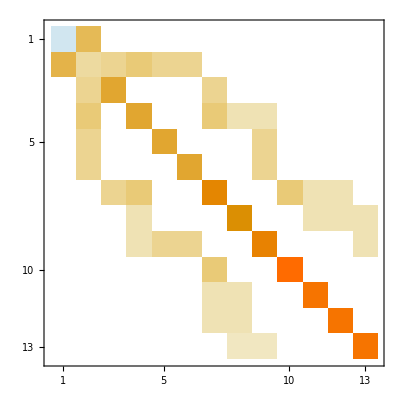

```mathematica
hEvenPMatrix//MatrixPlot
```

```mathematica
(*Export["hEvenPMatrix_12.mtx", hEvenPMatrix, "MTX"]*)
```

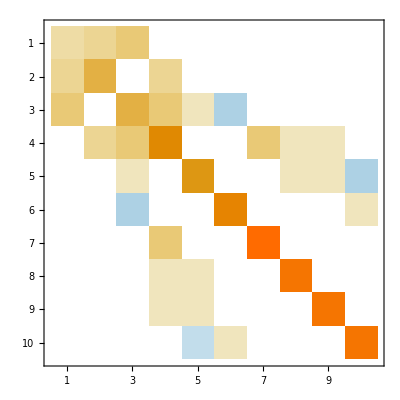

```mathematica
hOddPMatrix//MatrixPlot
```

```mathematica
(*Export["hOddPMatrix_12.mtx", hOddPMatrix, "MTX"]*)
```

## Compare the matrices numerically with those by Savage

### Even parity

```mathematica
(hEvenPMatrix/J0)//MatrixForm
```

(-0.40072 | 1.69672 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1.69672 | 0.79964 | 0.848358 | 1.19976 | 0.848358 | 0.848358 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.848358 | 2. | 0. | 0. | 0. | 0.848358 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 1.19976 | 0. | 2. | 0. | 0. | 1.19976 | 0.59988 | 0.59988 | 0. | 0. | 0. | 0.
0. | 0.848358 | 0. | 0. | 2. | 0. | 0. | 0. | 0.848358 | 0. | 0. | 0. | 0.
0. | 0.848358 | 0. | 0. | 0. | 2. | 0. | 0. | 0.848358 | 0. | 0. | 0. | 0.
0. | 0. | 0.848358 | 1.19976 | 0. | 0. | 3.20036 | 0. | 0. | 1.19976 | 0.59988 | 0.59988 | 0.
0. | 0. | 0. | 0.59988 | 0. | 0. | 0. | 2.79964 | 0. | 0. | 0.59988 | 0.59988 | 0.59988
0. | 0. | 0. | 0.59988 | 0.848358 | 0.848358 | 0. | 0. | 3.20036 | 0. | 0. | 0. | 0.59988
0. | 0. | 0. | 0. | 0. | 0. | 1.19976 | 0. | 0. | 4.40072 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.59988 | 0.59988 | 0. | 0. | 4. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.59988 | 0.59988 | 0. | 0. | 0. | 4. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.59988 | 0.59988 | 0. | 0. | 0. | 4.)

### Odd Parity

```mathematica
(hOddPMatrix/J0)//MatrixForm
```

(0.79964 | 0.848358 | 1.19976 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.848358 | 2. | 0. | 0.848358 | 0. | 0. | 0. | 0. | 0. | 0.
1.19976 | 0. | 2. | 1.19976 | 0.59988 | -0.59988 | 0. | 0. | 0. | 0.
0. | 0.848358 | 1.19976 | 3.20036 | 0. | 0. | 1.19976 | 0.59988 | 0.59988 | 0.
0. | 0. | 0.59988 | 0. | 2.79964 | 0. | 0. | 0.59988 | 0.59988 | -0.59988
0. | 0. | -0.59988 | 0. | 0. | 3.20036 | 0. | 0. | 0. | 0.59988
0. | 0. | 0. | 1.19976 | 0. | 0. | 4.40072 | 0. | 0. | 0.
0. | 0. | 0. | 0.59988 | 0.59988 | 0. | 0. | 4. | 0. | 0.
0. | 0. | 0. | 0.59988 | 0.59988 | 0. | 0. | 0. | 4. | 0.
0. | 0. | 0. | 0. | -0.59988 | 0.59988 | 0. | 0. | 0. | 4.)

## Diagonalize the Hamiltonian

Get eigen energies in both parity sectors

```mathematica
(* esystem = Normal@hMatrix//Eigensystem; *)
(* evalues=esystem[[1]]//Re; *)
```

```mathematica
esystemEvenP = Normal@hEvenPMatrix//Eigensystem ;
```

```mathematica
evaluesEvenP=esystemEvenP[[1]]//Re
```

{4.75242,3.99705,3.64898,3.334,3.33003,2.64714,2.1538,1.96622,-1.68317,1.667,1.42304,0.944926,0.157571}

```mathematica
esystemOddP = Normal@hOddPMatrix//Eigensystem;
```

```mathematica
evaluesOddP=esystemOddP[[1]]//Re
```

{4.73075,3.89757,3.53105,3.334,3.00919,2.415,2.12646,1.52746,1.18608,-0.418548}

For each eigenvector, stores coefficients of the expansion of the eigenvector in the basis specified above

```mathematica
evectorsEvenP= esystemEvenP[[2]];
evectorsOddP= esystemOddP[[2]];
```

```mathematica
Length[evectorsEvenP]
```

13

```mathematica
(* get the eigenvectors *)
evectorKetsEvenP = evenPSector.evectorsEvenP;
evectorKetsOddP = oddPSector.evectorsOddP;
```

```mathematica
E0EvenP = evaluesEvenP// Sort //First;
```

```mathematica
E0OddP = evaluesOddP // Sort // First;
```

```mathematica
E0=Min[E0EvenP, E0OddP]
```

-1.68317

```mathematica
evaluesEvenPSorted = evaluesEvenP// Sort
evaluesOddPSorted =evaluesOddP // Sort
```

{-1.68317,0.157571,0.944926,1.42304,1.667,1.96622,2.1538,2.64714,3.33003,3.334,3.64898,3.99705,4.75242}

{-0.418548,1.18608,1.52746,2.12646,2.415,3.00919,3.334,3.53105,3.89757,4.73075}

```mathematica
evaluesEvenPShifted = (evaluesEvenP - E0) // Sort 
evaluesOddPShifted = (evaluesOddP - E0) // Sort 
(* excited levels agree, but eigenvectors are not yet separated into parity / momentum sectors *)
```

{0.,1.84074,2.6281,3.10621,3.35017,3.64939,3.83697,4.33032,5.0132,5.01717,5.33215,5.68023,6.4356}

{1.26463,2.86926,3.21063,3.80963,4.09817,4.69236,5.01717,5.21422,5.58075,6.41392}

Get the rotation matrices that diagonalize the Hamiltonian

## Eigenvectors within each parity sector, ordered by the corresponding eigenvalues

```mathematica
eValVecPairEvenP= SortBy[Partition[Riffle[evaluesEvenP,evectorsEvenP],2],First[#]&];
```

```mathematica
eValVecPairOddP = SortBy[Partition[Riffle[evaluesOddP,evectorsOddP],2],First[#]&];
```

```mathematica
eValVecPairEvenP//TableForm
```

-1.68317 | 0.671533
-0.640649
0.153118
0.233051
0.151536
0.151536
-0.0848005
-0.0333133
-0.077308
0.0158471
0.0117709
0.0117709
0.0110243
0.157571 | 0.599185
0.208272
-0.254602
-0.487587
-0.202059
-0.202059
0.335214
0.16193
0.223053
-0.0954909
-0.0782552
-0.0782552
-0.0606
0.944926 | 0.180394
0.163137
0.256607
0.268715
-0.466589
-0.466589
-0.425175
-0.177317
0.313329
0.156138
0.126093
0.126093
-0.0284653
1.42304 | -0.188282
-0.233924
0.691948
-0.376424
-0.0166581
-0.0166581
-0.00480668
0.421456
0.239672
0.0021411
-0.109016
-0.109016
-0.172983
1.667 | 6.34855×10^-16
7.42589×10^-16
-7.31829×10^-16
-7.33405×10^-17
0.707107
-0.707107
-5.35114×10^-16
-2.14382×10^-15
-2.07909×10^-16
2.15637×10^-16
1.17192×10^-15
9.27472×10^-16
7.05379×10^-16
1.96622 | 0.261999
0.42614
0.355163
-0.39786
0.233388
0.233388
-0.275851
-0.211289
-0.327381
0.162095
0.178076
0.178076
0.196913
2.1538 | 0.142058
0.2499
-0.205157
0.216056
0.07056
0.07056
-0.391138
0.69415
-0.201324
0.258313
-0.128373
-0.128373
-0.208789
2.64714 | -0.096525
-0.203474
-0.358797
-0.300741
0.203609
0.203609
-0.293868
-0.0805597
0.485703
0.287864
0.272566
0.272566
-0.294926
3.33003 | -0.129535
-0.335606
-0.199578
-0.283848
-0.202045
-0.202045
-0.133777
0.134249
-0.139578
0.395819
-0.0594778
-0.0594778
0.67037
3.334 | -3.88578×10^-16
-8.18789×10^-16
-7.21645×10^-16
-8.32667×10^-16
-2.77556×10^-16
5.55112×10^-17
-6.10623×10^-16
1.11022×10^-16
8.37987×10^-17
2.75316×10^-15
0.707107
-0.707107
2.89057×10^-15
3.64898 | -0.0576326
-0.162316
-0.0554363
-0.0938394
-0.190608
-0.190608
0.00693128
0.310742
-0.371948
-0.364432
0.504274
0.504274
-0.097159
3.99705 | -0.0490319
-0.150161
0.0000442828
-0.161664
-0.190314
-0.190314
0.150307
-0.276705
-0.476959
0.456789
-0.0953153
-0.0953153
-0.56833
4.75242 | -0.0371813
-0.133728
-0.164998
-0.288295
-0.0628288
-0.0628288
-0.586231
-0.198684
-0.140422
-0.540593
-0.276686
-0.276686
-0.119537

```mathematica
eValVecPairOddP // TableForm
```

-0.418548 | 0.703071
-0.335893
-0.525354
0.287616
0.120278
-0.0896495
-0.0703811
-0.0543489
-0.0543489
0.0279714
1.18608 | -0.549667
0.149156
-0.391067
0.448223
0.401545
-0.177484
-0.180596
-0.197812
-0.197812
0.134789
1.52746 | -0.243697
-0.748745
0.31963
0.391457
-0.19784
0.186884
-0.182877
-0.0535876
-0.0535876
-0.106481
2.12646 | 0.106855
-0.268487
0.345852
-0.281309
0.731212
0.0644953
0.182485
-0.186288
-0.186288
0.276063
2.415 | 0.16319
0.331233
0.0511212
0.187199
0.149532
0.773833
-0.149401
-0.183205
-0.183205
-0.339663
3.00919 | -0.309972
-0.309986
-0.506974
-0.278424
0.143027
0.327142
0.422613
0.208421
0.208421
-0.283415
3.334 | -3.17252×10^-16
3.41408×10^-16
-8.88751×10^-16
-2.19505×10^-16
7.4565×10^-16
9.19684×10^-16
-3.88578×10^-16
0.707107
-0.707107
0.
3.53105 | -0.0085434
0.0164413
-0.0360987
0.0518853
0.124721
0.345984
-0.378854
0.448133
0.448133
0.561448
3.89757 | -0.0309278
0.0255313
-0.117983
0.111466
-0.391558
0.29586
0.485538
-0.248496
-0.248496
0.609875
4.73075 | 0.0949085
0.159674
0.272825
0.596925
0.196961
-0.0911053
0.561682
0.284191
0.284191
-0.10312

## Get the change-of-basis matrix that diagonalizes the Hamiltonian

```mathematica
{pEven, hEvenPMatrixDiag}=SchurDecomposition[hEvenPMatrix];
```

```mathematica
Transpose[pEven].hEvenPMatrix.pEven //Chop//MatrixForm
```

(-1.68317 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.157571 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 4.75242 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.944926 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3.99705 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 3.64898 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1.42304 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.64714 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.96622 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.1538 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.33003 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.667 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.334)

```mathematica
{pOdd, hOddPMatrixDiag}=SchurDecomposition[hOddPMatrix];
```

```mathematica
Transpose[pOdd].hOddPMatrix.pOdd //Chop//MatrixForm
```

(-0.418548 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 4.73075 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1.18608 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1.52746 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2.12646 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2.415 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 3.00919 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.89757 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.53105 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.334)

```mathematica
(* These columns correspond to the even-parity eigenvectors found above *)
pEven//MatrixForm
```

(0.671533 | 0.599185 | -0.0371813 | -0.180394 | -0.0490319 | -0.0576326 | -0.188282 | 0.096525 | -0.261999 | 0.142058 | -0.129535 | -5.31668×10^-16 | 2.49528×10^-15
-0.640649 | 0.208272 | -0.133728 | -0.163137 | -0.150161 | -0.162316 | -0.233924 | 0.203474 | -0.42614 | 0.2499 | -0.335606 | -7.52268×10^-16 | 6.47193×10^-15
0.153118 | -0.254602 | -0.164998 | -0.256607 | 0.0000442828 | -0.0554363 | 0.691948 | 0.358797 | -0.355163 | -0.205157 | -0.199578 | -1.20481×10^-16 | 3.89354×10^-15
0.233051 | -0.487587 | -0.288295 | -0.268715 | -0.161664 | -0.0938394 | -0.376424 | 0.300741 | 0.39786 | 0.216056 | -0.283848 | 6.61021×10^-17 | 5.32892×10^-15
0.151536 | -0.202059 | -0.0628288 | 0.466589 | -0.190314 | -0.190608 | -0.0166581 | -0.203609 | -0.233388 | 0.07056 | -0.202045 | 0.707107 | 4.20497×10^-15
0.151536 | -0.202059 | -0.0628288 | 0.466589 | -0.190314 | -0.190608 | -0.0166581 | -0.203609 | -0.233388 | 0.07056 | -0.202045 | -0.707107 | 3.80251×10^-15
-0.0848005 | 0.335214 | -0.586231 | 0.425175 | 0.150307 | 0.00693128 | -0.00480668 | 0.293868 | 0.275851 | -0.391138 | -0.133777 | 9.65817×10^-16 | 2.58068×10^-15
-0.0333133 | 0.16193 | -0.198684 | 0.177317 | -0.276705 | 0.310742 | 0.421456 | 0.0805597 | 0.211289 | 0.69415 | 0.134249 | 1.08666×10^-15 | -2.83861×10^-15
-0.077308 | 0.223053 | -0.140422 | -0.313329 | -0.476959 | -0.371948 | 0.239672 | -0.485703 | 0.327381 | -0.201324 | -0.139578 | -7.4256×10^-17 | 2.84315×10^-15
0.0158471 | -0.0954909 | -0.540593 | -0.156138 | 0.456789 | -0.364432 | 0.0021411 | -0.287864 | -0.162095 | 0.258313 | 0.395819 | -4.59156×10^-16 | -7.3946×10^-15
0.0117709 | -0.0782552 | -0.276686 | -0.126093 | -0.0953153 | 0.504274 | -0.109016 | -0.272566 | -0.178076 | -0.128373 | -0.0594778 | -9.71318×10^-16 | 0.707107
0.0117709 | -0.0782552 | -0.276686 | -0.126093 | -0.0953153 | 0.504274 | -0.109016 | -0.272566 | -0.178076 | -0.128373 | -0.0594778 | -4.99473×10^-16 | -0.707107
0.0110243 | -0.0606 | -0.119537 | 0.0284653 | -0.56833 | -0.097159 | -0.172983 | 0.294926 | -0.196913 | -0.208789 | 0.67037 | -5.84003×10^-17 | -1.28×10^-14)

```mathematica
(* These columns correspond to the odd-parity eigenvectors found above *)
pOdd // MatrixForm
```

(-0.703071 | 0.0949085 | -0.549667 | 0.243697 | 0.106855 | 0.16319 | 0.309972 | -0.0309278 | 0.0085434 | 0.
0.335893 | 0.159674 | 0.149156 | 0.748745 | -0.268487 | 0.331233 | 0.309986 | 0.0255313 | -0.0164413 | 7.98576×10^-17
0.525354 | 0.272825 | -0.391067 | -0.31963 | 0.345852 | 0.0511212 | 0.506974 | -0.117983 | 0.0360987 | -5.64678×10^-17
-0.287616 | 0.596925 | 0.448223 | -0.391457 | -0.281309 | 0.187199 | 0.278424 | 0.111466 | -0.0518853 | 4.26236×10^-17
-0.120278 | 0.196961 | 0.401545 | 0.19784 | 0.731212 | 0.149532 | -0.143027 | -0.391558 | -0.124721 | -1.03198×10^-17
0.0896495 | -0.0911053 | -0.177484 | -0.186884 | 0.0644953 | 0.773833 | -0.327142 | 0.29586 | -0.345984 | 1.17551×10^-16
0.0703811 | 0.561682 | -0.180596 | 0.182877 | 0.182485 | -0.149401 | -0.422613 | 0.485538 | 0.378854 | -1.62231×10^-16
0.0543489 | 0.284191 | -0.197812 | 0.0535876 | -0.186288 | -0.183205 | -0.208421 | -0.248496 | -0.448133 | 0.707107
0.0543489 | 0.284191 | -0.197812 | 0.0535876 | -0.186288 | -0.183205 | -0.208421 | -0.248496 | -0.448133 | -0.707107
-0.0279714 | -0.10312 | 0.134789 | 0.106481 | 0.276063 | -0.339663 | 0.283415 | 0.609875 | -0.561448 | 2.79662×10^-17)

## Solve for the angles that approximate the ground state

```mathematica
R[θ1]={{Cos[θ1], -Sin[θ1], 0, 0}, {Sin[θ1], Cos[θ1], 0, 0}, {0, 0, 1, 0}, {0, 0,0, 1}}; 
R[θ2]={{1, 0, 0, 0}, {0, Cos[θ2], -Sin[θ2], 0}, {0, Sin[θ2], Cos[θ2], 0}, {0, 0,0, 1}}; 
R[θ3]={{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, Cos[θ3], -Sin[θ3]}, {0, 0, Sin[θ3], Cos[θ3]}};
```

```mathematica
GSrot = R[θ3].R[θ2].R[θ1];
```

```mathematica
GSapprox = GSrot.{1, 0, 0, 0};
thetaSol =Quiet[Solve[Drop[Thread[GSapprox==pEven⟦All, 1⟧], -1], {θ1, θ2, θ3}]]
```

Solve[Drop[False,-1],{θ1,θ2,θ3}]

```mathematica
First[thetaSol]
```

Drop[False,-1]

```mathematica
{{Cos[θ1], -Sin[θ1], 0}, {Sin[θ1], Cos[θ1], 0}, {0, 0, 1}}.{{1, 0, 0}, {0, Cos[θ2], -Sin[θ2]}, {0, Sin[θ2], Cos[θ2]}}//MatrixForm
```

(Cos[θ1] | -Cos[θ2] Sin[θ1] | Sin[θ1] Sin[θ2]
Sin[θ1] | Cos[θ1] Cos[θ2] | -Cos[θ1] Sin[θ2]
0 | Sin[θ2] | Cos[θ2])

```mathematica
GSrot//MatrixForm
```

(Cos[θ1] | -Sin[θ1] | 0 | 0
Cos[θ2] Sin[θ1] | Cos[θ1] Cos[θ2] | -Sin[θ2] | 0
Cos[θ3] Sin[θ1] Sin[θ2] | Cos[θ1] Cos[θ3] Sin[θ2] | Cos[θ2] Cos[θ3] | -Sin[θ3]
Sin[θ1] Sin[θ2] Sin[θ3] | Cos[θ1] Sin[θ2] Sin[θ3] | Cos[θ2] Sin[θ3] | Cos[θ3])

```mathematica
FullSimplify[Inverse[GSrot]]//MatrixForm
```

(Cos[θ1] | Cos[θ2] Sin[θ1] | Cos[θ3] Sin[θ1] Sin[θ2] | Sin[θ1] Sin[θ2] Sin[θ3]
-Sin[θ1] | Cos[θ1] Cos[θ2] | Cos[θ1] Cos[θ3] Sin[θ2] | Cos[θ1] Sin[θ2] Sin[θ3]
0 | -Sin[θ2] | Cos[θ2] Cos[θ3] | Cos[θ2] Sin[θ3]
0 | 0 | -Sin[θ3] | Cos[θ3])

```mathematica
(* The first column should correspond to the first eigenvector*)
GSrot /.{θ1->-0.6130, θ2-> -0.2785, θ3-> -0.20844}// MatrixForm (* values from savage *)
```

(0.817926 | 0.575324 | 0 | 0
-0.553156 | 0.78641 | 0.274914 | 0
0.154741 | -0.219992 | 0.940658 | 0.206934
-0.0327296 | 0.046531 | -0.198961 | 0.978355)

```mathematica
(GSrot /.{θ1->-0.6130, θ2-> -0.2785, θ3-> -0.20844})⟦All,1⟧
```

{0.817926,-0.553156,0.154741,-0.0327296}

```mathematica
Inverse[GSrot /.{θ1->-0.6130, θ2-> -0.2785, θ3-> -0.20844}]//MatrixForm
Inverse[GSrot /.{θ1->-0.6130, θ2-> -0.2785, θ3-> -0.20844}].(GSrot /.{θ1->-0.6130, θ2-> -0.2785, θ3-> -0.20844})⟦All,1⟧
```

(0.817926 | -0.553156 | 0.154741 | -0.0327296
0.575324 | 0.78641 | -0.219992 | 0.046531
2.31398×10^-18 | 0.274914 | 0.940658 | -0.198961
-7.07871×10^-18 | -7.79885×10^-18 | 0.206934 | 0.978355)

{1.,-1.17528×10^-16,-9.54098×10^-18,0.}

```mathematica
GSrot /.Last[thetaSol]// MatrixForm (* one of the solutions  *)
```

ReplaceAll::reps: {θ1,θ2,θ3} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{{Cos[θ1],-Sin[θ1],0,0},{Cos[θ2] Sin[θ1],Cos[θ1] Cos[θ2],-Sin[θ2],0},{Cos[θ3] Sin[θ1] Sin[θ2],Cos[θ1] Cos[θ3] Sin[θ2],Cos[θ2] Cos[θ3],-Sin[θ3]},{Sin[θ1] Sin[θ2] Sin[θ3],Cos[θ1] Sin[θ2] Sin[θ3],Cos[θ2] Sin[θ3],Cos[θ3]}}/.{θ1,θ2,θ3}

```mathematica
(* Compare the relative weights given by the angles, vs the ones obtained from exact diagonalization *)
Append[eValVecPairEvenP⟦1⟧, GSapprox//.First[thetaSol]]
```

ReplaceRepeated::reps: {Drop[False,-1]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{-1.68317,{0.671533,-0.640649,0.153118,0.233051,0.151536,0.151536,-0.0848005,-0.0333133,-0.077308,0.0158471,0.0117709,0.0117709,0.0110243},{Cos[θ1],Cos[θ2] Sin[θ1],Cos[θ3] Sin[θ1] Sin[θ2],Sin[θ1] Sin[θ2] Sin[θ3]}//.Drop[False,-1]}

```mathematica
GSrotInv = Transpose[R[θ1]].Transpose[R[θ2]].Transpose[R[θ3]];
GSrotInv.pEven⟦All, 1⟧//.Last[thetaSol]//TableForm
```

Dot::dotsh: Tensors {{Cos[θ1],Cos[θ2] Sin[θ1],Cos[θ3] Sin[θ1] Sin[θ2],Sin[θ1] Sin[θ2] Sin[θ3]},{-Sin[θ1],Cos[θ1] Cos[θ2],Cos[θ1] Cos[θ3] Sin[θ2],Cos[θ1] Sin[θ2] Sin[θ3]},{0,-Sin[θ2],Cos[θ2] Cos[θ3],Cos[θ2] Sin[θ3]},{0,0,-Sin[θ3],Cos[θ3]}} and {0.671533,-0.640649,0.153118,0.233051,0.151536,0.151536,-0.0848005,-0.0333133,-0.077308,0.0158471,0.0117709,0.0117709,0.0110243} have incompatible shapes.

ReplaceRepeated::reps: {θ1,θ2,θ3} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{{Cos[θ1],Cos[θ2] Sin[θ1],Cos[θ3] Sin[θ1] Sin[θ2],Sin[θ1] Sin[θ2] Sin[θ3]},{-Sin[θ1],Cos[θ1] Cos[θ2],Cos[θ1] Cos[θ3] Sin[θ2],Cos[θ1] Sin[θ2] Sin[θ3]},{0,-Sin[θ2],Cos[θ2] Cos[θ3],Cos[θ2] Sin[θ3]},{0,0,-Sin[θ3],Cos[θ3]}}.{0.671533,-0.640649,0.153118,0.233051,0.151536,0.151536,-0.0848005,-0.0333133,-0.077308,0.0158471,0.0117709,0.0117709,0.0110243}//.{θ1,θ2,θ3}

## Make a plot for the Low-Lying Energy Spectrum

```mathematica
emax = 3.5; (* map energies below max value *)
eTickStep = 0.5; (* spacing of ticks between zero and eMax *)
eLowerPadding = 0.1; (* padding between emin and lower plot range for the y-axis *)
(* the plot of the energy spectrum will be like a stacked bar chart *)
barWidth = 1.0; (* the width of bars for either parity value *)
barPadding = 0.3; (* spacing between the two bar stacks *)
(* leftmost and rightmost point on the x-axis for the two bar stacks  *)
evenBoundL = 0.7; 
evenBoundR = evenBoundL + barWidth;
oddBoundL = evenBoundR + barPadding;
oddBoundR = oddBoundL + barWidth;
(* plot ticks on the x-axis label the two stacks *)
evenTick = 0.5(evenBoundL + evenBoundR);
oddTick = 0.5(oddBoundL + oddBoundR);
(* define y-axis ticks for the eigenenergies *)
energyTicks = Table[en, {en, 0, emax, eTickStep}];
(* padding to determine the x-range of the plot *)
paddingL = 0.7;
paddingR = 2.0;
plotRangeL = evenBoundL - paddingL;
plotRangeR = oddBoundR + paddingR;
```

```mathematica
(* compute energy differences for the stacked bar chart *)
```

```mathematica
energies = Table[Select[list, # < emax &], 
{list,{evaluesEvenPShifted, evaluesOddPShifted}}]
```

{{0.,1.84074,2.6281,3.10621,3.35017},{1.26463,2.86926,3.21063}}

```mathematica
plot1 =ListLinePlot[Table[{{evenBoundL, en}, {evenBoundR, en}}, {en, energies[[1]]}], PlotStyle->Red];
plot2=ListLinePlot[Table[{{oddBoundL, en}, {oddBoundR, en}}, {en, energies[[2]]}], PlotStyle->Blue];
```

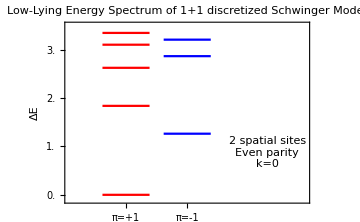

```mathematica
savagePlot = Show[
plot1, (* stacked bars for π=+1 parity eigenenergies *)
plot2, (* stacked bars for π=-1 parity eigenenergies *) 
PlotRange -> {{plotRangeL, plotRangeR},{0.0 - eLowerPadding, emax}},
AxesOrigin-> {plotRangeL, 0},
PlotLabel->Style["Low-Lying Energy Spectrum of\n1+1 discretized Schwinger Model", Black, FontSize->15],
Epilog->Style[Text["2 spatial sites\nEven parity\nk=0",{oddBoundR + 0.6(plotRangeR - oddBoundR),emax / 4.}],15],
Frame->True,
FrameLabel->{None,Style["ΔE",Black, FontSize-> 20],None,None},
FrameTicks->{{energyTicks, None}, {{{evenTick, "π=+1"}, {oddTick,"π=-1"}}, {None, None}}},
FrameTicksStyle->{Directive[Black, 15], Directive[Black, 20]},
FrameStyle->Directive[Black, 15, Thickness[0.002]],
ImageSize->Medium]
```

## Get the eigenstate ket expansion

### Coefficients for the ground state

```mathematica
gsCoeffs = evectorsEvenP[[ Position[evaluesEvenP, E0][[1, 1]] ]] //Chop//Rationalize
```

{0.671533,-0.640649,0.153118,0.233051,0.151536,0.151536,-0.0848005,-0.0333133,-0.077308,0.0158471,0.0117709,0.0117709,0.0110243}

```mathematica
evaluesEvenPSorted
evaluesOddPSorted
```

{-1.68317,0.157571,0.944926,1.42304,1.667,1.96622,2.1538,2.64714,3.33003,3.334,3.64898,3.99705,4.75242}

{-0.418548,1.18608,1.52746,2.12646,2.415,3.00919,3.334,3.53105,3.89757,4.73075}

### Coefficients for the states in either parity sector

```mathematica
eEvenPCoeffs=Table[
(* find the index of the ith even-parity excited state in the array of the corresponding eigenvectors; each array element is a list of coefficients for the expansion of that eigenvector in terms of the original basis *)
evectorsEvenP⟦Position[evaluesEvenP, evaluesEvenPSorted⟦i⟧]⟦1, 1⟧ ⟧ //Chop//Rationalize,
(* note that the first element is the ground state *)
{i, 2, Length[evaluesEvenPSorted]}];
eOddPCoeffs=Table[
(* find the index of the ith even-parity excited state in the array of the corresponding eigenvectors; each array element is a list of coefficients for the expansion of that eigenvector in terms of the original basis *)
evectorsOddP⟦Position[evaluesOddP, evaluesOddPSorted⟦i⟧]⟦1, 1⟧ ⟧ //Chop//Rationalize,
{i, Length[evaluesOddPSorted]}];
```

### Corresponding expansions

```mathematica
gsExpans= gsCoeffs.evenPSector;
```

```mathematica
ctr=0;
SetSharedVariable[ctr]
eEvenPExpans = Monitor[ParallelTable[ctr++;eEvenPCoeffs⟦i⟧.evenPSector, {i, Length[eEvenPCoeffs]}], ProgressIndicator[ctr, {1, Length[eEvenPCoeffs]}]];
```

```mathematica
ctr=0;
SetSharedVariable[ctr]
eOddPExpans = Monitor[ParallelTable[ctr++;eOddPCoeffs⟦i⟧.oddPSector, {i, Length[eOddPCoeffs]}], ProgressIndicator[ctr, {1, Length[eOddPCoeffs]}]];
```

```mathematica
es1Expans = e1Coeffs.oddPSector;
```

```mathematica
es1Expans = e1Coeffs.oddPSector;
es2Expans = e2Coeffs.evenPSector;
```

## Convert spins to Fermions

Define an operator to convert spins to fermions

```mathematica
spinMap = {
(* sends the ket of spins + links to a ket of fermions + links *)
		
S.psi_Ket:> Ket @@ (* apply ket again *)
(Flatten[(Partition[List[ (* parition the list into a list of spins and a list of kets*)
(* delete the ket head to split the list into spins and kets *)
Delete[0]@psi], 
	(* spins are converted to fermions, links are untouched *)
nfs]+{1, 0})*{1/2,1}]) ,
S.(x_ psi_Ket):>x S.psi/;NumericQ[x]};
```

```mathematica
rules =Join[basics,normalization, translation, parity, operators, spinMap];
```

Converted expansion

### π = +1

#### Ground State

Dominated by 
	the strong-coupling limit antiferromagnetic state,  
	a linear combination of all states where one fermion hopped, and 
	a linear combination of all states where hopping two fermions hopped in the same direction

```mathematica
gsTable =SortBy[
ParallelTable[
{gsCoeffs[[i]],
(* print the result of Hfield acting on the ket *)
N[(1/J) * Hfield/.Ket[Ψ]->evenPSector⟦i⟧/.params//.rules].evenPSector⟦i⟧//.rules,
(* print the actual ket expansion converted to fermionic sites *)
S.evenPSector[[i]]//. rules}, {i, Length[evenPSector]}],
Abs[#⟦2⟧] &];
```

```mathematica
gsTableForm = Grid[Select[Simplify[gsTable],#⟦2⟧ ≤ Λ3 &]]
```

0.671533 | 0 | 0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0
-0.640649 | 1. | 1/(2 √2)(0,0,1,1,0,1,0,1,0,-1,0,0,0,0,0,0+0,1,0,0,1,1,0,1,0,0,0,-1,0,0,0,0+0,1,0,1,0,0,1,1,0,0,0,0,0,-1,0,0+0,1,0,1,0,1,1,0,0,0,0,0,0,0,1,0+0,1,0,1,1,0,0,1,0,0,0,0,1,0,0,0+0,1,1,0,0,1,0,1,0,0,1,0,0,0,0,0+1,0,0,1,0,1,0,1,1,0,0,0,0,0,0,0+1,1,0,1,0,1,0,0,0,0,0,0,0,0,0,-1)
0.233051 | 2. | 1/(2 √2)(0,0,1,0,1,1,0,1,0,-1,0,-1,0,0,0,0+0,1,0,0,1,0,1,1,0,0,0,-1,0,-1,0,0+0,1,0,1,1,0,1,0,0,0,0,0,1,0,1,0+0,1,1,0,1,0,0,1,0,0,1,0,1,0,0,0+1,0,0,1,0,1,1,0,1,0,0,0,0,0,1,0+1,0,1,0,0,1,0,1,1,0,1,0,0,0,0,0+1,0,1,1,0,1,0,0,0,-1,0,0,0,0,0,-1+1,1,0,1,0,0,1,0,0,0,0,0,0,-1,0,-1)
0.151536 | 2. | 1/2 (0,0,1,1,0,1,1,0,0,-1,0,0,0,0,1,0+0,1,1,0,0,0,1,1,0,0,1,0,0,-1,0,0+1,0,0,0,1,1,0,1,1,0,0,-1,0,0,0,0+1,1,0,1,1,0,0,0,0,0,0,0,1,0,0,-1)
0.151536 | 2. | 1/2 (0,0,1,1,1,0,0,1,0,-1,0,0,1,0,0,0+0,1,0,0,1,1,1,0,0,0,0,-1,0,0,1,0+1,0,0,1,0,0,1,1,1,0,0,0,0,-1,0,0+1,1,1,0,0,1,0,0,0,0,1,0,0,0,0,-1)
0.153118 | 2. | 1/2 (0,0,1,1,0,0,1,1,0,-1,0,0,0,-1,0,0+0,1,1,0,0,1,1,0,0,0,1,0,0,0,1,0+1,0,0,1,1,0,0,1,1,0,0,0,1,0,0,0+1,1,0,0,1,1,0,0,0,0,0,-1,0,0,0,-1)
-0.0848005 | 3. | 1/(2 √2)(0,0,1,0,1,0,1,1,0,-1,0,-1,0,-1,0,0+0,1,1,0,1,0,1,0,0,0,1,0,1,0,1,0+1,0,0,1,1,0,1,0,1,0,0,0,1,0,1,0+1,0,1,0,0,1,1,0,1,0,1,0,0,0,1,0+1,0,1,0,1,0,0,1,1,0,1,0,1,0,0,0+1,0,1,0,1,1,0,0,0,-1,0,-1,0,0,0,-1+1,0,1,1,0,0,1,0,0,-1,0,0,0,-1,0,-1+1,1,0,0,1,0,1,0,0,0,0,-1,0,-1,0,-1)
-0.077308 | 3. | 1/(2 √2)(0,0,1,0,1,1,1,0,0,-1,0,-1,0,0,1,0+0,0,1,1,1,0,1,0,0,-1,0,0,1,0,1,0+1,0,0,0,1,0,1,1,1,0,0,-1,0,-1,0,0+1,0,0,0,1,1,1,0,1,0,0,-1,0,0,1,0+1,0,1,0,0,0,1,1,1,0,1,0,0,-1,0,0+1,0,1,1,1,0,0,0,0,-1,0,0,1,0,0,-1+1,1,1,0,0,0,1,0,0,0,1,0,0,-1,0,-1+1,1,1,0,1,0,0,0,0,0,1,0,1,0,0,-1)
-0.0333133 | 3. | 1/(2 √2)(0,0,0,1,0,1,1,1,1,0,0,0,0,0,1,1+0,0,0,1,1,1,0,1,0,-1,-1,-1,0,0,0,0+0,1,0,0,0,1,1,1,0,0,0,-1,-1,-1,0,0+0,1,0,1,1,1,0,0,0,0,0,0,1,1,1,0+0,1,1,1,0,0,0,1,0,0,1,1,1,0,0,0+0,1,1,1,0,1,0,0,-1,-1,0,0,0,0,0,-1+1,1,0,0,0,1,0,1,1,1,1,0,0,0,0,0+1,1,0,1,0,0,0,1,0,0,0,0,0,-1,-1,-1)

```mathematica
Export[StringJoin["~/Desktop/report/gs_L4.png"],
gsTableForm, 
ImageResolution->imageRes]
```

~/Desktop/report/gs_L4.png

```mathematica
(*Export[StringJoin["~/Desktop/gsTable_NFS_",ToString[nfs], "_L1_", ToString[Λ1],"_L2_",ToString[],.png"],
gsTableForm, 
ImageResolution→imageRes]*)
```

#### 1st even-parity excited state

Compared to the ground state, 
	there is less overlap onto the strong-coupling limit antiferromagnetic state,
	for nfs = 4, higher-winding number states also becomes important (as seen by larger charge on the links)

```mathematica
e1EvenTable =SortBy[ParallelTable[
{eEvenPCoeffs⟦1⟧⟦i⟧,
(* print the result of Hmass acting on the ket *)
N[(1/(m *nfs)) * Hmass/.Ket[Ψ]->evenPSector⟦i⟧/.params//.rules].evenPSector⟦i⟧//.rules,
(* print the result of Hfield acting on the ket *)
N[(1/J) * Hfield/.Ket[Ψ]->evenPSector⟦i⟧/.params//.rules].evenPSector⟦i⟧//.rules,
(* print the actual ket expansion converted to fermionic sites *)
S.evenPSector[[i]]//. rules}, {i, Length[evenPSector]}],
(* sort first by total charge, then by weight *)
Abs[#⟦3⟧] &];
```

```mathematica
e1EvenTableForm = TableForm[Select[e1EvenTable,#⟦3⟧ ≤ Λ3 &],
TableHeadings->{Table[j, {j, 1, Length[evenPSector]}],{"weight", "mass", "charge", "state"}}]
```

| weight | mass | charge | state
1 | 0.599185 | -0.5 | 0 | 0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0
2 | 0.208272 | -0.25 | 1. | (0,0,1,1,0,1,0,1,0,-1,0,0,0,0,0,0)/(2 √2)+(0,1,0,0,1,1,0,1,0,0,0,-1,0,0,0,0)/(2 √2)+(0,1,0,1,0,0,1,1,0,0,0,0,0,-1,0,0)/(2 √2)+(0,1,0,1,0,1,1,0,0,0,0,0,0,0,1,0)/(2 √2)+(0,1,0,1,1,0,0,1,0,0,0,0,1,0,0,0)/(2 √2)+(0,1,1,0,0,1,0,1,0,0,1,0,0,0,0,0)/(2 √2)+(1,0,0,1,0,1,0,1,1,0,0,0,0,0,0,0)/(2 √2)+(1,1,0,1,0,1,0,0,0,0,0,0,0,0,0,-1)/(2 √2)
3 | -0.487587 | -1.73472×10^-18 | 2. | (0,0,1,0,1,1,0,1,0,-1,0,-1,0,0,0,0)/(2 √2)+(0,1,0,0,1,0,1,1,0,0,0,-1,0,-1,0,0)/(2 √2)+(0,1,0,1,1,0,1,0,0,0,0,0,1,0,1,0)/(2 √2)+(0,1,1,0,1,0,0,1,0,0,1,0,1,0,0,0)/(2 √2)+(1,0,0,1,0,1,1,0,1,0,0,0,0,0,1,0)/(2 √2)+(1,0,1,0,0,1,0,1,1,0,1,0,0,0,0,0)/(2 √2)+(1,0,1,1,0,1,0,0,0,-1,0,0,0,0,0,-1)/(2 √2)+(1,1,0,1,0,0,1,0,0,0,0,0,0,-1,0,-1)/(2 √2)
4 | -0.254602 | 0. | 2. | 1/2 0,0,1,1,0,0,1,1,0,-1,0,0,0,-1,0,0+1/2 0,1,1,0,0,1,1,0,0,0,1,0,0,0,1,0+1/2 1,0,0,1,1,0,0,1,1,0,0,0,1,0,0,0+1/2 1,1,0,0,1,1,0,0,0,0,0,-1,0,0,0,-1
5 | -0.202059 | 0. | 2. | 1/2 0,0,1,1,0,1,1,0,0,-1,0,0,0,0,1,0+1/2 0,1,1,0,0,0,1,1,0,0,1,0,0,-1,0,0+1/2 1,0,0,0,1,1,0,1,1,0,0,-1,0,0,0,0+1/2 1,1,0,1,1,0,0,0,0,0,0,0,1,0,0,-1
6 | -0.202059 | 0. | 2. | 1/2 0,0,1,1,1,0,0,1,0,-1,0,0,1,0,0,0+1/2 0,1,0,0,1,1,1,0,0,0,0,-1,0,0,1,0+1/2 1,0,0,1,0,0,1,1,1,0,0,0,0,-1,0,0+1/2 1,1,1,0,0,1,0,0,0,0,1,0,0,0,0,-1
7 | 0.16193 | -0.25 | 3. | (0,0,0,1,0,1,1,1,1,0,0,0,0,0,1,1)/(2 √2)+(0,0,0,1,1,1,0,1,0,-1,-1,-1,0,0,0,0)/(2 √2)+(0,1,0,0,0,1,1,1,0,0,0,-1,-1,-1,0,0)/(2 √2)+(0,1,0,1,1,1,0,0,0,0,0,0,1,1,1,0)/(2 √2)+(0,1,1,1,0,0,0,1,0,0,1,1,1,0,0,0)/(2 √2)+(0,1,1,1,0,1,0,0,-1,-1,0,0,0,0,0,-1)/(2 √2)+(1,1,0,0,0,1,0,1,1,1,1,0,0,0,0,0)/(2 √2)+(1,1,0,1,0,0,0,1,0,0,0,0,0,-1,-1,-1)/(2 √2)
8 | 0.223053 | 0.25 | 3. | (0,0,1,0,1,1,1,0,0,-1,0,-1,0,0,1,0)/(2 √2)+(0,0,1,1,1,0,1,0,0,-1,0,0,1,0,1,0)/(2 √2)+(1,0,0,0,1,0,1,1,1,0,0,-1,0,-1,0,0)/(2 √2)+(1,0,0,0,1,1,1,0,1,0,0,-1,0,0,1,0)/(2 √2)+(1,0,1,0,0,0,1,1,1,0,1,0,0,-1,0,0)/(2 √2)+(1,0,1,1,1,0,0,0,0,-1,0,0,1,0,0,-1)/(2 √2)+(1,1,1,0,0,0,1,0,0,0,1,0,0,-1,0,-1)/(2 √2)+(1,1,1,0,1,0,0,0,0,0,1,0,1,0,0,-1)/(2 √2)
9 | 0.335214 | 0.25 | 3. | (0,0,1,0,1,0,1,1,0,-1,0,-1,0,-1,0,0)/(2 √2)+(0,1,1,0,1,0,1,0,0,0,1,0,1,0,1,0)/(2 √2)+(1,0,0,1,1,0,1,0,1,0,0,0,1,0,1,0)/(2 √2)+(1,0,1,0,0,1,1,0,1,0,1,0,0,0,1,0)/(2 √2)+(1,0,1,0,1,0,0,1,1,0,1,0,1,0,0,0)/(2 √2)+(1,0,1,0,1,1,0,0,0,-1,0,-1,0,0,0,-1)/(2 √2)+(1,0,1,1,0,0,1,0,0,-1,0,0,0,-1,0,-1)/(2 √2)+(1,1,0,0,1,0,1,0,0,0,0,-1,0,-1,0,-1)/(2 √2)

```mathematica
(*Export[StringJoin["~/Desktop/e2Table_NFS_",ToString[nfs], "_L1_", ToString[Λ1],"_L2_",ToString[Λ2],".png"],
 e2TableForm, 
ImageResolution->imageRes]*)
```

### π = -1

#### 1st odd-parity excited state

The odd-parity first excited state is dominated by 
	a linear combination of states where one fermion hopped, with alternating overall sign depending on the direction of hopping; and
	a superposition of states where both fermions hopped, again with the overall sign as expected

```mathematica
e1OddTable =SortBy[Table[
{eOddPCoeffs⟦1⟧⟦i⟧,
(* print the result of Hfield acting on the ket *)
N[(1/J) * Hfield/.Ket[Ψ]->oddPSector⟦i⟧/.params//.rules].oddPSector⟦i⟧//.rules,
(* print the actual ket expansion converted to fermionic sites *)
S.oddPSector[[i]]//. rules}, {i, Length[oddPSector]}],
(* sort first by total charge, then by weight *)
Abs[#⟦2⟧] &];
```

```mathematica
e1OddTableForm = Grid[Select[Simplify[e1OddTable],#⟦2⟧ ≤ Λ3 &]]
```

0.703071 | 1. | 1/(2 √2)(0,0,1,1,0,1,0,1,0,-1,0,0,0,0,0,0+0,1,0,0,1,1,0,1,0,0,0,-1,0,0,0,0+0,1,0,1,0,0,1,1,0,0,0,0,0,-1,0,0-0,1,0,1,0,1,1,0,0,0,0,0,0,0,1,0-0,1,0,1,1,0,0,1,0,0,0,0,1,0,0,0-0,1,1,0,0,1,0,1,0,0,1,0,0,0,0,0-1,0,0,1,0,1,0,1,1,0,0,0,0,0,0,0+1,1,0,1,0,1,0,0,0,0,0,0,0,0,0,-1)
-0.525354 | 2. | 1/(2 √2)(0,0,1,0,1,1,0,1,0,-1,0,-1,0,0,0,0+0,1,0,0,1,0,1,1,0,0,0,-1,0,-1,0,0-0,1,0,1,1,0,1,0,0,0,0,0,1,0,1,0-0,1,1,0,1,0,0,1,0,0,1,0,1,0,0,0-1,0,0,1,0,1,1,0,1,0,0,0,0,0,1,0-1,0,1,0,0,1,0,1,1,0,1,0,0,0,0,0+1,0,1,1,0,1,0,0,0,-1,0,0,0,0,0,-1+1,1,0,1,0,0,1,0,0,0,0,0,0,-1,0,-1)
-0.335893 | 2. | 1/2 (0,0,1,1,0,0,1,1,0,-1,0,0,0,-1,0,0-0,1,1,0,0,1,1,0,0,0,1,0,0,0,1,0-1,0,0,1,1,0,0,1,1,0,0,0,1,0,0,0+1,1,0,0,1,1,0,0,0,0,0,-1,0,0,0,-1)
-0.0896495 | 3. | 1/(2 √2)(-0,0,1,0,1,1,1,0,0,-1,0,-1,0,0,1,0+0,0,1,1,1,0,1,0,0,-1,0,0,1,0,1,0-1,0,0,0,1,0,1,1,1,0,0,-1,0,-1,0,0+1,0,0,0,1,1,1,0,1,0,0,-1,0,0,1,0+1,0,1,0,0,0,1,1,1,0,1,0,0,-1,0,0-1,0,1,1,1,0,0,0,0,-1,0,0,1,0,0,-1-1,1,1,0,0,0,1,0,0,0,1,0,0,-1,0,-1+1,1,1,0,1,0,0,0,0,0,1,0,1,0,0,-1)
0.120278 | 3. | 1/(2 √2)(-0,0,0,1,0,1,1,1,1,0,0,0,0,0,1,1+0,0,0,1,1,1,0,1,0,-1,-1,-1,0,0,0,0+0,1,0,0,0,1,1,1,0,0,0,-1,-1,-1,0,0-0,1,0,1,1,1,0,0,0,0,0,0,1,1,1,0-0,1,1,1,0,0,0,1,0,0,1,1,1,0,0,0+0,1,1,1,0,1,0,0,-1,-1,0,0,0,0,0,-1-1,1,0,0,0,1,0,1,1,1,1,0,0,0,0,0+1,1,0,1,0,0,0,1,0,0,0,0,0,-1,-1,-1)
0.287616 | 3. | 1/(2 √2)(0,0,1,0,1,0,1,1,0,-1,0,-1,0,-1,0,0-0,1,1,0,1,0,1,0,0,0,1,0,1,0,1,0-1,0,0,1,1,0,1,0,1,0,0,0,1,0,1,0-1,0,1,0,0,1,1,0,1,0,1,0,0,0,1,0-1,0,1,0,1,0,0,1,1,0,1,0,1,0,0,0+1,0,1,0,1,1,0,0,0,-1,0,-1,0,0,0,-1+1,0,1,1,0,0,1,0,0,-1,0,0,0,-1,0,-1+1,1,0,0,1,0,1,0,0,0,0,-1,0,-1,0,-1)

```mathematica
Export[StringJoin["~/Desktop/report/e1_L4.png"],
e1OddTableForm, 
ImageResolution->imageRes]
```

~/Desktop/report/e1_L4.png

```mathematica
(*Export[StringJoin["~/Desktop/e1Table_NFS_",ToString[nfs], "_L1_", ToString[Λ1],"_L2_",ToString[Λ2],".png"],
e1OddTableForm, 
ImageResolution->imageRes]*)
```

```mathematica
2nd odd-parity excited state
```

{2 d n odd-excited state (P.psi_Ket:>Ket@@MapThread[Times,{{Delete[0][Permute[psi,Cycles[Join[Table[{n+1,nfs-n+1},{n,1,nfs/2-1}],Table[{n+1+nfs,nfs-n+nfs},{n,0,nfs/2-1}]]]]]},Join[ones,-ones]/.ones→Table[1,{i,nfs}]}]),2 d n odd-excited state (P.(psi_Ket x_):>x P.psi/;NumericQ[x])}

```mathematica
e2OddTable =SortBy[Table[
{eOddPCoeffs⟦2⟧⟦i⟧,
(* print the result of Hmass acting on the ket *)
N[(1/(m *nfs)) * Hmass/.Ket[Ψ]->oddPSector⟦i⟧/.params//.rules].oddPSector⟦i⟧//.rules,
(* print the result of Hfield acting on the ket *)
N[(1/J) * Hfield/.Ket[Ψ]->oddPSector⟦i⟧/.params//.rules].oddPSector⟦i⟧//.rules,
(* print the actual ket expansion converted to fermionic sites *)
S.oddPSector[[i]]//. rules}, {i, Length[oddPSector]}],
(* sort first by total charge, then by weight *)
Abs[#⟦3⟧] &];
```

```mathematica
e2OddTableForm = TableForm[Select[e2OddTable,#⟦3⟧ ≤ Λ3 &],
TableHeadings->{Table[j, {j, 1, Length[oddPSector]}],{"weight", "mass", "charge", "state"}}]
```

| weight | mass | charge | state
1 | -0.549667 | -0.25 | 1. | (0,0,1,1,0,1,0,1,0,-1,0,0,0,0,0,0)/(2 √2)+(0,1,0,0,1,1,0,1,0,0,0,-1,0,0,0,0)/(2 √2)+(0,1,0,1,0,0,1,1,0,0,0,0,0,-1,0,0)/(2 √2)-(0,1,0,1,0,1,1,0,0,0,0,0,0,0,1,0)/(2 √2)-(0,1,0,1,1,0,0,1,0,0,0,0,1,0,0,0)/(2 √2)-(0,1,1,0,0,1,0,1,0,0,1,0,0,0,0,0)/(2 √2)-(1,0,0,1,0,1,0,1,1,0,0,0,0,0,0,0)/(2 √2)+(1,1,0,1,0,1,0,0,0,0,0,0,0,0,0,-1)/(2 √2)
2 | -0.391067 | -1.73472×10^-18 | 2. | (0,0,1,0,1,1,0,1,0,-1,0,-1,0,0,0,0)/(2 √2)+(0,1,0,0,1,0,1,1,0,0,0,-1,0,-1,0,0)/(2 √2)-(0,1,0,1,1,0,1,0,0,0,0,0,1,0,1,0)/(2 √2)-(0,1,1,0,1,0,0,1,0,0,1,0,1,0,0,0)/(2 √2)-(1,0,0,1,0,1,1,0,1,0,0,0,0,0,1,0)/(2 √2)-(1,0,1,0,0,1,0,1,1,0,1,0,0,0,0,0)/(2 √2)+(1,0,1,1,0,1,0,0,0,-1,0,0,0,0,0,-1)/(2 √2)+(1,1,0,1,0,0,1,0,0,0,0,0,0,-1,0,-1)/(2 √2)
3 | 0.149156 | 0. | 2. | 1/2 0,0,1,1,0,0,1,1,0,-1,0,0,0,-1,0,0-1/2 0,1,1,0,0,1,1,0,0,0,1,0,0,0,1,0-1/2 1,0,0,1,1,0,0,1,1,0,0,0,1,0,0,0+1/2 1,1,0,0,1,1,0,0,0,0,0,-1,0,0,0,-1
4 | -0.177484 | 0.25 | 3. | -(0,0,1,0,1,1,1,0,0,-1,0,-1,0,0,1,0)/(2 √2)+(0,0,1,1,1,0,1,0,0,-1,0,0,1,0,1,0)/(2 √2)-(1,0,0,0,1,0,1,1,1,0,0,-1,0,-1,0,0)/(2 √2)+(1,0,0,0,1,1,1,0,1,0,0,-1,0,0,1,0)/(2 √2)+(1,0,1,0,0,0,1,1,1,0,1,0,0,-1,0,0)/(2 √2)-(1,0,1,1,1,0,0,0,0,-1,0,0,1,0,0,-1)/(2 √2)-(1,1,1,0,0,0,1,0,0,0,1,0,0,-1,0,-1)/(2 √2)+(1,1,1,0,1,0,0,0,0,0,1,0,1,0,0,-1)/(2 √2)
5 | 0.401545 | -0.25 | 3. | -(0,0,0,1,0,1,1,1,1,0,0,0,0,0,1,1)/(2 √2)+(0,0,0,1,1,1,0,1,0,-1,-1,-1,0,0,0,0)/(2 √2)+(0,1,0,0,0,1,1,1,0,0,0,-1,-1,-1,0,0)/(2 √2)-(0,1,0,1,1,1,0,0,0,0,0,0,1,1,1,0)/(2 √2)-(0,1,1,1,0,0,0,1,0,0,1,1,1,0,0,0)/(2 √2)+(0,1,1,1,0,1,0,0,-1,-1,0,0,0,0,0,-1)/(2 √2)-(1,1,0,0,0,1,0,1,1,1,1,0,0,0,0,0)/(2 √2)+(1,1,0,1,0,0,0,1,0,0,0,0,0,-1,-1,-1)/(2 √2)
6 | 0.448223 | 0.25 | 3. | (0,0,1,0,1,0,1,1,0,-1,0,-1,0,-1,0,0)/(2 √2)-(0,1,1,0,1,0,1,0,0,0,1,0,1,0,1,0)/(2 √2)-(1,0,0,1,1,0,1,0,1,0,0,0,1,0,1,0)/(2 √2)-(1,0,1,0,0,1,1,0,1,0,1,0,0,0,1,0)/(2 √2)-(1,0,1,0,1,0,0,1,1,0,1,0,1,0,0,0)/(2 √2)+(1,0,1,0,1,1,0,0,0,-1,0,-1,0,0,0,-1)/(2 √2)+(1,0,1,1,0,0,1,0,0,-1,0,0,0,-1,0,-1)/(2 √2)+(1,1,0,0,1,0,1,0,0,0,0,-1,0,-1,0,-1)/(2 √2)

## Define interpolating operators

Define effective mass and basic operators

```mathematica
ClearAll[g]
g[ovrlapSrc_,ovrlapSnk_, energies_,t_, T_]:=Total[Table[Abs[ovrlapSrc⟦i⟧ *ovrlapSnk⟦i⟧]/(2 (energies⟦i⟧ -energies⟦1⟧)) *
( Exp[-(energies⟦i⟧ -energies⟦1⟧)*t]+ Exp[-(energies⟦i⟧ -energies⟦1⟧)*(T - t)]) ,
{i, 2, Length[energies]}]];
```

```mathematica
density ={
SubPlus[χ][i_].psi_Ket :>If[psi[[i + 1]] == 1,0,ReplacePart[psi, i + 1->psi[[i+ 1]] + 1]],
SubPlus[χ][i_].(x_ psi_Ket):>x SubPlus[χ][i].psi/;NumericQ[x],
SubMinus[χ][i_].psi_Ket :>If[psi[[i + 1]] == 0,0,ReplacePart[psi, i+ 1->psi[[i + 1]]-1]],
SubMinus[χ][i_].(x_ psi_Ket):>x SubMinus[χ][i].psi/;NumericQ[x]};
```

```mathematica
rules =Join[basics,normalization, translation, parity, operators, spinMap, density];
```

Define naive interpolating operators

#### Chiral density

```mathematica
χ0Src= (-1)^1 SubPlus[χ][1].SubMinus[χ][1].state ;
χ0Snk= 2/nfs Sum[(-1)^i SubPlus[χ][i].SubMinus[χ][i].state , {i, 1, nfs-1, 2}];
```

#### “Hopping Density”

Good projection on π = -1

```mathematica
M01Src =SubPlus[χ][fs[0]].SubPlus[U][fs[0]].SubMinus[χ][fs[1]].state -SubPlus[χ][fs[2]].SubMinus[U][fs[1]].SubMinus[χ][fs[1]].state ;
M01Snk =2/nfs Sum[-SubPlus[χ][fs[i+1]].SubMinus[U][fs[i]].SubMinus[χ][fs[i]].state +SubPlus[χ][fs[i-1]].SubPlus[U][fs[i-1]].SubMinus[χ][fs[i]].state, 
{i, 1, nfs-1, 2}];
```

Bad projection on π = -1 (original bug)

```mathematica
M01SrcBad =SubPlus[χ][fs[0]].SubPlus[U][fs[0]].SubMinus[χ][fs[1]].state -SubPlus[χ][fs[1]].SubMinus[U][fs[0]].SubMinus[χ][fs[0]].state ;
M01SnkBad =2/nfs Sum[SubPlus[χ][fs[i]].SubMinus[U][fs[i-1]].SubMinus[χ][fs[i-1]].state -SubPlus[χ][fs[i-1]].SubPlus[U][fs[i-1]].SubMinus[χ][fs[i]].state, 
{i, 1, nfs-1, 2}];
```

#### Get the parity eigenstate expansion in terms of fermions (not spins)

```mathematica
(* expansion of energy eigenstates in terms of the even- and odd- parity states, converted to fermionic description *)
```

```mathematica
gs = Table[gsCoeffs⟦i⟧ * S.evenPSector[[i]]//. rules, {i, Length[evenPSector]}];
eOddP = Table[
Table[eOddPCoeffs⟦j⟧⟦i⟧ * S.oddPSector[[i]]//. rules, {i, Length[oddPSector]}],
{j, 1, Length[eOddPCoeffs]}];
eEvenP = Table[
Table[eEvenPCoeffs⟦j⟧⟦i⟧ * S.evenPSector[[i]]//. rules, {i, Length[evenPSector]}],
{j, 1, Length[eEvenPCoeffs]}];
```

```mathematica
gsExpanded=Expand[Total[gs]];
```

```mathematica
e1Expanded = Expand[Total[eOddP⟦1⟧]];
```

```mathematica
(* list of all eigen energies: first all even-parity, then all odd-parity *)
energiesParitySorted = Join[Sort[evaluesEvenP], Sort[evaluesOddP]];
```

```mathematica
(* expansion of even- and odd- parity states in terms of the original basis converted to fermionic description *)
```

```mathematica
evenPSectorF = Table[S.evenPSector[[i]]//. rules, {i, Length[evenPSector]}];
oddPSectorF = Table[S.oddPSector[[i]]//. rules, {i, Length[oddPSector]}];
```

```mathematica
χ0SrcOnGS =Table[Expand[χ0Src/.state->basisKet//.rules],{basisKet,gs}];
χ0SnkOnGS =Table[Expand[χ0Snk/.state->basisKet//.rules],{basisKet,gs}];
M01SrcOnGS = Table[Expand[M01Src/.state->basisKet//.rules],{basisKet,gs}];
M01SnkOnGS = Table[Expand[M01Snk/.state->basisKet//.rules],{basisKet,gs}];
M01SrcBadOnGS = Table[Expand[M01SrcBad/.state->basisKet//.rules],{basisKet,gs}];
M01SnkBadOnGS = Table[Expand[M01SnkBad/.state->basisKet//.rules],{basisKet,gs}];
```

Construct an operator that takes GS to E1

```mathematica
bareVac =Ket@@Join[Table[Boole[Mod[i, 2] == 0], {i,1, nfs}], ConstantArray[0, nfs]]
```

0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0

## Construct an operator for BareVac ⇒ π = +1 state

```mathematica
norm[i_Integer]/; i≥1 :=1/(√If[L/i==2,2, 1]);
```

### Inspect GS expansion

```mathematica
TableForm[Select[gsTable,#⟦2⟧ ≤ Λ3 &],
TableHeadings->{Table[j, {j, 1, Length[evenPSector]}],{"weight", "flux", "state"}}]
```

| weight | flux | state
1 | 0.671533 | 0 | 0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0
2 | -0.640649 | 1. | (0,0,1,1,0,1,0,1,0,-1,0,0,0,0,0,0)/(2 √2)+(0,1,0,0,1,1,0,1,0,0,0,-1,0,0,0,0)/(2 √2)+(0,1,0,1,0,0,1,1,0,0,0,0,0,-1,0,0)/(2 √2)+(0,1,0,1,0,1,1,0,0,0,0,0,0,0,1,0)/(2 √2)+(0,1,0,1,1,0,0,1,0,0,0,0,1,0,0,0)/(2 √2)+(0,1,1,0,0,1,0,1,0,0,1,0,0,0,0,0)/(2 √2)+(1,0,0,1,0,1,0,1,1,0,0,0,0,0,0,0)/(2 √2)+(1,1,0,1,0,1,0,0,0,0,0,0,0,0,0,-1)/(2 √2)
3 | 0.233051 | 2. | (0,0,1,0,1,1,0,1,0,-1,0,-1,0,0,0,0)/(2 √2)+(0,1,0,0,1,0,1,1,0,0,0,-1,0,-1,0,0)/(2 √2)+(0,1,0,1,1,0,1,0,0,0,0,0,1,0,1,0)/(2 √2)+(0,1,1,0,1,0,0,1,0,0,1,0,1,0,0,0)/(2 √2)+(1,0,0,1,0,1,1,0,1,0,0,0,0,0,1,0)/(2 √2)+(1,0,1,0,0,1,0,1,1,0,1,0,0,0,0,0)/(2 √2)+(1,0,1,1,0,1,0,0,0,-1,0,0,0,0,0,-1)/(2 √2)+(1,1,0,1,0,0,1,0,0,0,0,0,0,-1,0,-1)/(2 √2)
4 | 0.151536 | 2. | 1/2 0,0,1,1,0,1,1,0,0,-1,0,0,0,0,1,0+1/2 0,1,1,0,0,0,1,1,0,0,1,0,0,-1,0,0+1/2 1,0,0,0,1,1,0,1,1,0,0,-1,0,0,0,0+1/2 1,1,0,1,1,0,0,0,0,0,0,0,1,0,0,-1
5 | 0.151536 | 2. | 1/2 0,0,1,1,1,0,0,1,0,-1,0,0,1,0,0,0+1/2 0,1,0,0,1,1,1,0,0,0,0,-1,0,0,1,0+1/2 1,0,0,1,0,0,1,1,1,0,0,0,0,-1,0,0+1/2 1,1,1,0,0,1,0,0,0,0,1,0,0,0,0,-1
6 | 0.153118 | 2. | 1/2 0,0,1,1,0,0,1,1,0,-1,0,0,0,-1,0,0+1/2 0,1,1,0,0,1,1,0,0,0,1,0,0,0,1,0+1/2 1,0,0,1,1,0,0,1,1,0,0,0,1,0,0,0+1/2 1,1,0,0,1,1,0,0,0,0,0,-1,0,0,0,-1
7 | -0.0848005 | 3. | (0,0,1,0,1,0,1,1,0,-1,0,-1,0,-1,0,0)/(2 √2)+(0,1,1,0,1,0,1,0,0,0,1,0,1,0,1,0)/(2 √2)+(1,0,0,1,1,0,1,0,1,0,0,0,1,0,1,0)/(2 √2)+(1,0,1,0,0,1,1,0,1,0,1,0,0,0,1,0)/(2 √2)+(1,0,1,0,1,0,0,1,1,0,1,0,1,0,0,0)/(2 √2)+(1,0,1,0,1,1,0,0,0,-1,0,-1,0,0,0,-1)/(2 √2)+(1,0,1,1,0,0,1,0,0,-1,0,0,0,-1,0,-1)/(2 √2)+(1,1,0,0,1,0,1,0,0,0,0,-1,0,-1,0,-1)/(2 √2)
8 | -0.077308 | 3. | (0,0,1,0,1,1,1,0,0,-1,0,-1,0,0,1,0)/(2 √2)+(0,0,1,1,1,0,1,0,0,-1,0,0,1,0,1,0)/(2 √2)+(1,0,0,0,1,0,1,1,1,0,0,-1,0,-1,0,0)/(2 √2)+(1,0,0,0,1,1,1,0,1,0,0,-1,0,0,1,0)/(2 √2)+(1,0,1,0,0,0,1,1,1,0,1,0,0,-1,0,0)/(2 √2)+(1,0,1,1,1,0,0,0,0,-1,0,0,1,0,0,-1)/(2 √2)+(1,1,1,0,0,0,1,0,0,0,1,0,0,-1,0,-1)/(2 √2)+(1,1,1,0,1,0,0,0,0,0,1,0,1,0,0,-1)/(2 √2)
9 | -0.0333133 | 3. | (0,0,0,1,0,1,1,1,1,0,0,0,0,0,1,1)/(2 √2)+(0,0,0,1,1,1,0,1,0,-1,-1,-1,0,0,0,0)/(2 √2)+(0,1,0,0,0,1,1,1,0,0,0,-1,-1,-1,0,0)/(2 √2)+(0,1,0,1,1,1,0,0,0,0,0,0,1,1,1,0)/(2 √2)+(0,1,1,1,0,0,0,1,0,0,1,1,1,0,0,0)/(2 √2)+(0,1,1,1,0,1,0,0,-1,-1,0,0,0,0,0,-1)/(2 √2)+(1,1,0,0,0,1,0,1,1,1,1,0,0,0,0,0)/(2 √2)+(1,1,0,1,0,0,0,1,0,0,0,0,0,-1,-1,-1)/(2 √2)

```mathematica
gsTableForm=Grid[Select[Simplify[gsTable],#⟦2⟧ ≤ Λ2 &], ItemSize->{{6.0, 1.5, 60},{3, 3,3}}, Frame-> All]
```

0.671533 | 0 | 0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0
-0.640649 | 1. | 1/(2 √2)(0,0,1,1,0,1,0,1,0,-1,0,0,0,0,0,0+0,1,0,0,1,1,0,1,0,0,0,-1,0,0,0,0+0,1,0,1,0,0,1,1,0,0,0,0,0,-1,0,0+0,1,0,1,0,1,1,0,0,0,0,0,0,0,1,0+0,1,0,1,1,0,0,1,0,0,0,0,1,0,0,0+0,1,1,0,0,1,0,1,0,0,1,0,0,0,0,0+1,0,0,1,0,1,0,1,1,0,0,0,0,0,0,0+1,1,0,1,0,1,0,0,0,0,0,0,0,0,0,-1)
0.233051 | 2. | 1/(2 √2)(0,0,1,0,1,1,0,1,0,-1,0,-1,0,0,0,0+0,1,0,0,1,0,1,1,0,0,0,-1,0,-1,0,0+0,1,0,1,1,0,1,0,0,0,0,0,1,0,1,0+0,1,1,0,1,0,0,1,0,0,1,0,1,0,0,0+1,0,0,1,0,1,1,0,1,0,0,0,0,0,1,0+1,0,1,0,0,1,0,1,1,0,1,0,0,0,0,0+1,0,1,1,0,1,0,0,0,-1,0,0,0,0,0,-1+1,1,0,1,0,0,1,0,0,0,0,0,0,-1,0,-1)
0.151536 | 2. | 1/2 (0,0,1,1,0,1,1,0,0,-1,0,0,0,0,1,0+0,1,1,0,0,0,1,1,0,0,1,0,0,-1,0,0+1,0,0,0,1,1,0,1,1,0,0,-1,0,0,0,0+1,1,0,1,1,0,0,0,0,0,0,0,1,0,0,-1)
0.151536 | 2. | 1/2 (0,0,1,1,1,0,0,1,0,-1,0,0,1,0,0,0+0,1,0,0,1,1,1,0,0,0,0,-1,0,0,1,0+1,0,0,1,0,0,1,1,1,0,0,0,0,-1,0,0+1,1,1,0,0,1,0,0,0,0,1,0,0,0,0,-1)
0.153118 | 2. | 1/2 (0,0,1,1,0,0,1,1,0,-1,0,0,0,-1,0,0+0,1,1,0,0,1,1,0,0,0,1,0,0,0,1,0+1,0,0,1,1,0,0,1,1,0,0,0,1,0,0,0+1,1,0,0,1,1,0,0,0,0,0,-1,0,0,0,-1)
-0.0848005 | 3. | 1/(2 √2)(0,0,1,0,1,0,1,1,0,-1,0,-1,0,-1,0,0+0,1,1,0,1,0,1,0,0,0,1,0,1,0,1,0+1,0,0,1,1,0,1,0,1,0,0,0,1,0,1,0+1,0,1,0,0,1,1,0,1,0,1,0,0,0,1,0+1,0,1,0,1,0,0,1,1,0,1,0,1,0,0,0+1,0,1,0,1,1,0,0,0,-1,0,-1,0,0,0,-1+1,0,1,1,0,0,1,0,0,-1,0,0,0,-1,0,-1+1,1,0,0,1,0,1,0,0,0,0,-1,0,-1,0,-1)
-0.077308 | 3. | 1/(2 √2)(0,0,1,0,1,1,1,0,0,-1,0,-1,0,0,1,0+0,0,1,1,1,0,1,0,0,-1,0,0,1,0,1,0+1,0,0,0,1,0,1,1,1,0,0,-1,0,-1,0,0+1,0,0,0,1,1,1,0,1,0,0,-1,0,0,1,0+1,0,1,0,0,0,1,1,1,0,1,0,0,-1,0,0+1,0,1,1,1,0,0,0,0,-1,0,0,1,0,0,-1+1,1,1,0,0,0,1,0,0,0,1,0,0,-1,0,-1+1,1,1,0,1,0,0,0,0,0,1,0,1,0,0,-1)
-0.0333133 | 3. | 1/(2 √2)(0,0,0,1,0,1,1,1,1,0,0,0,0,0,1,1+0,0,0,1,1,1,0,1,0,-1,-1,-1,0,0,0,0+0,1,0,0,0,1,1,1,0,0,0,-1,-1,-1,0,0+0,1,0,1,1,1,0,0,0,0,0,0,1,1,1,0+0,1,1,1,0,0,0,1,0,0,1,1,1,0,0,0+0,1,1,1,0,1,0,0,-1,-1,0,0,0,0,0,-1+1,1,0,0,0,1,0,1,1,1,1,0,0,0,0,0+1,1,0,1,0,0,0,1,0,0,0,0,0,-1,-1,-1)
0.0110243 | 4. | 1/(2 √2)(0,0,0,0,1,1,1,1,1,0,0,-1,0,0,1,1+0,0,0,1,1,1,1,0,0,-1,-1,-1,0,0,1,0+0,0,1,1,1,1,0,0,0,-1,0,0,1,1,1,0+0,1,1,1,1,0,0,0,-1,-1,0,0,1,0,0,-1+1,0,0,0,0,1,1,1,1,0,0,-1,-1,-1,0,0+1,1,0,0,0,0,1,1,1,1,1,0,0,-1,0,0+1,1,1,0,0,0,0,1,0,0,1,0,0,-1,-1,-1+1,1,1,1,0,0,0,0,0,0,1,1,1,0,0,-1)
0.0117709 | 4. | 1/(2 √2)(0,0,1,0,0,1,1,1,0,-1,0,-1,-1,-1,0,0+0,0,1,0,0,1,1,1,1,0,1,0,0,0,1,1+0,1,1,1,0,0,1,0,-1,-1,0,0,0,-1,0,-1+0,1,1,1,0,0,1,0,0,0,1,1,1,0,1,0+1,0,0,1,1,1,0,0,0,-1,-1,-1,0,0,0,-1+1,0,0,1,1,1,0,0,1,0,0,0,1,1,1,0+1,1,0,0,1,0,0,1,0,0,0,-1,0,-1,-1,-1+1,1,0,0,1,0,0,1,1,1,1,0,1,0,0,0)
0.0117709 | 4. | 1/(2 √2)(0,0,0,1,1,0,1,1,0,-1,-1,-1,0,-1,0,0+0,0,0,1,1,0,1,1,1,0,0,0,1,0,1,1+0,1,1,0,1,1,0,0,-1,-1,0,-1,0,0,0,-1+0,1,1,0,1,1,0,0,0,0,1,0,1,1,1,0+1,0,1,1,0,0,0,1,0,-1,0,0,0,-1,-1,-1+1,0,1,1,0,0,0,1,1,0,1,1,1,0,0,0+1,1,0,0,0,1,1,0,0,0,0,-1,-1,-1,0,-1+1,1,0,0,0,1,1,0,1,1,1,0,0,0,1,0)
0.0158471 | 4. | (1,0,1,0,1,0,1,0,0,-1,0,-1,0,-1,0,-1+1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0)/(√2)

```mathematica
Export[StringJoin["~/Desktop/report/gs_L4.png"],
gsTableForm, 
ImageResolution->imageRes]
```

~/Desktop/report/gs_L4.png

### Create operators for hopping into each π=+1 state

#### 1. L = 0

```mathematica
(* ground state stays in the ground state*)
```

```mathematica
gsOpSrc[1][i_]:=state;
gsOpDagSrc[1][i_]:=state;
gsOpSnk[1]:=state;
gsOpDagSnk[1] =state;
```

#### 2. L = 1

#### Definition

```mathematica
(* 1 hop, summed over all spatial sites *)
```

```mathematica
gsOpSrc[2][i_]:=1/(√(2L))(α[fs[i],fs[i-1]].state+α[fs[i], fs[i+1]].state);
gsOpDagSrc[2][i_]:=1/(√(2L))(α[fs[i-1],fs[i]].state+α[fs[i+1], fs[i]].state);
gsOpSnk[2] = Sum[gsOpSrc[2][i],{i, 1, nfs-1, 2}];
(* sum over all even sites to get the inverse  *)
gsOpDagSnk[2] = Sum[gsOpDagSrc[2][i],{i, 1, nfs-1, 2}];
```

#### Check

```mathematica
Simplify[gsTable⟦2, 3⟧]
```

1/(2 √2)(0,0,1,1,0,1,0,1,0,-1,0,0,0,0,0,0+0,1,0,0,1,1,0,1,0,0,0,-1,0,0,0,0+0,1,0,1,0,0,1,1,0,0,0,0,0,-1,0,0+0,1,0,1,0,1,1,0,0,0,0,0,0,0,1,0+0,1,0,1,1,0,0,1,0,0,0,0,1,0,0,0+0,1,1,0,0,1,0,1,0,0,1,0,0,0,0,0+1,0,0,1,0,1,0,1,1,0,0,0,0,0,0,0+1,1,0,1,0,1,0,0,0,0,0,0,0,0,0,-1)

```mathematica
Simplify[
gsOpSnk[2]/.state-> gsTable⟦1,3⟧ //.hoppingReplacement//.rules]
```

1/(2 √2)(0,0,1,1,0,1,0,1,0,-1,0,0,0,0,0,0+0,1,0,0,1,1,0,1,0,0,0,-1,0,0,0,0+0,1,0,1,0,0,1,1,0,0,0,0,0,-1,0,0+0,1,0,1,0,1,1,0,0,0,0,0,0,0,1,0+0,1,0,1,1,0,0,1,0,0,0,0,1,0,0,0+0,1,1,0,0,1,0,1,0,0,1,0,0,0,0,0+1,0,0,1,0,1,0,1,1,0,0,0,0,0,0,0+1,1,0,1,0,1,0,0,0,0,0,0,0,0,0,-1)

```mathematica
Simplify[
gsOpDagSnk[2]/.state-> gsTable⟦2, 3⟧ //.hoppingReplacement//.rules]
```

0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0

#### 3. L = 2, A1

#### Definition

```mathematica
(* simultaneous hopping on two neighboring  spatial sites in the same direction *)
```

```mathematica
gsOpSrc[3][i_]:=norm[1] 1/(√(2 L))(α[fs[i],fs[i+1]].α[fs[i+2],fs[i+3]].state+α[fs[i-2], fs[i-3]].α[fs[i], fs[i-1]].state);
gsOpDagSrc[3][i_]:=norm[1] 1/(√(2 L))(α[fs[i+3],fs[i+2]].α[fs[i+1],fs[i]].state+α[fs[i-1], fs[i]].α[fs[i-3], fs[i-2]].state);
gsOpSnk[3]:=Sum[gsOpSrc[3][i],{i, 1, nfs-1, 2}];
gsOpDagSnk[3] = Sum[gsOpDagSrc[3][i],{i, 1, nfs-1, 2}];
```

#### Check

```mathematica
Simplify[gsTable⟦3,3⟧]
```

1/(2 √2)(0,0,1,0,1,1,0,1,0,-1,0,-1,0,0,0,0+0,1,0,0,1,0,1,1,0,0,0,-1,0,-1,0,0+0,1,0,1,1,0,1,0,0,0,0,0,1,0,1,0+0,1,1,0,1,0,0,1,0,0,1,0,1,0,0,0+1,0,0,1,0,1,1,0,1,0,0,0,0,0,1,0+1,0,1,0,0,1,0,1,1,0,1,0,0,0,0,0+1,0,1,1,0,1,0,0,0,-1,0,0,0,0,0,-1+1,1,0,1,0,0,1,0,0,0,0,0,0,-1,0,-1)

```mathematica
Simplify[
gsOpSnk[3]/.state-> bareVac //.hoppingReplacement//.rules]
```

1/(2 √2)(0,0,1,0,1,1,0,1,0,-1,0,-1,0,0,0,0+0,1,0,0,1,0,1,1,0,0,0,-1,0,-1,0,0+0,1,0,1,1,0,1,0,0,0,0,0,1,0,1,0+0,1,1,0,1,0,0,1,0,0,1,0,1,0,0,0+1,0,0,1,0,1,1,0,1,0,0,0,0,0,1,0+1,0,1,0,0,1,0,1,1,0,1,0,0,0,0,0+1,0,1,1,0,1,0,0,0,-1,0,0,0,0,0,-1+1,1,0,1,0,0,1,0,0,0,0,0,0,-1,0,-1)

```mathematica
Simplify[
gsOpDagSnk[3]/.state-> gsTable⟦3,3⟧ //.hoppingReplacement//.rules]
```

0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0

#### 4. L = 2, O3

#### Definition

```mathematica
(* 
simultaneous hopping on two neighboring even sites, separated by a spatial site, in opposite directions, summed over all spatial sites 
*)
```

```mathematica
gsOpSrc[4][i_]:=1/(√L)(α[fs[i],fs[i+1]].α[fs[i+6],fs[i+5]].state);
gsOpDagSrc[4][i_]:=1/(√L)(α[fs[i+5],fs[i+6]].α[fs[i+1],fs[i]].state);
gsOpSnk[4]:=Sum[gsOpSrc[4][i],{i, 1, nfs-1, 2}];
gsOpDagSnk[4] = Sum[gsOpDagSrc[4][i],{i, 1, nfs-1, 2}];
```

#### Check

```mathematica
Simplify[gsTable⟦4, 3⟧]
```

1/2 (0,0,1,1,0,1,1,0,0,-1,0,0,0,0,1,0+0,1,1,0,0,0,1,1,0,0,1,0,0,-1,0,0+1,0,0,0,1,1,0,1,1,0,0,-1,0,0,0,0+1,1,0,1,1,0,0,0,0,0,0,0,1,0,0,-1)

```mathematica
Simplify[
gsOpSnk[4]/.state-> bareVac //.hoppingReplacement//.rules]
```

1/2 (0,0,1,1,0,1,1,0,0,-1,0,0,0,0,1,0+0,1,1,0,0,0,1,1,0,0,1,0,0,-1,0,0+1,0,0,0,1,1,0,1,1,0,0,-1,0,0,0,0+1,1,0,1,1,0,0,0,0,0,0,0,1,0,0,-1)

```mathematica
gsOpDagSnk[4]/.state->gsTable⟦4, 3⟧ //.hoppingReplacement//.rules
```

0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0

#### 5. L = 2, O2

#### Definition

```mathematica
(* 
simultaneous hopping on spatial sites, separated by 2 spatial sites, in opposite directions, summed over all spatial sites 
*)
```

```mathematica
gsOpSrc[5][i_]:=1/(√L)(α[fs[i],fs[i+1]].α[fs[i+4],fs[i+3]].state);
gsOpDagSrc[5][i_]:=1/(√L)(α[fs[i+3],fs[i+4]].α[fs[i+1],fs[i]].state);
gsOpSnk[5]:=Sum[gsOpSrc[5][i],{i, 1, nfs-1, 2}];
gsOpDagSnk[5] = Sum[gsOpDagSrc[5][i],{i, 1, nfs-1, 2}];
```

#### Check

```mathematica
Simplify[gsTable⟦5, 3⟧]
```

1/2 (0,0,1,1,1,0,0,1,0,-1,0,0,1,0,0,0+0,1,0,0,1,1,1,0,0,0,0,-1,0,0,1,0+1,0,0,1,0,0,1,1,1,0,0,0,0,-1,0,0+1,1,1,0,0,1,0,0,0,0,1,0,0,0,0,-1)

```mathematica
Simplify[
gsOpSnk[5]/.state-> bareVac //.hoppingReplacement//.rules]
```

1/2 (0,0,1,1,1,0,0,1,0,-1,0,0,1,0,0,0+0,1,0,0,1,1,1,0,0,0,0,-1,0,0,1,0+1,0,0,1,0,0,1,1,1,0,0,0,0,-1,0,0+1,1,1,0,0,1,0,0,0,0,1,0,0,0,0,-1)

```mathematica
Simplify[
gsOpDagSnk[5]/.state-> gsTable⟦5,3⟧ //.hoppingReplacement//.rules]
```

0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0

#### 6. L = 2, A2

#### Definition

```mathematica
(* 
simultaneous hopping on two spatial sites in the same direction, separated by a spatial site, summed over all spatial sites 
*)
```

```mathematica
(* 
factor of norm because each term is counted twice with L = 4, to avoid overcounting the pairs. however this is only a problem for L = 4.
*)
gsOpSrc[6][i_]:=norm[2] 1/(√(2L))(α[fs[i], fs[i+1]].α[fs[i+4], fs[i+5]].state+α[fs[i],fs[i-1]].α[fs[i-4],fs[i-5]].state);
gsOpDagSrc[6][i_]:=norm[2] 1/(√(2L))(α[fs[i+5], fs[i+4]].α[fs[i+1], fs[i]].state+α[fs[i-5],fs[i-4]].α[fs[i-1],fs[i]].state);
gsOpSnk[6]:=Sum[gsOpSrc[6][i],{i, 1, nfs-1, 2}];
gsOpDagSnk[6] = Sum[gsOpDagSrc[6][i],{i, 1, nfs-1, 2}];
```

#### Check

```mathematica
Simplify[gsTable⟦6, 3⟧]
```

1/2 (0,0,1,1,0,0,1,1,0,-1,0,0,0,-1,0,0+0,1,1,0,0,1,1,0,0,0,1,0,0,0,1,0+1,0,0,1,1,0,0,1,1,0,0,0,1,0,0,0+1,1,0,0,1,1,0,0,0,0,0,-1,0,0,0,-1)

```mathematica
Simplify[
gsOpSnk[6]/.state-> bareVac //.hoppingReplacement//.rules]
```

1/2 (0,0,1,1,0,0,1,1,0,-1,0,0,0,-1,0,0+0,1,1,0,0,1,1,0,0,0,1,0,0,0,1,0+1,0,0,1,1,0,0,1,1,0,0,0,1,0,0,0+1,1,0,0,1,1,0,0,0,0,0,-1,0,0,0,-1)

```mathematica
Simplify[
gsOpDagSnk[6]/.state-> gsTable⟦6,3⟧ //.hoppingReplacement//.rules]
```

0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0

#### 7. L = 3, A1-A1

#### Definition

```mathematica
(* 
simultaneous hopping on 3 adjacent spatial sites in the same direction, summed over all spatial sites 
*)
```

```mathematica
gsOpSrc[7][i_]:=1/(√(2 L))(α[fs[i], fs[i+1]].α[fs[i+2], fs[i+3]].α[fs[i+4], fs[i+5]].state+α[fs[i], fs[i-1]].α[fs[i-2], fs[i-3]].α[fs[i-4], fs[i-5]].state);
gsOpDagSrc[7][i_]:=1/(√(2 L))(α[fs[i+5], fs[i+4]].α[fs[i+3], fs[i+2]].α[fs[i+1], fs[i]].state+α[fs[i-5], fs[i-4]].α[fs[i-3], fs[i-2]].α[fs[i-1], fs[i]].state);
gsOpSnk[7]:=Sum[gsOpSrc[7][i],{i, 1, nfs-1, 2}];
gsOpDagSnk[7] = Sum[gsOpDagSrc[7][i],{i, 1, nfs-1, 2}];
```

#### Check

```mathematica
Simplify[gsTable⟦7,3⟧]
```

1/(2 √2)(0,0,1,0,1,0,1,1,0,-1,0,-1,0,-1,0,0+0,1,1,0,1,0,1,0,0,0,1,0,1,0,1,0+1,0,0,1,1,0,1,0,1,0,0,0,1,0,1,0+1,0,1,0,0,1,1,0,1,0,1,0,0,0,1,0+1,0,1,0,1,0,0,1,1,0,1,0,1,0,0,0+1,0,1,0,1,1,0,0,0,-1,0,-1,0,0,0,-1+1,0,1,1,0,0,1,0,0,-1,0,0,0,-1,0,-1+1,1,0,0,1,0,1,0,0,0,0,-1,0,-1,0,-1)

```mathematica
Simplify[
gsOpSnk[7]/.state-> bareVac //.hoppingReplacement//.rules]
```

1/(2 √2)(0,0,1,0,1,0,1,1,0,-1,0,-1,0,-1,0,0+0,1,1,0,1,0,1,0,0,0,1,0,1,0,1,0+1,0,0,1,1,0,1,0,1,0,0,0,1,0,1,0+1,0,1,0,0,1,1,0,1,0,1,0,0,0,1,0+1,0,1,0,1,0,0,1,1,0,1,0,1,0,0,0+1,0,1,0,1,1,0,0,0,-1,0,-1,0,0,0,-1+1,0,1,1,0,0,1,0,0,-1,0,0,0,-1,0,-1+1,1,0,0,1,0,1,0,0,0,0,-1,0,-1,0,-1)

```mathematica
Simplify[
gsOpDagSnk[7]/.state-> gsTable⟦7,3⟧ //.hoppingReplacement//.rules]
```

0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0

#### 8. L = 3, A1-O2

#### Definition

```mathematica
(* simultaneous hopping on two adjacent spatial sites in the same direction; and in the opposite direction from the spatial site that is next to nearest to one of the two adjacent sites *)
```

```mathematica
gsOpSrc[8][i_]:=1/(√(2 L))(α[fs[i],fs[i+1]].α[fs[i+2],fs[i+3]].α[fs[i+6],fs[i+5]].state 
+α[fs[i],fs[i+1]].α[fs[i+4],fs[i+3]].α[fs[i+6],fs[i+5]].state);
gsOpDagSrc[8][i_]:=1/(√(2 L))(α[fs[i+5],fs[i+6]].α[fs[i+3],fs[i+2]].α[fs[i+1],fs[i]].state 
+ α[fs[i+5],fs[i+6]].α[fs[i+3],fs[i+4]].α[fs[i+1],fs[i]].state);
gsOpSnk[8]:=Sum[gsOpSrc[8][i],{i, 1, nfs-1, 2}];
gsOpDagSnk[8] = Sum[gsOpDagSrc[8][i],{i, 1, nfs-1, 2}];
```

#### Check

```mathematica
Simplify[gsTable⟦8,3⟧]
```

1/(2 √2)(0,0,1,0,1,1,1,0,0,-1,0,-1,0,0,1,0+0,0,1,1,1,0,1,0,0,-1,0,0,1,0,1,0+1,0,0,0,1,0,1,1,1,0,0,-1,0,-1,0,0+1,0,0,0,1,1,1,0,1,0,0,-1,0,0,1,0+1,0,1,0,0,0,1,1,1,0,1,0,0,-1,0,0+1,0,1,1,1,0,0,0,0,-1,0,0,1,0,0,-1+1,1,1,0,0,0,1,0,0,0,1,0,0,-1,0,-1+1,1,1,0,1,0,0,0,0,0,1,0,1,0,0,-1)

```mathematica
Simplify[
gsOpSnk[8]/.state-> bareVac //.hoppingReplacement//.rules]
```

1/(2 √2)(0,0,1,0,1,1,1,0,0,-1,0,-1,0,0,1,0+0,0,1,1,1,0,1,0,0,-1,0,0,1,0,1,0+1,0,0,0,1,0,1,1,1,0,0,-1,0,-1,0,0+1,0,0,0,1,1,1,0,1,0,0,-1,0,0,1,0+1,0,1,0,0,0,1,1,1,0,1,0,0,-1,0,0+1,0,1,1,1,0,0,0,0,-1,0,0,1,0,0,-1+1,1,1,0,0,0,1,0,0,0,1,0,0,-1,0,-1+1,1,1,0,1,0,0,0,0,0,1,0,1,0,0,-1)

```mathematica
Simplify[
gsOpDagSnk[8]/.state-> gsTable⟦8,3⟧ //.hoppingReplacement//.rules]
```

0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0

#### 9. L = 3, *** (Can’t implement in MC)

#### Definition

```mathematica
(* 

SMALL WEIGHT. This particular state would be hard to realize in Monte-Carlo.

simultaneous hopping of on two neighboring even sites in the same direction; on of the fermions jumps twice so they end on neighboring (fermionic) sites; summed over all spatial sites 

*)
```

```mathematica
gsOpSrc[9][i_]:=1/(√(2L))(α[fs[i-1], fs[i]].α[fs[i-2], fs[i-1]].α[fs[i], fs[i+1]].state + α[fs[i+1], fs[i]].α[fs[i+2], fs[i+1]].α[fs[i], fs[i-1]].state);
gsOpDagSrc[9][i_]:=1/(√(2L))(α[fs[i+1], fs[i]].α[fs[i-1], fs[i-2]].α[fs[i], fs[i-1]].state + α[fs[i-1], fs[i]].α[fs[i+1], fs[i+2]].α[fs[i], fs[i+1]].state);
gsOpSnk[9]:=Sum[gsOpSrc[9][i],{i, 1, nfs-1, 2}];
gsOpDagSnk[9] = Sum[gsOpDagSrc[9][i],{i, 1, nfs-1, 2}];
```

#### Check

```mathematica
Simplify[gsTable⟦9,3⟧]
```

1/(2 √2)(0,0,0,1,0,1,1,1,1,0,0,0,0,0,1,1+0,0,0,1,1,1,0,1,0,-1,-1,-1,0,0,0,0+0,1,0,0,0,1,1,1,0,0,0,-1,-1,-1,0,0+0,1,0,1,1,1,0,0,0,0,0,0,1,1,1,0+0,1,1,1,0,0,0,1,0,0,1,1,1,0,0,0+0,1,1,1,0,1,0,0,-1,-1,0,0,0,0,0,-1+1,1,0,0,0,1,0,1,1,1,1,0,0,0,0,0+1,1,0,1,0,0,0,1,0,0,0,0,0,-1,-1,-1)

```mathematica
Simplify[
gsOpSnk[9]/.state-> bareVac //.hoppingReplacement//.rules]
```

1/(2 √2)(0,0,0,1,0,1,1,1,1,0,0,0,0,0,1,1+0,0,0,1,1,1,0,1,0,-1,-1,-1,0,0,0,0+0,1,0,0,0,1,1,1,0,0,0,-1,-1,-1,0,0+0,1,0,1,1,1,0,0,0,0,0,0,1,1,1,0+0,1,1,1,0,0,0,1,0,0,1,1,1,0,0,0+0,1,1,1,0,1,0,0,-1,-1,0,0,0,0,0,-1+1,1,0,0,0,1,0,1,1,1,1,0,0,0,0,0+1,1,0,1,0,0,0,1,0,0,0,0,0,-1,-1,-1)

```mathematica
Simplify[
gsOpDagSnk[9]/.state-> gsTable⟦9,3⟧ //.hoppingReplacement//.rules]
```

0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0

### Construct the full operator

```mathematica
ClearAll[bareToGSSrc, bareToGSSnk];
ntrunc1 = Length[Select[gsTable, #⟦3⟧ ≤ Λ3 &] ];(* TRUNCATE THE SMART OPERATOR *)
nops1=Min[ntrunc1, 9];
(* RENORMALIZE THE COEFFICIENTS *)
norm1=Sqrt[Sum[gsTable⟦i, 1⟧^2, {i, 1, Min[ntrunc1, 9]}]];
coeffsBareToGS = Table[gsTable⟦i, 1⟧/norm1,{i, 1, nops1}];
bareToGSSrc[i_Integer][j_]/;1≤i≤ nops1:=(1/norm1) gsTable⟦i, 1⟧ S[i][j].state;
bareToGSSnk[i_Integer]/;1≤i≤  nops1:=(1/norm1) gsTable⟦i, 1⟧ S[i].state;
```

```mathematica
coeffsBareToE1
```

{}

```mathematica
(* save the coefficients here *)
```

```mathematica
(*Export["coeffsBareToGS_L4.txt", SetPrecision[coeffsBareToGS, 30], "Table"];*)
```

```mathematica
(* check overlap onto ground state *)
```

```mathematica
(* Source *)
Sum[(Expand[(Simplify[bareToGSSrc[i][1]/.{S[i_Integer][1].state->gsOpSrc[i][1]}])/.state-> bareVac //.hoppingReplacement//.rules].(gsExpanded))//.rules,{i,1,nops1}]
```

0

```mathematica
(* Sink *)
Sum[(Expand[(Simplify[bareToGSSnk[i]/.{S[i_Integer].state->gsOpSnk[i]}])/.state-> bareVac //.hoppingReplacement//.rules].(gsExpanded))//.rules,{i,1,nops1}]
```

0

## Construct an operator for π = +1 state ⇒ BareVac

### Set up basic rules

```mathematica
(* 
Ideally this operator should be defined as the inverse of the operator for 
BareVac => π=+1 state.
This is "cheating".
I trust there is a legitimate way to do this on a quantum computer: given a series of gates, to run their inverses in the opposite order. 
*)
```

```mathematica
killsGS = {
(* kills the ket if the link is not zero *)	
δl[i_].psi_Ket:> If[psi⟦nfs+1 + i⟧ ==0, psi,0],
δl[i_].(x_ psi_Ket):>x δl[i].psi/;NumericQ[x]};
```

```mathematica
rules =Join[basics,normalization, translation, parity, operators, spinMap, density, killsGS];
```

### Define the operator

```mathematica
projectionReplacement={Π.psi_Ket :>Apply[Dot,Table[δl[fs[i]], {i, 0, nfs-1}]].psi,
Π.(x_ psi_Ket):>x Π.psi/;NumericQ[x]};
```

```mathematica
ProjectOnBare= Π.state;
```

```mathematica
ClearAll[PreProjSrc, PreProjSnk];
PreProjSrc[i_Integer][j_]/;1≤nops1:= (1/norm1) gsTable⟦i, 1⟧ SuperDagger[S][i][j].state;
PreProjSnk[i_Integer]/;1≤nops1:= (1/norm1) gsTable⟦i, 1⟧ SuperDagger[S][i].state;
```

```mathematica
ClearAll[GSToBareSrc,GSToBareSnk];
GSToBareSrc[i_Integer][j_]/;1≤nops1:=Expand[ProjectOnBare/.state->(PreProjSrc[i][j])];
GSToBareSnk[i_Integer]/;1≤nops1:=Expand[ProjectOnBare/.state->(PreProjSnk[i])];
```

```mathematica
(* check overlap onto bare vacuum *)
```

```mathematica
(* source *)
Sum[(Expand[(Simplify[GSToBareSrc[i][1]/.{SuperDagger[S][i_Integer][1].state->gsOpDagSrc[i][1]}])/.state-> gsExpanded //.hoppingReplacement//.rules]//.projectionReplacement //.rules).(bareVac)//.rules,{i,1,nops1}]
```

0

```mathematica
(* sink *)
Sum[(Expand[(Simplify[GSToBareSnk[i]/.{SuperDagger[S][i_Integer].state->gsOpDagSnk[i]}])/.state-> gsExpanded //.hoppingReplacement//.rules]//.projectionReplacement //.rules).(bareVac)//.rules,{i,1,nops1}]
```

0

```mathematica
(* check overlap onto ground state *)
```

```mathematica
(* source *)
Sum[(Expand[(Simplify[GSToBareSrc[i][1]/.{SuperDagger[S][i_Integer][1].state->gsOpDagSrc[i][1]}])/.state-> gsExpanded //.hoppingReplacement//.rules]//.projectionReplacement //.rules).(gsExpanded)//.rules,{i,1,nops1}]
```

0

```mathematica
(* sink *)
Sum[(Expand[(Simplify[GSToBareSnk[i]/.{SuperDagger[S][i_Integer].state->gsOpDagSnk[i]}])/.state-> gsExpanded //.hoppingReplacement//.rules]//.projectionReplacement //.rules).(gsExpanded)//.rules,{i,1,nops1}]
```

0

## Construct an operator for BareVac ⇒ π = -1 state and a trial operator for GS ⇒ π = -1 state

### Inspect E1 expansion

```mathematica
TableForm[Select[e1OddTable,#⟦2⟧ ≤ 3 &],
TableHeadings->{Table[j, {j, 1, Length[oddPSector]}],{"weight", "flux", "state"}}]
```

| weight | flux | state
1 | 0.703071 | 1. | (0,0,1,1,0,1,0,1,0,-1,0,0,0,0,0,0)/(2 √2)+(0,1,0,0,1,1,0,1,0,0,0,-1,0,0,0,0)/(2 √2)+(0,1,0,1,0,0,1,1,0,0,0,0,0,-1,0,0)/(2 √2)-(0,1,0,1,0,1,1,0,0,0,0,0,0,0,1,0)/(2 √2)-(0,1,0,1,1,0,0,1,0,0,0,0,1,0,0,0)/(2 √2)-(0,1,1,0,0,1,0,1,0,0,1,0,0,0,0,0)/(2 √2)-(1,0,0,1,0,1,0,1,1,0,0,0,0,0,0,0)/(2 √2)+(1,1,0,1,0,1,0,0,0,0,0,0,0,0,0,-1)/(2 √2)
2 | -0.525354 | 2. | (0,0,1,0,1,1,0,1,0,-1,0,-1,0,0,0,0)/(2 √2)+(0,1,0,0,1,0,1,1,0,0,0,-1,0,-1,0,0)/(2 √2)-(0,1,0,1,1,0,1,0,0,0,0,0,1,0,1,0)/(2 √2)-(0,1,1,0,1,0,0,1,0,0,1,0,1,0,0,0)/(2 √2)-(1,0,0,1,0,1,1,0,1,0,0,0,0,0,1,0)/(2 √2)-(1,0,1,0,0,1,0,1,1,0,1,0,0,0,0,0)/(2 √2)+(1,0,1,1,0,1,0,0,0,-1,0,0,0,0,0,-1)/(2 √2)+(1,1,0,1,0,0,1,0,0,0,0,0,0,-1,0,-1)/(2 √2)
3 | -0.335893 | 2. | 1/2 0,0,1,1,0,0,1,1,0,-1,0,0,0,-1,0,0-1/2 0,1,1,0,0,1,1,0,0,0,1,0,0,0,1,0-1/2 1,0,0,1,1,0,0,1,1,0,0,0,1,0,0,0+1/2 1,1,0,0,1,1,0,0,0,0,0,-1,0,0,0,-1
4 | -0.0896495 | 3. | -(0,0,1,0,1,1,1,0,0,-1,0,-1,0,0,1,0)/(2 √2)+(0,0,1,1,1,0,1,0,0,-1,0,0,1,0,1,0)/(2 √2)-(1,0,0,0,1,0,1,1,1,0,0,-1,0,-1,0,0)/(2 √2)+(1,0,0,0,1,1,1,0,1,0,0,-1,0,0,1,0)/(2 √2)+(1,0,1,0,0,0,1,1,1,0,1,0,0,-1,0,0)/(2 √2)-(1,0,1,1,1,0,0,0,0,-1,0,0,1,0,0,-1)/(2 √2)-(1,1,1,0,0,0,1,0,0,0,1,0,0,-1,0,-1)/(2 √2)+(1,1,1,0,1,0,0,0,0,0,1,0,1,0,0,-1)/(2 √2)
5 | 0.120278 | 3. | -(0,0,0,1,0,1,1,1,1,0,0,0,0,0,1,1)/(2 √2)+(0,0,0,1,1,1,0,1,0,-1,-1,-1,0,0,0,0)/(2 √2)+(0,1,0,0,0,1,1,1,0,0,0,-1,-1,-1,0,0)/(2 √2)-(0,1,0,1,1,1,0,0,0,0,0,0,1,1,1,0)/(2 √2)-(0,1,1,1,0,0,0,1,0,0,1,1,1,0,0,0)/(2 √2)+(0,1,1,1,0,1,0,0,-1,-1,0,0,0,0,0,-1)/(2 √2)-(1,1,0,0,0,1,0,1,1,1,1,0,0,0,0,0)/(2 √2)+(1,1,0,1,0,0,0,1,0,0,0,0,0,-1,-1,-1)/(2 √2)
6 | 0.287616 | 3. | (0,0,1,0,1,0,1,1,0,-1,0,-1,0,-1,0,0)/(2 √2)-(0,1,1,0,1,0,1,0,0,0,1,0,1,0,1,0)/(2 √2)-(1,0,0,1,1,0,1,0,1,0,0,0,1,0,1,0)/(2 √2)-(1,0,1,0,0,1,1,0,1,0,1,0,0,0,1,0)/(2 √2)-(1,0,1,0,1,0,0,1,1,0,1,0,1,0,0,0)/(2 √2)+(1,0,1,0,1,1,0,0,0,-1,0,-1,0,0,0,-1)/(2 √2)+(1,0,1,1,0,0,1,0,0,-1,0,0,0,-1,0,-1)/(2 √2)+(1,1,0,0,1,0,1,0,0,0,0,-1,0,-1,0,-1)/(2 √2)

```mathematica
e1OddTableForm=Grid[Select[Simplify[e1OddTable],#⟦2⟧ ≤ Λ2 &], ItemSize->{{6.0, 1.5, 60},{3, 3,3}}, Frame-> All]
```

0.703071 | 1. | 1/(2 √2)(0,0,1,1,0,1,0,1,0,-1,0,0,0,0,0,0+0,1,0,0,1,1,0,1,0,0,0,-1,0,0,0,0+0,1,0,1,0,0,1,1,0,0,0,0,0,-1,0,0-0,1,0,1,0,1,1,0,0,0,0,0,0,0,1,0-0,1,0,1,1,0,0,1,0,0,0,0,1,0,0,0-0,1,1,0,0,1,0,1,0,0,1,0,0,0,0,0-1,0,0,1,0,1,0,1,1,0,0,0,0,0,0,0+1,1,0,1,0,1,0,0,0,0,0,0,0,0,0,-1)
-0.525354 | 2. | 1/(2 √2)(0,0,1,0,1,1,0,1,0,-1,0,-1,0,0,0,0+0,1,0,0,1,0,1,1,0,0,0,-1,0,-1,0,0-0,1,0,1,1,0,1,0,0,0,0,0,1,0,1,0-0,1,1,0,1,0,0,1,0,0,1,0,1,0,0,0-1,0,0,1,0,1,1,0,1,0,0,0,0,0,1,0-1,0,1,0,0,1,0,1,1,0,1,0,0,0,0,0+1,0,1,1,0,1,0,0,0,-1,0,0,0,0,0,-1+1,1,0,1,0,0,1,0,0,0,0,0,0,-1,0,-1)
-0.335893 | 2. | 1/2 (0,0,1,1,0,0,1,1,0,-1,0,0,0,-1,0,0-0,1,1,0,0,1,1,0,0,0,1,0,0,0,1,0-1,0,0,1,1,0,0,1,1,0,0,0,1,0,0,0+1,1,0,0,1,1,0,0,0,0,0,-1,0,0,0,-1)
-0.0896495 | 3. | 1/(2 √2)(-0,0,1,0,1,1,1,0,0,-1,0,-1,0,0,1,0+0,0,1,1,1,0,1,0,0,-1,0,0,1,0,1,0-1,0,0,0,1,0,1,1,1,0,0,-1,0,-1,0,0+1,0,0,0,1,1,1,0,1,0,0,-1,0,0,1,0+1,0,1,0,0,0,1,1,1,0,1,0,0,-1,0,0-1,0,1,1,1,0,0,0,0,-1,0,0,1,0,0,-1-1,1,1,0,0,0,1,0,0,0,1,0,0,-1,0,-1+1,1,1,0,1,0,0,0,0,0,1,0,1,0,0,-1)
0.120278 | 3. | 1/(2 √2)(-0,0,0,1,0,1,1,1,1,0,0,0,0,0,1,1+0,0,0,1,1,1,0,1,0,-1,-1,-1,0,0,0,0+0,1,0,0,0,1,1,1,0,0,0,-1,-1,-1,0,0-0,1,0,1,1,1,0,0,0,0,0,0,1,1,1,0-0,1,1,1,0,0,0,1,0,0,1,1,1,0,0,0+0,1,1,1,0,1,0,0,-1,-1,0,0,0,0,0,-1-1,1,0,0,0,1,0,1,1,1,1,0,0,0,0,0+1,1,0,1,0,0,0,1,0,0,0,0,0,-1,-1,-1)
0.287616 | 3. | 1/(2 √2)(0,0,1,0,1,0,1,1,0,-1,0,-1,0,-1,0,0-0,1,1,0,1,0,1,0,0,0,1,0,1,0,1,0-1,0,0,1,1,0,1,0,1,0,0,0,1,0,1,0-1,0,1,0,0,1,1,0,1,0,1,0,0,0,1,0-1,0,1,0,1,0,0,1,1,0,1,0,1,0,0,0+1,0,1,0,1,1,0,0,0,-1,0,-1,0,0,0,-1+1,0,1,1,0,0,1,0,0,-1,0,0,0,-1,0,-1+1,1,0,0,1,0,1,0,0,0,0,-1,0,-1,0,-1)
-0.0543489 | 4. | 1/(2 √2)(0,0,1,0,0,1,1,1,0,-1,0,-1,-1,-1,0,0-0,0,1,0,0,1,1,1,1,0,1,0,0,0,1,1+0,1,1,1,0,0,1,0,-1,-1,0,0,0,-1,0,-1-0,1,1,1,0,0,1,0,0,0,1,1,1,0,1,0+1,0,0,1,1,1,0,0,0,-1,-1,-1,0,0,0,-1-1,0,0,1,1,1,0,0,1,0,0,0,1,1,1,0+1,1,0,0,1,0,0,1,0,0,0,-1,0,-1,-1,-1-1,1,0,0,1,0,0,1,1,1,1,0,1,0,0,0)
-0.0543489 | 4. | 1/(2 √2)(0,0,0,1,1,0,1,1,0,-1,-1,-1,0,-1,0,0-0,0,0,1,1,0,1,1,1,0,0,0,1,0,1,1+0,1,1,0,1,1,0,0,-1,-1,0,-1,0,0,0,-1-0,1,1,0,1,1,0,0,0,0,1,0,1,1,1,0+1,0,1,1,0,0,0,1,0,-1,0,0,0,-1,-1,-1-1,0,1,1,0,0,0,1,1,0,1,1,1,0,0,0+1,1,0,0,0,1,1,0,0,0,0,-1,-1,-1,0,-1-1,1,0,0,0,1,1,0,1,1,1,0,0,0,1,0)
0.0279714 | 4. | 1/(2 √2)(0,0,0,0,1,1,1,1,1,0,0,-1,0,0,1,1-0,0,0,1,1,1,1,0,0,-1,-1,-1,0,0,1,0+0,0,1,1,1,1,0,0,0,-1,0,0,1,1,1,0-0,1,1,1,1,0,0,0,-1,-1,0,0,1,0,0,-1-1,0,0,0,0,1,1,1,1,0,0,-1,-1,-1,0,0+1,1,0,0,0,0,1,1,1,1,1,0,0,-1,0,0-1,1,1,0,0,0,0,1,0,0,1,0,0,-1,-1,-1+1,1,1,1,0,0,0,0,0,0,1,1,1,0,0,-1)
-0.0703811 | 4. | (1,0,1,0,1,0,1,0,0,-1,0,-1,0,-1,0,-1-1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0)/(√2)

```mathematica
Export[StringJoin["~/Desktop/report/e1_L4.png"],
e1OddTableForm, 
ImageResolution->imageRes]
```

~/Desktop/report/e1_L4.png

### Create operators for hopping into each π=-1 eigenstate

#### 1. L = 1

#### Definition

```mathematica
(* 
1 hop, summed over all spatial sites,hopping to the right => plus sign, hopping to the left => minus sign
 *)
```

```mathematica
e1OpSrc[1][i_]:=1/(√nfs)(-α[fs[i],fs[i-1]].state+α[fs[i], fs[i+1]].state);
e1OpDagSrc[1][i_]:=1/(√nfs)(-α[fs[i-1],fs[i]].state+α[fs[i+1], fs[i]].state);
e1OpSnk[1] = Sum[e1OpSrc[1][i],{i, 1, nfs-1, 2}];
e1OpDagSnk[1] = Sum[e1OpDagSrc[1][i],{i, 1, nfs-1, 2}];
```

#### Check

```mathematica
Simplify[e1OddTable⟦1, 3⟧]
```

1/(2 √2)(0,0,1,1,0,1,0,1,0,-1,0,0,0,0,0,0+0,1,0,0,1,1,0,1,0,0,0,-1,0,0,0,0+0,1,0,1,0,0,1,1,0,0,0,0,0,-1,0,0-0,1,0,1,0,1,1,0,0,0,0,0,0,0,1,0-0,1,0,1,1,0,0,1,0,0,0,0,1,0,0,0-0,1,1,0,0,1,0,1,0,0,1,0,0,0,0,0-1,0,0,1,0,1,0,1,1,0,0,0,0,0,0,0+1,1,0,1,0,1,0,0,0,0,0,0,0,0,0,-1)

```mathematica
Simplify[
e1OpSnk[1]/.state-> bareVac//.hoppingReplacement//.rules]
```

1/(2 √2)(0,0,1,1,0,1,0,1,0,-1,0,0,0,0,0,0+0,1,0,0,1,1,0,1,0,0,0,-1,0,0,0,0+0,1,0,1,0,0,1,1,0,0,0,0,0,-1,0,0-0,1,0,1,0,1,1,0,0,0,0,0,0,0,1,0-0,1,0,1,1,0,0,1,0,0,0,0,1,0,0,0-0,1,1,0,0,1,0,1,0,0,1,0,0,0,0,0-1,0,0,1,0,1,0,1,1,0,0,0,0,0,0,0+1,1,0,1,0,1,0,0,0,0,0,0,0,0,0,-1)

```mathematica
Simplify[
e1OpDagSnk[1]/.state-> e1OddTable⟦1, 3⟧//.hoppingReplacement//.rules]
```

0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0

#### 2. L = 2, A1

#### Definition

```mathematica
(* 
simultaneous hopping on two neighboring spatial sites in the same direction, summed over all spatial sites, 
jumps to the right => plus sign; jumps to the left => minus sign
*)
```

```mathematica
e1OpSrc[2][i_]:=norm[1] 1/(√nfs)(α[fs[i],fs[i+1]].α[fs[i+2],fs[i+3]].state-α[fs[i-2], fs[i-3]].α[fs[i], fs[i-1]].state);
e1OpDagSrc[2][i_]:=norm[1] 1/(√nfs)(α[fs[i+3],fs[i+2]].α[fs[i+1],fs[i]].state-α[fs[i-1], fs[i]].α[fs[i-3], fs[i-2]].state);
e1OpSnk[2]:=Sum[e1OpSrc[2][i],{i, 1, nfs-1, 2}];
e1OpDagSnk[2] = Sum[e1OpDagSrc[2][i],{i, 1, nfs-1, 2}];
```

#### Check

```mathematica
Simplify[e1OddTable⟦2, 3⟧]
```

(1,0,1,0,0,-1,0,-1-1,0,1,0,1,0,1,0)/(√2)

```mathematica
Simplify[
e1OpSnk[2]/.state-> bareVac//.hoppingReplacement//.rules]
```

(1,0,1,0,0,-1,0,-1-1,0,1,0,1,0,1,0)/(√2)

```mathematica
Simplify[
e1OpDagSnk[2]/.state-> e1OddTable⟦2, 3⟧//.hoppingReplacement//.rules]
```

-1/2 0,1,0,1,-1,-1,-1,-1+0,1,0,1,0,0,0,0-1/2 0,1,0,1,1,1,1,1

#### 3. L = 2, A2

#### Definition

```mathematica
(* 
simultaneous hopping on two spatial sites in the same direction, separated by 1 spatial site, summed over all spatial sites,
jumps to the right => plus sign; jumps to the left => minus sign
*)
(* note the normalization factor => overcounting of pairs for the special case of L = 4 *)
```

```mathematica
e1OpSrc[3][i_]:=norm[2] 1/(√nfs)(α[fs[i], fs[i+1]].α[fs[i+4], fs[i+5]].state-α[fs[i],fs[i-1]].α[fs[i-4],fs[i-5]].state);
e1OpDagSrc[3][i_]:=norm[2] 1/(√nfs)(α[fs[i+5], fs[i+4]].α[fs[i+1],fs[i]].state-α[fs[i-5],fs[i-4]].α[fs[i-1],fs[i]].state);
e1OpSnk[3]:=Sum[e1OpSrc[3][i],{i, 1, nfs-1, 2}];
e1OpDagSnk[3] = Sum[e1OpDagSrc[3][i],{i, 1, nfs-1, 2}];
```

#### Check

```mathematica
Simplify[e1OddTable⟦3, 3⟧]
```

1/2 (0,0,1,1,0,0,1,1,0,-1,0,0,0,-1,0,0-0,1,1,0,0,1,1,0,0,0,1,0,0,0,1,0-1,0,0,1,1,0,0,1,1,0,0,0,1,0,0,0+1,1,0,0,1,1,0,0,0,0,0,-1,0,0,0,-1)

```mathematica
Simplify[
e1OpSnk[3]/.state-> bareVac//.hoppingReplacement//.rules]
```

1/2 (0,0,1,1,0,0,1,1,0,-1,0,0,0,-1,0,0-0,1,1,0,0,1,1,0,0,0,1,0,0,0,1,0-1,0,0,1,1,0,0,1,1,0,0,0,1,0,0,0+1,1,0,0,1,1,0,0,0,0,0,-1,0,0,0,-1)

```mathematica
Simplify[
e1OpDagSnk[3]/.state-> e1OddTable⟦3, 3⟧//.hoppingReplacement//.rules]
```

0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0

#### 4. L = 3, A1-A1

#### Definition

```mathematica
(* 
simultaneous hopping on three neighboring even sites in the same direction, summed over all even sites, 
jumps to the right => plus sign,
jumps to the left => minus sign
*)
```

```mathematica
e1OpSrc[4][i_]:=1/(√(2 L))(-α[fs[i],fs[i+1]].α[fs[i+2],fs[i+3]].α[fs[i+6],fs[i+5]].state 
+ α[fs[i],fs[i+1]].α[fs[i+4],fs[i+3]].α[fs[i+6],fs[i+5]].state);
e1OpDagSrc[4][i_]:=1/(√(2 L))(-α[fs[i+5],fs[i+6]].α[fs[i+3],fs[i+2]].α[fs[i+1],fs[i]].state 
+ α[fs[i+5],fs[i+6]].α[fs[i+3],fs[i+4]].α[fs[i+1],fs[i]].state);
e1OpSnk[4]:=Sum[e1OpSrc[4][i],{i, 1, nfs-1, 2}];
e1OpDagSnk[4] = Sum[e1OpDagSrc[4][i],{i, 1, nfs-1, 2}];
```

#### Check

```mathematica
Simplify[e1OddTable⟦4, 3⟧]
```

1/(2 √2)(-0,0,1,0,1,1,1,0,0,-1,0,-1,0,0,1,0+0,0,1,1,1,0,1,0,0,-1,0,0,1,0,1,0-1,0,0,0,1,0,1,1,1,0,0,-1,0,-1,0,0+1,0,0,0,1,1,1,0,1,0,0,-1,0,0,1,0+1,0,1,0,0,0,1,1,1,0,1,0,0,-1,0,0-1,0,1,1,1,0,0,0,0,-1,0,0,1,0,0,-1-1,1,1,0,0,0,1,0,0,0,1,0,0,-1,0,-1+1,1,1,0,1,0,0,0,0,0,1,0,1,0,0,-1)

```mathematica
Simplify[
e1OpSnk[4]/.state-> bareVac//.hoppingReplacement//.rules]
```

1/(2 √2)(-0,0,1,0,1,1,1,0,0,-1,0,-1,0,0,1,0+0,0,1,1,1,0,1,0,0,-1,0,0,1,0,1,0-1,0,0,0,1,0,1,1,1,0,0,-1,0,-1,0,0+1,0,0,0,1,1,1,0,1,0,0,-1,0,0,1,0+1,0,1,0,0,0,1,1,1,0,1,0,0,-1,0,0-1,0,1,1,1,0,0,0,0,-1,0,0,1,0,0,-1-1,1,1,0,0,0,1,0,0,0,1,0,0,-1,0,-1+1,1,1,0,1,0,0,0,0,0,1,0,1,0,0,-1)

```mathematica
Simplify[
e1OpDagSnk[4]/.state-> e1OddTable⟦4, 3⟧//.hoppingReplacement//.rules]
```

0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0

#### 5. L = 3, *** (Can’t implement in MC)

#### Definition

```mathematica
(* 

SMALL WEIGHT. This particular state would be hard to realize in Monte-Carlo.

simultaneous hopping of on two neighboring spatial sites in the same direction; on of the fermions jumps twice so they end on neighboring (fermionic) sites; summed over all spatial sites 

Jumps to the right => plus sign; Jumps to the left => minus sign
*)
```

```mathematica
e1OpSrc[5][i_]:=1/(√(2 L))(α[fs[i-1], fs[i]].α[fs[i-2], fs[i-1]].α[fs[i], fs[i+1]].state - α[fs[i+1], fs[i]].α[fs[i+2], fs[i+1]].α[fs[i], fs[i-1]].state);
e1OpDagSrc[5][i_]:=1/(√(2 L))(α[fs[i+1], fs[i]].α[fs[i-1], fs[i-2]].α[fs[i], fs[i-1]].state - α[fs[i-1], fs[i]].α[fs[i+1], fs[i+2]].α[fs[i], fs[i+1]].state);
e1OpSnk[5]:=Sum[e1OpSrc[5][i],{i, 1, nfs-1, 2}];
e1OpDagSnk[5] = Sum[e1OpDagSrc[5][i],{i, 1, nfs-1, 2}];
```

#### Check

```mathematica
Simplify[e1OddTable⟦5, 3⟧]
```

1/(2 √2)(-0,0,0,1,0,1,1,1,1,0,0,0,0,0,1,1+0,0,0,1,1,1,0,1,0,-1,-1,-1,0,0,0,0+0,1,0,0,0,1,1,1,0,0,0,-1,-1,-1,0,0-0,1,0,1,1,1,0,0,0,0,0,0,1,1,1,0-0,1,1,1,0,0,0,1,0,0,1,1,1,0,0,0+0,1,1,1,0,1,0,0,-1,-1,0,0,0,0,0,-1-1,1,0,0,0,1,0,1,1,1,1,0,0,0,0,0+1,1,0,1,0,0,0,1,0,0,0,0,0,-1,-1,-1)

```mathematica
Simplify[
e1OpSnk[5]/.state-> bareVac//.hoppingReplacement//.rules]
```

1/(2 √2)(-0,0,0,1,0,1,1,1,1,0,0,0,0,0,1,1+0,0,0,1,1,1,0,1,0,-1,-1,-1,0,0,0,0+0,1,0,0,0,1,1,1,0,0,0,-1,-1,-1,0,0-0,1,0,1,1,1,0,0,0,0,0,0,1,1,1,0-0,1,1,1,0,0,0,1,0,0,1,1,1,0,0,0+0,1,1,1,0,1,0,0,-1,-1,0,0,0,0,0,-1-1,1,0,0,0,1,0,1,1,1,1,0,0,0,0,0+1,1,0,1,0,0,0,1,0,0,0,0,0,-1,-1,-1)

```mathematica
Simplify[
e1OpDagSnk[5]/.state-> e1OddTable⟦5, 3⟧//.hoppingReplacement//.rules]
```

0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0

#### 6. L = 3, A1-O2

#### Definition

```mathematica
(* 
	simultaneous hopping on two adjacent spatial sites in the same direction and in the opposite direction on the spatial site next to nearest to one of the two adjacent sites, summed over all spatial sites

two jumps to the right => minus sign; two jumps to the left => plus sign
*)
```

```mathematica
e1OpSrc[6][i_]:=1/(√nfs)(α[fs[i],fs[i+1]].α[fs[i+2],fs[i+3]].α[fs[i+4],fs[i+5]].state-α[fs[i],fs[i-1]].α[fs[i-2],fs[i-3]].α[fs[i-4],fs[i-5]].state);
e1OpDagSrc[6][i_]:=1/(√nfs)(α[fs[i+5],fs[i+4]].α[fs[i+3],fs[i+2]].α[fs[i+1],fs[i]].state-α[fs[i-5],fs[i-4]].α[fs[i-3],fs[i-2]].α[fs[i-1],fs[i]].state);
e1OpSnk[6]:=Sum[e1OpSrc[6][i],{i, 1, nfs-1, 2}];
e1OpDagSnk[6] = Sum[e1OpDagSrc[6][i],{i, 1, nfs-1, 2}];
```

#### Check

```mathematica
Simplify[e1OddTable⟦6, 3⟧]
```

1/(2 √2)(0,0,1,0,1,0,1,1,0,-1,0,-1,0,-1,0,0-0,1,1,0,1,0,1,0,0,0,1,0,1,0,1,0-1,0,0,1,1,0,1,0,1,0,0,0,1,0,1,0-1,0,1,0,0,1,1,0,1,0,1,0,0,0,1,0-1,0,1,0,1,0,0,1,1,0,1,0,1,0,0,0+1,0,1,0,1,1,0,0,0,-1,0,-1,0,0,0,-1+1,0,1,1,0,0,1,0,0,-1,0,0,0,-1,0,-1+1,1,0,0,1,0,1,0,0,0,0,-1,0,-1,0,-1)

```mathematica
Simplify[
e1OpSnk[6]/.state-> bareVac//.hoppingReplacement//.rules]
```

1/(2 √2)(0,0,1,0,1,0,1,1,0,-1,0,-1,0,-1,0,0-0,1,1,0,1,0,1,0,0,0,1,0,1,0,1,0-1,0,0,1,1,0,1,0,1,0,0,0,1,0,1,0-1,0,1,0,0,1,1,0,1,0,1,0,0,0,1,0-1,0,1,0,1,0,0,1,1,0,1,0,1,0,0,0+1,0,1,0,1,1,0,0,0,-1,0,-1,0,0,0,-1+1,0,1,1,0,0,1,0,0,-1,0,0,0,-1,0,-1+1,1,0,0,1,0,1,0,0,0,0,-1,0,-1,0,-1)

```mathematica
Simplify[
e1OpDagSnk[6]/.state-> e1OddTable⟦6, 3⟧//.hoppingReplacement//.rules]
```

0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0

### Construct the full operator

```mathematica
ClearAll[bareToE1Src, bareToE1Snk];
ntrunc2 = Length[Select[e1OddTable, #⟦3⟧ ≤ Λ3 &] ];(* TRUNCATE THE SMART OPERATOR *)
norm2=Sqrt[Sum[e1OddTable⟦i, 1⟧^2, {i, 1, Min[ntrunc2, 6]}]]; 
(* RENORMALIZE THE COEFFICIENTS *)
nops2= Min[ntrunc2, 6];

coeffsBareToE1 = Table[e1OddTable⟦i, 1⟧/norm2,{i, 1, nops2}];
bareToE1Src[i_Integer][j_]/;1≤i≤ nops2:= coeffsBareToE1⟦i⟧ V[i][j].state;
bareToE1Snk[i_Integer]/;1≤i≤ nops2:=coeffsBareToE1⟦i⟧ V[i].state;
```

```mathematica
(*Export["coeffsBareToE1_L4.txt", SetPrecision[coeffsBareToE1, 30], "Table"]*)
```

```mathematica
(* Source *)
Sum[(Expand[(Simplify[bareToE1Src[i][1]/.{V[i_Integer][1].state->e1OpSrc[i][1]}])/.state-> bareVac //.hoppingReplacement//.rules].(e1Expanded))//.rules,{i,1,nops2}]
```

0

```mathematica
(* Sink *)
Sum[(Expand[(Simplify[bareToE1Snk[i]/.{V[i_Integer].state->e1OpSnk[i]}])/.state-> bareVac //.hoppingReplacement//.rules].(e1Expanded))//.rules,{i,1,nops2}]
```

0

## Build “Smart” operator(s)

```mathematica
ClearAll[smartOpSrc,smartOpSnk];
smartOpSrc[i1_Integer][i2_Integer][j]/;1≤i1≤ nops1 ∧ 1≤i2≤ nops2:=Expand[bareToE1Src[i2][j] /.V[i_Integer][j].state->(V[i2][j]. GSToBareSrc[i1][j])];
smartOpSnk[i1_Integer][i2_Integer]/;1≤i1≤ nops1 ∧ 1≤i2≤ nops2 :=Expand[bareToE1Snk[i2] /.V[i_Integer].state->(V[i2]. GSToBareSnk[i1])];
```

### Smart Operator Table

#### Operator 1

```mathematica
Block[{fs,tab},
fs[i_]:=i;
tab =Table[Simplify[Π.gsOpDagSrc[i][j]//.rules], {i, 1, nops1}];
op1TableForm =TableForm[tab, 
TableHeadings->{Table[i, {i,1, Length[tab]}], {"at j"}}]
]
```

{}

```mathematica
(*Export["~/Desktop/op1TableForm.png",op1TableForm, ImageResolution->imageRes]*)
```

#### Operator 2

```mathematica
Block[{fs,tab},
fs[i_]:=i;
tab =Table[Simplify[e1OpSrc[i][j]//.rules], {i, 1, nops2}];
op2TableForm=TableForm[tab, 
TableHeadings->{Table[i, {i,1, Length[tab]}], {"at j"}}]
]
```

{}

```mathematica
(*Export["~/Desktop/op2TableForm.png",op2TableForm, ImageResolution->imageRes]*)
```

#### Various Combinations of terms from O1 and O2

```mathematica
Block[{tab},
tab =Table[Simplify[e1OpSrc[i2][j]/.state->(Π.gsOpDagSrc[i1][k])//.rules], {i1, 1, nops1},{i2, 1, nops2}]/.{j-> 1, k-> 1};
TableForm[Flatten[tab], 
TableHeadings->{Flatten[Table[{i1, i2}, {i1,1, nops1-4}, {i2, 1,nops2-4}], 1], {O2[1].O1[1]}}]
]
```

{}

```mathematica
Source
```

Source

```mathematica
sourceSite=1;
Simplify[Table[smartOpSrc[i1][i2][j], {i1, 1, nops1}, {i2, 1, nops2}]/.{j->1sourceSite}]//TableForm
```

{}

```mathematica
Simplify[Table[smartOpSnk[i1][i2], {i1, 1, nops1}, {i2, 1, nops2}]]//TableForm
```

{}

```mathematica
GSToBare=Sum[Expand[(Simplify[GSToBareSnk[i]/.{SuperDagger[S][i_Integer].state->gsOpDagSnk[i]}])/.state-> gsExpanded //.hoppingReplacement//.rules]//.projectionReplacement //.rules,{i,1,nops1}]//.rules;
```

```mathematica
(* check overlap onto target (E1) state for source and sink *)
```

```mathematica
(* Source *)
Block[{sourceSite,intermediateStep},
sourceSite=1;
intermediateStep = Sum[Simplify[GSToBareSrc[i][sourceSite]/.{SuperDagger[S][i_Integer][sourceSite].state->gsOpDagSrc[i][sourceSite]}/.state->gsExpanded//.hoppingReplacement//.rules]//.projectionReplacement//.rules,{i, 1, nops1}];
smartOpSrcOnGS = Expand[Sum[Simplify[bareToE1Src[i][sourceSite]/.{V[i_Integer][sourceSite].state->e1OpSrc[i][sourceSite]}/.state->intermediateStep//.hoppingReplacement//.rules]//.projectionReplacement//.rules,{i, 1, nops2}]]//.rules;
]
Simplify[smartOpSrcOnGS.e1Expanded//.rules]
```

0.00988937 0.0,0,0,0,1,1,1,1,1,0,0,-1,0,0,1,1-0.0425248 0.0,0,0,1,0,1,1,1,1,0,0,0,0,0,1,1-0.0192152 0.0,0,0,1,1,0,1,1,0,-1,-1,-1,0,-1,0,0+0.0192152 0.0,0,0,1,1,0,1,1,1,0,0,0,1,0,1,1+0.0425248 0.0,0,0,1,1,1,0,1,0,-1,-1,-1,0,0,0,0-0.00988937 0.0,0,0,1,1,1,1,0,0,-1,-1,-1,0,0,1,0-0.0192152 0.0,0,1,0,0,1,1,1,0,-1,0,-1,-1,-1,0,0+0.0192152 0.0,0,1,0,0,1,1,1,1,0,1,0,0,0,1,1+0.101688 0.0,0,1,0,1,0,1,1,0,-1,0,-1,0,-1,0,0-0.185741 0.0,0,1,0,1,1,0,1,0,-1,0,-1,0,0,0,0+0.0316959 0.0,0,1,0,1,1,1,0,0,-1,0,-1,0,0,1,0-0.167947 0.0,0,1,1,0,0,1,1,0,-1,0,0,0,-1,0,0+0.248573 0.0,0,1,1,0,1,0,1,0,-1,0,0,0,0,0,0-0.0316959 0.0,0,1,1,1,0,1,0,0,-1,0,0,1,0,1,0+0.00988937 0.0,0,1,1,1,1,0,0,0,-1,0,0,1,1,1,0+0.0425248 0.0,1,0,0,0,1,1,1,0,0,0,-1,-1,-1,0,0-0.185741 0.0,1,0,0,1,0,1,1,0,0,0,-1,0,-1,0,0+0.248573 0.0,1,0,0,1,1,0,1,0,0,0,-1,0,0,0,0+0.248573 0.0,1,0,1,0,0,1,1,0,0,0,0,0,-1,0,0-0.248573 0.0,1,0,1,0,1,1,0,0,0,0,0,0,0,1,0-0.248573 0.0,1,0,1,1,0,0,1,0,0,0,0,1,0,0,0+0.185741 0.0,1,0,1,1,0,1,0,0,0,0,0,1,0,1,0-0.0425248 0.0,1,0,1,1,1,0,0,0,0,0,0,1,1,1,0-0.248573 0.0,1,1,0,0,1,0,1,0,0,1,0,0,0,0,0+0.167947 0.0,1,1,0,0,1,1,0,0,0,1,0,0,0,1,0+0.185741 0.0,1,1,0,1,0,0,1,0,0,1,0,1,0,0,0-0.101688 0.0,1,1,0,1,0,1,0,0,0,1,0,1,0,1,0-0.0192152 0.0,1,1,0,1,1,0,0,-1,-1,0,-1,0,0,0,-1+0.0192152 0.0,1,1,0,1,1,0,0,0,0,1,0,1,1,1,0-0.0425248 0.0,1,1,1,0,0,0,1,0,0,1,1,1,0,0,0-0.0192152 0.0,1,1,1,0,0,1,0,-1,-1,0,0,0,-1,0,-1+0.0192152 0.0,1,1,1,0,0,1,0,0,0,1,1,1,0,1,0+0.0425248 0.0,1,1,1,0,1,0,0,-1,-1,0,0,0,0,0,-1-0.00988937 0.0,1,1,1,1,0,0,0,-1,-1,0,0,1,0,0,-1-0.00988937 0.1,0,0,0,0,1,1,1,1,0,0,-1,-1,-1,0,0+0.0316959 0.1,0,0,0,1,0,1,1,1,0,0,-1,0,-1,0,0-0.0316959 0.1,0,0,0,1,1,1,0,1,0,0,-1,0,0,1,0-0.248573 0.1,0,0,1,0,1,0,1,1,0,0,0,0,0,0,0+0.185741 0.1,0,0,1,0,1,1,0,1,0,0,0,0,0,1,0+0.167947 0.1,0,0,1,1,0,0,1,1,0,0,0,1,0,0,0-0.101688 0.1,0,0,1,1,0,1,0,1,0,0,0,1,0,1,0-0.0192152 0.1,0,0,1,1,1,0,0,0,-1,-1,-1,0,0,0,-1+0.0192152 0.1,0,0,1,1,1,0,0,1,0,0,0,1,1,1,0-0.0316959 0.1,0,1,0,0,0,1,1,1,0,1,0,0,-1,0,0+0.185741 0.1,0,1,0,0,1,0,1,1,0,1,0,0,0,0,0-0.101688 0.1,0,1,0,0,1,1,0,1,0,1,0,0,0,1,0-0.101688 0.1,0,1,0,1,0,0,1,1,0,1,0,1,0,0,0-0.049767 0.1,0,1,0,1,0,1,0,0,-1,0,-1,0,-1,0,-1+0.049767 0.1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0+0.101688 0.1,0,1,0,1,1,0,0,0,-1,0,-1,0,0,0,-1-0.0192152 0.1,0,1,1,0,0,0,1,0,-1,0,0,0,-1,-1,-1+0.0192152 0.1,0,1,1,0,0,0,1,1,0,1,1,1,0,0,0+0.101688 0.1,0,1,1,0,0,1,0,0,-1,0,0,0,-1,0,-1-0.185741 0.1,0,1,1,0,1,0,0,0,-1,0,0,0,0,0,-1+0.0316959 0.1,0,1,1,1,0,0,0,0,-1,0,0,1,0,0,-1+0.00988937 0.1,1,0,0,0,0,1,1,1,1,1,0,0,-1,0,0-0.0425248 0.1,1,0,0,0,1,0,1,1,1,1,0,0,0,0,0-0.0192152 0.1,1,0,0,0,1,1,0,0,0,0,-1,-1,-1,0,-1+0.0192152 0.1,1,0,0,0,1,1,0,1,1,1,0,0,0,1,0-0.0192152 0.1,1,0,0,1,0,0,1,0,0,0,-1,0,-1,-1,-1+0.0192152 0.1,1,0,0,1,0,0,1,1,1,1,0,1,0,0,0+0.101688 0.1,1,0,0,1,0,1,0,0,0,0,-1,0,-1,0,-1-0.167947 0.1,1,0,0,1,1,0,0,0,0,0,-1,0,0,0,-1+0.0425248 0.1,1,0,1,0,0,0,1,0,0,0,0,0,-1,-1,-1-0.185741 0.1,1,0,1,0,0,1,0,0,0,0,0,0,-1,0,-1+0.248573 0.1,1,0,1,0,1,0,0,0,0,0,0,0,0,0,-1-0.00988937 0.1,1,1,0,0,0,0,1,0,0,1,0,0,-1,-1,-1+0.0316959 0.1,1,1,0,0,0,1,0,0,0,1,0,0,-1,0,-1-0.0316959 0.1,1,1,0,1,0,0,0,0,0,1,0,1,0,0,-1+0.00988937 0.1,1,1,1,0,0,0,0,0,0,1,1,1,0,0,-1

```mathematica
(* Sink *)
Block[{intermediateStep},
intermediateStep = Sum[Simplify[GSToBareSnk[i]/.{SuperDagger[S][i_Integer].state->gsOpDagSnk[i]}/.state->gsExpanded//.hoppingReplacement//.rules]//.projectionReplacement//.rules,{i, 1, nops1}];
smartOpSnkOnGS = Expand[Sum[Simplify[bareToE1Snk[i]/.{V[i_Integer].state->e1OpSnk[i]}/.state->intermediateStep//.hoppingReplacement//.rules]//.projectionReplacement//.rules,{i, 1, nops2}]]//.rules;
]
```

```mathematica
Simplify[smartOpSnkOnGS.e1Expanded//.rules]
```

0.00988937 0.0,0,0,0,1,1,1,1,1,0,0,-1,0,0,1,1-0.0425248 0.0,0,0,1,0,1,1,1,1,0,0,0,0,0,1,1-0.0192152 0.0,0,0,1,1,0,1,1,0,-1,-1,-1,0,-1,0,0+0.0192152 0.0,0,0,1,1,0,1,1,1,0,0,0,1,0,1,1+0.0425248 0.0,0,0,1,1,1,0,1,0,-1,-1,-1,0,0,0,0-0.00988937 0.0,0,0,1,1,1,1,0,0,-1,-1,-1,0,0,1,0-0.0192152 0.0,0,1,0,0,1,1,1,0,-1,0,-1,-1,-1,0,0+0.0192152 0.0,0,1,0,0,1,1,1,1,0,1,0,0,0,1,1+0.101688 0.0,0,1,0,1,0,1,1,0,-1,0,-1,0,-1,0,0-0.185741 0.0,0,1,0,1,1,0,1,0,-1,0,-1,0,0,0,0+0.0316959 0.0,0,1,0,1,1,1,0,0,-1,0,-1,0,0,1,0-0.167947 0.0,0,1,1,0,0,1,1,0,-1,0,0,0,-1,0,0+0.248573 0.0,0,1,1,0,1,0,1,0,-1,0,0,0,0,0,0-0.0316959 0.0,0,1,1,1,0,1,0,0,-1,0,0,1,0,1,0+0.00988937 0.0,0,1,1,1,1,0,0,0,-1,0,0,1,1,1,0+0.0425248 0.0,1,0,0,0,1,1,1,0,0,0,-1,-1,-1,0,0-0.185741 0.0,1,0,0,1,0,1,1,0,0,0,-1,0,-1,0,0+0.248573 0.0,1,0,0,1,1,0,1,0,0,0,-1,0,0,0,0+0.248573 0.0,1,0,1,0,0,1,1,0,0,0,0,0,-1,0,0-0.248573 0.0,1,0,1,0,1,1,0,0,0,0,0,0,0,1,0-0.248573 0.0,1,0,1,1,0,0,1,0,0,0,0,1,0,0,0+0.185741 0.0,1,0,1,1,0,1,0,0,0,0,0,1,0,1,0-0.0425248 0.0,1,0,1,1,1,0,0,0,0,0,0,1,1,1,0-0.248573 0.0,1,1,0,0,1,0,1,0,0,1,0,0,0,0,0+0.167947 0.0,1,1,0,0,1,1,0,0,0,1,0,0,0,1,0+0.185741 0.0,1,1,0,1,0,0,1,0,0,1,0,1,0,0,0-0.101688 0.0,1,1,0,1,0,1,0,0,0,1,0,1,0,1,0-0.0192152 0.0,1,1,0,1,1,0,0,-1,-1,0,-1,0,0,0,-1+0.0192152 0.0,1,1,0,1,1,0,0,0,0,1,0,1,1,1,0-0.0425248 0.0,1,1,1,0,0,0,1,0,0,1,1,1,0,0,0-0.0192152 0.0,1,1,1,0,0,1,0,-1,-1,0,0,0,-1,0,-1+0.0192152 0.0,1,1,1,0,0,1,0,0,0,1,1,1,0,1,0+0.0425248 0.0,1,1,1,0,1,0,0,-1,-1,0,0,0,0,0,-1-0.00988937 0.0,1,1,1,1,0,0,0,-1,-1,0,0,1,0,0,-1-0.00988937 0.1,0,0,0,0,1,1,1,1,0,0,-1,-1,-1,0,0+0.0316959 0.1,0,0,0,1,0,1,1,1,0,0,-1,0,-1,0,0-0.0316959 0.1,0,0,0,1,1,1,0,1,0,0,-1,0,0,1,0-0.248573 0.1,0,0,1,0,1,0,1,1,0,0,0,0,0,0,0+0.185741 0.1,0,0,1,0,1,1,0,1,0,0,0,0,0,1,0+0.167947 0.1,0,0,1,1,0,0,1,1,0,0,0,1,0,0,0-0.101688 0.1,0,0,1,1,0,1,0,1,0,0,0,1,0,1,0-0.0192152 0.1,0,0,1,1,1,0,0,0,-1,-1,-1,0,0,0,-1+0.0192152 0.1,0,0,1,1,1,0,0,1,0,0,0,1,1,1,0-0.0316959 0.1,0,1,0,0,0,1,1,1,0,1,0,0,-1,0,0+0.185741 0.1,0,1,0,0,1,0,1,1,0,1,0,0,0,0,0-0.101688 0.1,0,1,0,0,1,1,0,1,0,1,0,0,0,1,0-0.101688 0.1,0,1,0,1,0,0,1,1,0,1,0,1,0,0,0-0.049767 0.1,0,1,0,1,0,1,0,0,-1,0,-1,0,-1,0,-1+0.049767 0.1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0+0.101688 0.1,0,1,0,1,1,0,0,0,-1,0,-1,0,0,0,-1-0.0192152 0.1,0,1,1,0,0,0,1,0,-1,0,0,0,-1,-1,-1+0.0192152 0.1,0,1,1,0,0,0,1,1,0,1,1,1,0,0,0+0.101688 0.1,0,1,1,0,0,1,0,0,-1,0,0,0,-1,0,-1-0.185741 0.1,0,1,1,0,1,0,0,0,-1,0,0,0,0,0,-1+0.0316959 0.1,0,1,1,1,0,0,0,0,-1,0,0,1,0,0,-1+0.00988937 0.1,1,0,0,0,0,1,1,1,1,1,0,0,-1,0,0-0.0425248 0.1,1,0,0,0,1,0,1,1,1,1,0,0,0,0,0-0.0192152 0.1,1,0,0,0,1,1,0,0,0,0,-1,-1,-1,0,-1+0.0192152 0.1,1,0,0,0,1,1,0,1,1,1,0,0,0,1,0-0.0192152 0.1,1,0,0,1,0,0,1,0,0,0,-1,0,-1,-1,-1+0.0192152 0.1,1,0,0,1,0,0,1,1,1,1,0,1,0,0,0+0.101688 0.1,1,0,0,1,0,1,0,0,0,0,-1,0,-1,0,-1-0.167947 0.1,1,0,0,1,1,0,0,0,0,0,-1,0,0,0,-1+0.0425248 0.1,1,0,1,0,0,0,1,0,0,0,0,0,-1,-1,-1-0.185741 0.1,1,0,1,0,0,1,0,0,0,0,0,0,-1,0,-1+0.248573 0.1,1,0,1,0,1,0,0,0,0,0,0,0,0,0,-1-0.00988937 0.1,1,1,0,0,0,0,1,0,0,1,0,0,-1,-1,-1+0.0316959 0.1,1,1,0,0,0,1,0,0,0,1,0,0,-1,0,-1-0.0316959 0.1,1,1,0,1,0,0,0,0,0,1,0,1,0,0,-1+0.00988937 0.1,1,1,1,0,0,0,0,0,0,1,1,1,0,0,-1

## Compute effective mass with interpolating operators

```mathematica
T=40;
```

```mathematica
(* Save on those kets whose overall coefficient is v small *)
```

Same-Parity Gap

### Plot settings

```mathematica
ntstepsE2 = T;
tlistE2= Table[t0 i, {i, 0, ntstepsE2}];
topPaddingE2 = 0.10;
botPaddingE2 = 0.20;
```

### Overlaps

```mathematica
Block[{χ0SrcOvlapGS, χ0SrcOvlapsEOddP, χ0SrcOvlapsEEvenP}, 
Print[χ0SrcOvlapGS = Total[χ0SrcOnGS].Total[gs]//.rules];
Print[χ0SrcOvlapsEEvenP = Table[Total[χ0SrcOnGS].Total[estate]//.rules, {estate, eEvenP}]];
Print[χ0SrcOvlapsEOddP = Table[Total[χ0SrcOnGS].Total[estate]//.rules, {estate, eOddP}]];
χ0SrcOvlaps = Join[{χ0SrcOvlapGS},χ0SrcOvlapsEEvenP,χ0SrcOvlapsEOddP]];
```

-0.826188

{-0.257763,0.0302946}

{0.,0.}

```mathematica
Block[{χ0SnkOvlapGS, χ0SnkOvlapsEOddP, χ0SnkOvlapsEEvenP}, 
Print[χ0SnkOvlapGS = Total[χ0SrcOnGS].Total[gs]//.rules];
Print[χ0SnkOvlapsEEvenP = Table[Total[χ0SrcOnGS].Total[estate]//.rules, {estate, eEvenP}]];
Print[χ0SnkOvlapsEOddP = Table[Total[χ0SrcOnGS].Total[estate]//.rules, {estate, eOddP}]];
χ0SnkOvlaps = Join[{χ0SnkOvlapGS},χ0SnkOvlapsEEvenP,χ0SnkOvlapsEOddP]];
```

-0.824946

{-0.178655,-0.0317233,0.0247497,6.93889×10^-18,-0.0080187,0.0123372,-0.00172611,-0.000469963,1.12757×10^-17,0.0000962496,-0.000240289,0.000270053}

{2.08641×10^-17,-6.83047×10^-18,3.52366×10^-18,3.46945×10^-18,-1.89735×10^-18,-3.30682×10^-18,0.,1.0842×10^-19,3.25261×10^-19,-8.40257×10^-19}

### Effective mass and gap

```mathematica
dataE2 =Table[g[χ0SrcOvlaps, χ0SnkOvlaps,energiesParitySorted, t, T], {t, tlistE2}];
```

```mathematica
gapE2 = evaluesEvenPShifted⟦2⟧ - evaluesEvenPShifted⟦1⟧;
```

```mathematica
effMassE2 = Log[Drop[dataE2, -1]/ Drop[dataE2, 1]]/t0;
rangeE2 = Max[effMassE2] - Min[effMassE2];
```

```mathematica
gapE2
```

1.84074

#### Save data for combined plot with MC data

```mathematica
(*Block[{tsteps, dataForCombinedPlot},
(* in Monte-Carlo with checkerboard splitting, two timesteps go for one *)
tsteps=Table[2*i, {i, 0, Length[effMassE2]-1}];
dataForCombinedPlot = Transpose[{effMassE2, tsteps}];
Export["E2_gap_exact_naive.txt", SetPrecision[dataForCombinedPlot, 30], "Table"]];*)
```

### Plots

```mathematica
effMassE2Plot= ListPlot[effMassE2, 
PlotLegends->{StringForm["naive Γ(τ)\n(Λ̃ = `1`)", Λ2]},
 LabelStyle-> {FontSize ->  14}, PlotStyle->Blue];
gapE2Plot = Plot[gapE2, {x,0, ntstepsE2}, PlotStyle->Red, PlotLegends->{"S^+ mass"}, LabelStyle->{FontSize->  14}];
```

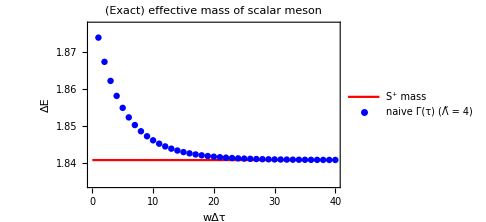

```mathematica
plotE2 = Show[gapE2Plot,
effMassE2Plot,
 PlotRange -> {{0, ntstepsE2}, {Min[effMassE2]-botPaddingE2 * rangeE2,Max[effMassE2]+topPaddingE2* rangeE2}},
PlotLabel->Style["(Exact) effective mass of scalar meson", Black, FontSize->14],
Frame->True,
FrameLabel->{Style["wΔτ",Black, FontSize-> 20],
Style["ΔE",Black, FontSize-> 20],None,None},
FrameTicksStyle->{Directive[Black, 15], Directive[Black, 15]},
FrameStyle->Directive[Black, 15, Thickness[0.002]],
ImageSize->Medium]
```

```mathematica
(*Export["~/Desktop/E2_gap_exact.png", plotE2, ImageResolution->500]*)
```

Different-Parity Gap

### Plot settings

```mathematica
ntstepsE1 = T;
tlistE1 = Table[t0 i, {i, 0, ntstepsE1}];
topPaddingE1 = 0.10;
botPaddingE1 = 0.10;
```

```mathematica
eOddPCoeffs⟦3⟧⟦1;;6⟧
```

{-0.243697,-0.748745,0.31963,0.391457,-0.19784,0.186884}

```mathematica
eOddPCoeffs⟦1⟧⟦1;;6⟧
```

{0.703071,-0.335893,-0.525354,0.287616,0.120278,-0.0896495}

```mathematica
eOddPCoeffs⟦1⟧
```

{0.703071,-0.335893,-0.525354,0.287616,0.120278,-0.0896495,-0.0703811,-0.0543489,-0.0543489,0.0279714}

### Overlaps

#### Naive Operators

```mathematica
Block[{M01SrcOvlapsGS, M01SrcOvlapsEOddP, M01SrcOvlapsEEvenP}, 
Print[M01SrcOvlapsGS = Total[M01SrcOnGS].Total[gs]//.rules];
Print[M01SrcOvlapsEEvenP = Table[Total[M01SrcOnGS].Total[estate]//.rules, {estate, eEvenP}]];
Print[M01SrcOvlapsEOddP = Table[Total[M01SrcOnGS].Total[estate]//.rules, {estate, eOddP}]];
M01SrcOvlaps = Join[{M01SrcOvlapsGS},M01SrcOvlapsEEvenP,M01SrcOvlapsEOddP]];
```

-8.67362×10^-19

{-8.67362×10^-18,-3.46945×10^-18,-7.80626×10^-18,0.,8.67362×10^-18,-3.46945×10^-18,1.73472×10^-18,1.21431×10^-17,0.,6.93889×10^-18,3.46945×10^-18,-3.46945×10^-18}

{-0.629024,0.0809064,-0.0195659,0.0526136,0.00612385,-0.0011985,2.1684×10^-17,6.97667×10^-6,0.00046771,0.0013491}

```mathematica
Block[{M01SnkOvlapsGS, M01SnkOvlapsEOddP, M01SnkOvlapsEEvenP}, 
Print[M01SnkOvlapsGS = Total[M01SnkOnGS].Total[gs]//.rules];
Print[M01SnkOvlapsEEvenP = Table[Total[M01SnkOnGS].Total[estate]//.rules, {estate, eEvenP}]];
Print[M01SnkOvlapsEOddP = Table[Total[M01SnkOnGS].Total[estate]//.rules, {estate, eOddP}]];
M01SnkOvlaps = Join[{M01SnkOvlapsGS},M01SnkOvlapsEEvenP,M01SnkOvlapsEOddP]];
```

-6.92026×10^-18

{1.72795×10^-17,6.99988×10^-18,8.78204×10^-18,0.,8.13152×10^-20,3.55076×10^-18,1.73472×10^-18,0.,0.,3.60497×10^-18,1.84314×10^-18,-1.76183×10^-18}

{-0.629024,0.0809064,-0.0195659,0.0526136,0.00612385,-0.0011985,2.1684×10^-17,6.97667×10^-6,0.00046771,0.0013491}

```mathematica
Block[{M01SrcBadOvlapsGS, M01SrcBadOvlapsEOddP, M01SrcBadOvlapsEEvenP}, 
Print[M01SrcBadOvlapsGS = Total[M01SrcBadOnGS].Total[gs]//.rules];
Print[M01SrcBadOvlapsEEvenP = Table[Total[M01SrcBadOnGS].Total[estate]//.rules, {estate, eEvenP}]];
Print[M01SrcBadOvlapsEOddP = Table[Total[M01SrcBadOnGS].Total[estate]//.rules, {estate, eOddP}]];
M01SrcBadOvlaps = Join[{M01SrcBadOvlapsGS},M01SrcBadOvlapsEEvenP,M01SrcBadOvlapsEOddP]];
```

-4.59431×10^-17

{0.328857,0.0833721,-0.0768779,1.38778×10^-17,0.0292634,-0.0473375,0.0074746,0.00235602,-3.33934×10^-17,-0.000513218,0.0013649,-0.00173795}

{-0.284689,0.0104849,-0.00308697,0.00184615,-0.0012934,0.00216503,3.77302×10^-17,0.000744519,0.000304028,0.0021039}

```mathematica
Block[{M01SnkBadOvlapsGS, M01SnkBadOvlapsEOddP, M01SnkBadOvlapsEEvenP}, 
Print[M01SnkBadOvlapsGS = Total[M01SnkBadOnGS].Total[gs]//.rules];
Print[M01SnkBadOvlapsEEvenP = Table[Total[M01SnkBadOnGS].Total[estate]//.rules, {estate, eEvenP}]];
Print[M01SnkBadOvlapsEOddP = Table[Total[M01SnkBadOnGS].Total[estate]//.rules, {estate, eOddP}]];
M01SnkBadOvlaps = Join[{M01SnkBadOvlapsGS},M01SnkBadOvlapsEEvenP,M01SnkBadOvlapsEOddP]];
```

-1.77809×10^-17

{-0.328857,-0.0833721,0.0768779,0.,-0.0292634,0.0473375,-0.0074746,-0.00235602,3.33934×10^-17,0.000513218,-0.0013649,0.00173795}

{0.284689,-0.0104849,0.00308697,-0.00184615,0.0012934,-0.00216503,-3.81639×10^-17,-0.000744519,-0.000304028,-0.0021039}

#### Smart Operators

```mathematica
SmartOpSrcOvlapsGS = Total[smartOpSrcOnGS].Total[gs]//.rules
```

Total::normal: Nonatomic expression expected at position 1 in Total[0].

0.671533 Total[0].0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0+0.0158471 ((Total[0].1,0,1,0,1,0,1,0,0,-1,0,-1,0,-1,0,-1)/(√2)+(Total[0].1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0)/(√2))+0.0117709 ((Total[0].0,0,0,1,1,0,1,1,0,-1,-1,-1,0,-1,0,0)/(2 √2)+(Total[0].0,0,0,1,1,0,1,1,1,0,0,0,1,0,1,1)/(2 √2)+(Total[0].0,1,1,0,1,1,0,0,-1,-1,0,-1,0,0,0,-1)/(2 √2)+(Total[0].0,1,1,0,1,1,0,0,0,0,1,0,1,1,1,0)/(2 √2)+(Total[0].1,0,1,1,0,0,0,1,0,-1,0,0,0,-1,-1,-1)/(2 √2)+(Total[0].1,0,1,1,0,0,0,1,1,0,1,1,1,0,0,0)/(2 √2)+(Total[0].1,1,0,0,0,1,1,0,0,0,0,-1,-1,-1,0,-1)/(2 √2)+(Total[0].1,1,0,0,0,1,1,0,1,1,1,0,0,0,1,0)/(2 √2))+0.0117709 ((Total[0].0,0,1,0,0,1,1,1,0,-1,0,-1,-1,-1,0,0)/(2 √2)+(Total[0].0,0,1,0,0,1,1,1,1,0,1,0,0,0,1,1)/(2 √2)+(Total[0].0,1,1,1,0,0,1,0,-1,-1,0,0,0,-1,0,-1)/(2 √2)+(Total[0].0,1,1,1,0,0,1,0,0,0,1,1,1,0,1,0)/(2 √2)+(Total[0].1,0,0,1,1,1,0,0,0,-1,-1,-1,0,0,0,-1)/(2 √2)+(Total[0].1,0,0,1,1,1,0,0,1,0,0,0,1,1,1,0)/(2 √2)+(Total[0].1,1,0,0,1,0,0,1,0,0,0,-1,0,-1,-1,-1)/(2 √2)+(Total[0].1,1,0,0,1,0,0,1,1,1,1,0,1,0,0,0)/(2 √2))-0.0848005 ((Total[0].0,0,1,0,1,0,1,1,0,-1,0,-1,0,-1,0,0)/(2 √2)+(Total[0].0,1,1,0,1,0,1,0,0,0,1,0,1,0,1,0)/(2 √2)+(Total[0].1,0,0,1,1,0,1,0,1,0,0,0,1,0,1,0)/(2 √2)+(Total[0].1,0,1,0,0,1,1,0,1,0,1,0,0,0,1,0)/(2 √2)+(Total[0].1,0,1,0,1,0,0,1,1,0,1,0,1,0,0,0)/(2 √2)+(Total[0].1,0,1,0,1,1,0,0,0,-1,0,-1,0,0,0,-1)/(2 √2)+(Total[0].1,0,1,1,0,0,1,0,0,-1,0,0,0,-1,0,-1)/(2 √2)+(Total[0].1,1,0,0,1,0,1,0,0,0,0,-1,0,-1,0,-1)/(2 √2))+0.153118 (1/2 Total[0].0,0,1,1,0,0,1,1,0,-1,0,0,0,-1,0,0+1/2 Total[0].0,1,1,0,0,1,1,0,0,0,1,0,0,0,1,0+1/2 Total[0].1,0,0,1,1,0,0,1,1,0,0,0,1,0,0,0+1/2 Total[0].1,1,0,0,1,1,0,0,0,0,0,-1,0,0,0,-1)-0.0333133 ((Total[0].0,0,0,1,0,1,1,1,1,0,0,0,0,0,1,1)/(2 √2)+(Total[0].0,0,0,1,1,1,0,1,0,-1,-1,-1,0,0,0,0)/(2 √2)+(Total[0].0,1,0,0,0,1,1,1,0,0,0,-1,-1,-1,0,0)/(2 √2)+(Total[0].0,1,0,1,1,1,0,0,0,0,0,0,1,1,1,0)/(2 √2)+(Total[0].0,1,1,1,0,0,0,1,0,0,1,1,1,0,0,0)/(2 √2)+(Total[0].0,1,1,1,0,1,0,0,-1,-1,0,0,0,0,0,-1)/(2 √2)+(Total[0].1,1,0,0,0,1,0,1,1,1,1,0,0,0,0,0)/(2 √2)+(Total[0].1,1,0,1,0,0,0,1,0,0,0,0,0,-1,-1,-1)/(2 √2))+0.233051 ((Total[0].0,0,1,0,1,1,0,1,0,-1,0,-1,0,0,0,0)/(2 √2)+(Total[0].0,1,0,0,1,0,1,1,0,0,0,-1,0,-1,0,0)/(2 √2)+(Total[0].0,1,0,1,1,0,1,0,0,0,0,0,1,0,1,0)/(2 √2)+(Total[0].0,1,1,0,1,0,0,1,0,0,1,0,1,0,0,0)/(2 √2)+(Total[0].1,0,0,1,0,1,1,0,1,0,0,0,0,0,1,0)/(2 √2)+(Total[0].1,0,1,0,0,1,0,1,1,0,1,0,0,0,0,0)/(2 √2)+(Total[0].1,0,1,1,0,1,0,0,0,-1,0,0,0,0,0,-1)/(2 √2)+(Total[0].1,1,0,1,0,0,1,0,0,0,0,0,0,-1,0,-1)/(2 √2))-0.640649 ((Total[0].0,0,1,1,0,1,0,1,0,-1,0,0,0,0,0,0)/(2 √2)+(Total[0].0,1,0,0,1,1,0,1,0,0,0,-1,0,0,0,0)/(2 √2)+(Total[0].0,1,0,1,0,0,1,1,0,0,0,0,0,-1,0,0)/(2 √2)+(Total[0].0,1,0,1,0,1,1,0,0,0,0,0,0,0,1,0)/(2 √2)+(Total[0].0,1,0,1,1,0,0,1,0,0,0,0,1,0,0,0)/(2 √2)+(Total[0].0,1,1,0,0,1,0,1,0,0,1,0,0,0,0,0)/(2 √2)+(Total[0].1,0,0,1,0,1,0,1,1,0,0,0,0,0,0,0)/(2 √2)+(Total[0].1,1,0,1,0,1,0,0,0,0,0,0,0,0,0,-1)/(2 √2))+0.151536 (1/2 Total[0].0,0,1,1,0,1,1,0,0,-1,0,0,0,0,1,0+1/2 Total[0].0,1,1,0,0,0,1,1,0,0,1,0,0,-1,0,0+1/2 Total[0].1,0,0,0,1,1,0,1,1,0,0,-1,0,0,0,0+1/2 Total[0].1,1,0,1,1,0,0,0,0,0,0,0,1,0,0,-1)+0.151536 (1/2 Total[0].0,0,1,1,1,0,0,1,0,-1,0,0,1,0,0,0+1/2 Total[0].0,1,0,0,1,1,1,0,0,0,0,-1,0,0,1,0+1/2 Total[0].1,0,0,1,0,0,1,1,1,0,0,0,0,-1,0,0+1/2 Total[0].1,1,1,0,0,1,0,0,0,0,1,0,0,0,0,-1)-0.077308 ((Total[0].0,0,1,0,1,1,1,0,0,-1,0,-1,0,0,1,0)/(2 √2)+(Total[0].0,0,1,1,1,0,1,0,0,-1,0,0,1,0,1,0)/(2 √2)+(Total[0].1,0,0,0,1,0,1,1,1,0,0,-1,0,-1,0,0)/(2 √2)+(Total[0].1,0,0,0,1,1,1,0,1,0,0,-1,0,0,1,0)/(2 √2)+(Total[0].1,0,1,0,0,0,1,1,1,0,1,0,0,-1,0,0)/(2 √2)+(Total[0].1,0,1,1,1,0,0,0,0,-1,0,0,1,0,0,-1)/(2 √2)+(Total[0].1,1,1,0,0,0,1,0,0,0,1,0,0,-1,0,-1)/(2 √2)+(Total[0].1,1,1,0,1,0,0,0,0,0,1,0,1,0,0,-1)/(2 √2))+0.0110243 ((Total[0].0,0,0,0,1,1,1,1,1,0,0,-1,0,0,1,1)/(2 √2)+(Total[0].0,0,0,1,1,1,1,0,0,-1,-1,-1,0,0,1,0)/(2 √2)+(Total[0].0,0,1,1,1,1,0,0,0,-1,0,0,1,1,1,0)/(2 √2)+(Total[0].0,1,1,1,1,0,0,0,-1,-1,0,0,1,0,0,-1)/(2 √2)+(Total[0].1,0,0,0,0,1,1,1,1,0,0,-1,-1,-1,0,0)/(2 √2)+(Total[0].1,1,0,0,0,0,1,1,1,1,1,0,0,-1,0,0)/(2 √2)+(Total[0].1,1,1,0,0,0,0,1,0,0,1,0,0,-1,-1,-1)/(2 √2)+(Total[0].1,1,1,1,0,0,0,0,0,0,1,1,1,0,0,-1)/(2 √2))

```mathematica
ctr=0;
SetSharedVariable[ctr];
Monitor[SmartOpSrcOvlapsEEvenP = ParallelTable[ctr++;Total[smartOpSrcOnGS].Total[estate]//.rules, {estate, eEvenP}],
ProgressIndicator[ctr, {1, Length[eEvenP]}]]
```

Total::normal: Nonatomic expression expected at position 1 in Total[0].

General::stop: Further output of Total::normal will be suppressed during this calculation.

Total::normal: Nonatomic expression expected at position 1 in Total[0].

General::stop: Further output of Total::normal will be suppressed during this calculation.

Total::normal: Nonatomic expression expected at position 1 in Total[0].

General::stop: Further output of Total::normal will be suppressed during this calculation.

Total::normal: Nonatomic expression expected at position 1 in Total[0].

General::stop: Further output of Total::normal will be suppressed during this calculation.

Total::normal: Nonatomic expression expected at position 1 in Total[0].

General::stop: Further output of Total::normal will be suppressed during this calculation.

{18+1-0.0606 ((Total[0].0,0,0,0,1,1,1,1,1,0,0,-1,0,0,1,1)/(2 √2)+(Total[0].0,0,0,1,1,1,1,0,0,-1,-1,-1,0,0,1,0)/(2 √2)+(Total[0].0,0,1,1,1,1,0,0,0,-1,0,0,1,1,1,0)/(2 √2)+(Total[0].0,1,1,1,1,0,0,0,-1,-1,0,0,1,0,0,-1)/(2 √2)+(Total[0].1)/(2 √2)+(Total[0].1,1,0,0,0,0,1,1,1,1,1,0,0,-1,0,0)/(2 √2)+(Total[0].1,1,1,0,0,0,0,1,0,0,1,0,0,-1,-1,-1)/(2 √2)+(Total[0].1,1,1,1,0,0,0,0,0,0,1,1,1,0,0,-1)/(2 √2)),1,1,0.707107 (1)-1,4,1,1,1,1}
 |  |  |  |

```mathematica
ctr=0;
SetSharedVariable[ctr];
Monitor[SmartOpSrcOvlapsEOddP = ParallelTable[ctr++;Total[smartOpSrcOnGS].Total[estate]//.rules, {estate, eOddP}],
ProgressIndicator[ctr, {1, Length[eOddP]}]]
```

Total::normal: Nonatomic expression expected at position 1 in Total[0].

General::stop: Further output of Total::normal will be suppressed during this calculation.

Total::normal: Nonatomic expression expected at position 1 in Total[0].

General::stop: Further output of Total::normal will be suppressed during this calculation.

{14+0.0279714 ((Total[0].0,0,0,0,1,1,1,1,1,0,0,-1,0,0,1,1)/(2 √2)-(Total[0].0,0,0,1,1,1,1,0,0,-1,-1,-1,0,0,1,0)/(2 √2)+(Total[0].0,0,1,1,1,1,0,0,0,-1,0,0,1,1,1,0)/(2 √2)-(Total[0].1)/(2 √2)-1/(2 √2)+(Total[0].1,1,0,0,0,0,1,1,1,1,1,0,0,-1,0,0)/(2 √2)-(Total[0].1,1,1,0,0,0,0,1,0,0,1,0,0,-1,-1,-1)/(2 √2)+(Total[0].1,1,1,1,0,0,0,0,0,0,1,1,1,0,0,-1)/(2 √2)),1,1,4,1,14+1,0.561682 ((Total[0].|1,0,12,0,-1⟩)/(√2)-(Total[0].|1⟩)/(√2))+11}
 |  |  |  |

```mathematica
SmartOpSrcOvlaps = Join[{SmartOpSrcOvlapsGS},SmartOpSrcOvlapsEEvenP,SmartOpSrcOvlapsEOddP]
```

{0.671533 Total[0].0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0+0.0158471 (1/(√2)+1)+14+0.0110243 ((Total[0].0,0,0,0,1,1,1,1,1,0,0,-1,0,0,1,1)/(2 √2)+(Total[0].0,0,0,1,1,1,1,0,0,-1,-1,-1,0,0,1,0)/(2 √2)+(Total[0].0,0,1,1,1,1,0,0,0,-1,0,0,1,1,1,0)/(2 √2)+(Total[0].0,1,1,1,1,0,0,0,-1,-1,0,0,1,0,0,-1)/(2 √2)+(Total[0].1)/(2 √2)+(Total[0].1,1,0,0,0,0,1,1,1,1,1,0,0,-1,0,0)/(2 √2)+(Total[0].1,1,1,0,0,0,0,1,0,0,1,0,0,-1,-1,-1)/(2 √2)+(Total[0].1,1,1,1,0,0,0,0,0,0,1,1,1,0,0,-1)/(2 √2)),21,1}
 |  |  |  |

```mathematica
SmartOpSnkOvlapsGS = Total[smartOpSnkOnGS].Total[gs]//.rules
```

Total::normal: Nonatomic expression expected at position 1 in Total[0].

0.671533 Total[0].0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0+0.0158471 ((Total[0].1,0,1,0,1,0,1,0,0,-1,0,-1,0,-1,0,-1)/(√2)+(Total[0].1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0)/(√2))+0.0117709 ((Total[0].0,0,0,1,1,0,1,1,0,-1,-1,-1,0,-1,0,0)/(2 √2)+(Total[0].0,0,0,1,1,0,1,1,1,0,0,0,1,0,1,1)/(2 √2)+(Total[0].0,1,1,0,1,1,0,0,-1,-1,0,-1,0,0,0,-1)/(2 √2)+(Total[0].0,1,1,0,1,1,0,0,0,0,1,0,1,1,1,0)/(2 √2)+(Total[0].1,0,1,1,0,0,0,1,0,-1,0,0,0,-1,-1,-1)/(2 √2)+(Total[0].1,0,1,1,0,0,0,1,1,0,1,1,1,0,0,0)/(2 √2)+(Total[0].1,1,0,0,0,1,1,0,0,0,0,-1,-1,-1,0,-1)/(2 √2)+(Total[0].1,1,0,0,0,1,1,0,1,1,1,0,0,0,1,0)/(2 √2))+0.0117709 ((Total[0].0,0,1,0,0,1,1,1,0,-1,0,-1,-1,-1,0,0)/(2 √2)+(Total[0].0,0,1,0,0,1,1,1,1,0,1,0,0,0,1,1)/(2 √2)+(Total[0].0,1,1,1,0,0,1,0,-1,-1,0,0,0,-1,0,-1)/(2 √2)+(Total[0].0,1,1,1,0,0,1,0,0,0,1,1,1,0,1,0)/(2 √2)+(Total[0].1,0,0,1,1,1,0,0,0,-1,-1,-1,0,0,0,-1)/(2 √2)+(Total[0].1,0,0,1,1,1,0,0,1,0,0,0,1,1,1,0)/(2 √2)+(Total[0].1,1,0,0,1,0,0,1,0,0,0,-1,0,-1,-1,-1)/(2 √2)+(Total[0].1,1,0,0,1,0,0,1,1,1,1,0,1,0,0,0)/(2 √2))-0.0848005 ((Total[0].0,0,1,0,1,0,1,1,0,-1,0,-1,0,-1,0,0)/(2 √2)+(Total[0].0,1,1,0,1,0,1,0,0,0,1,0,1,0,1,0)/(2 √2)+(Total[0].1,0,0,1,1,0,1,0,1,0,0,0,1,0,1,0)/(2 √2)+(Total[0].1,0,1,0,0,1,1,0,1,0,1,0,0,0,1,0)/(2 √2)+(Total[0].1,0,1,0,1,0,0,1,1,0,1,0,1,0,0,0)/(2 √2)+(Total[0].1,0,1,0,1,1,0,0,0,-1,0,-1,0,0,0,-1)/(2 √2)+(Total[0].1,0,1,1,0,0,1,0,0,-1,0,0,0,-1,0,-1)/(2 √2)+(Total[0].1,1,0,0,1,0,1,0,0,0,0,-1,0,-1,0,-1)/(2 √2))+0.153118 (1/2 Total[0].0,0,1,1,0,0,1,1,0,-1,0,0,0,-1,0,0+1/2 Total[0].0,1,1,0,0,1,1,0,0,0,1,0,0,0,1,0+1/2 Total[0].1,0,0,1,1,0,0,1,1,0,0,0,1,0,0,0+1/2 Total[0].1,1,0,0,1,1,0,0,0,0,0,-1,0,0,0,-1)-0.0333133 ((Total[0].0,0,0,1,0,1,1,1,1,0,0,0,0,0,1,1)/(2 √2)+(Total[0].0,0,0,1,1,1,0,1,0,-1,-1,-1,0,0,0,0)/(2 √2)+(Total[0].0,1,0,0,0,1,1,1,0,0,0,-1,-1,-1,0,0)/(2 √2)+(Total[0].0,1,0,1,1,1,0,0,0,0,0,0,1,1,1,0)/(2 √2)+(Total[0].0,1,1,1,0,0,0,1,0,0,1,1,1,0,0,0)/(2 √2)+(Total[0].0,1,1,1,0,1,0,0,-1,-1,0,0,0,0,0,-1)/(2 √2)+(Total[0].1,1,0,0,0,1,0,1,1,1,1,0,0,0,0,0)/(2 √2)+(Total[0].1,1,0,1,0,0,0,1,0,0,0,0,0,-1,-1,-1)/(2 √2))+0.233051 ((Total[0].0,0,1,0,1,1,0,1,0,-1,0,-1,0,0,0,0)/(2 √2)+(Total[0].0,1,0,0,1,0,1,1,0,0,0,-1,0,-1,0,0)/(2 √2)+(Total[0].0,1,0,1,1,0,1,0,0,0,0,0,1,0,1,0)/(2 √2)+(Total[0].0,1,1,0,1,0,0,1,0,0,1,0,1,0,0,0)/(2 √2)+(Total[0].1,0,0,1,0,1,1,0,1,0,0,0,0,0,1,0)/(2 √2)+(Total[0].1,0,1,0,0,1,0,1,1,0,1,0,0,0,0,0)/(2 √2)+(Total[0].1,0,1,1,0,1,0,0,0,-1,0,0,0,0,0,-1)/(2 √2)+(Total[0].1,1,0,1,0,0,1,0,0,0,0,0,0,-1,0,-1)/(2 √2))-0.640649 ((Total[0].0,0,1,1,0,1,0,1,0,-1,0,0,0,0,0,0)/(2 √2)+(Total[0].0,1,0,0,1,1,0,1,0,0,0,-1,0,0,0,0)/(2 √2)+(Total[0].0,1,0,1,0,0,1,1,0,0,0,0,0,-1,0,0)/(2 √2)+(Total[0].0,1,0,1,0,1,1,0,0,0,0,0,0,0,1,0)/(2 √2)+(Total[0].0,1,0,1,1,0,0,1,0,0,0,0,1,0,0,0)/(2 √2)+(Total[0].0,1,1,0,0,1,0,1,0,0,1,0,0,0,0,0)/(2 √2)+(Total[0].1,0,0,1,0,1,0,1,1,0,0,0,0,0,0,0)/(2 √2)+(Total[0].1,1,0,1,0,1,0,0,0,0,0,0,0,0,0,-1)/(2 √2))+0.151536 (1/2 Total[0].0,0,1,1,0,1,1,0,0,-1,0,0,0,0,1,0+1/2 Total[0].0,1,1,0,0,0,1,1,0,0,1,0,0,-1,0,0+1/2 Total[0].1,0,0,0,1,1,0,1,1,0,0,-1,0,0,0,0+1/2 Total[0].1,1,0,1,1,0,0,0,0,0,0,0,1,0,0,-1)+0.151536 (1/2 Total[0].0,0,1,1,1,0,0,1,0,-1,0,0,1,0,0,0+1/2 Total[0].0,1,0,0,1,1,1,0,0,0,0,-1,0,0,1,0+1/2 Total[0].1,0,0,1,0,0,1,1,1,0,0,0,0,-1,0,0+1/2 Total[0].1,1,1,0,0,1,0,0,0,0,1,0,0,0,0,-1)-0.077308 ((Total[0].0,0,1,0,1,1,1,0,0,-1,0,-1,0,0,1,0)/(2 √2)+(Total[0].0,0,1,1,1,0,1,0,0,-1,0,0,1,0,1,0)/(2 √2)+(Total[0].1,0,0,0,1,0,1,1,1,0,0,-1,0,-1,0,0)/(2 √2)+(Total[0].1,0,0,0,1,1,1,0,1,0,0,-1,0,0,1,0)/(2 √2)+(Total[0].1,0,1,0,0,0,1,1,1,0,1,0,0,-1,0,0)/(2 √2)+(Total[0].1,0,1,1,1,0,0,0,0,-1,0,0,1,0,0,-1)/(2 √2)+(Total[0].1,1,1,0,0,0,1,0,0,0,1,0,0,-1,0,-1)/(2 √2)+(Total[0].1,1,1,0,1,0,0,0,0,0,1,0,1,0,0,-1)/(2 √2))+0.0110243 ((Total[0].0,0,0,0,1,1,1,1,1,0,0,-1,0,0,1,1)/(2 √2)+(Total[0].0,0,0,1,1,1,1,0,0,-1,-1,-1,0,0,1,0)/(2 √2)+(Total[0].0,0,1,1,1,1,0,0,0,-1,0,0,1,1,1,0)/(2 √2)+(Total[0].0,1,1,1,1,0,0,0,-1,-1,0,0,1,0,0,-1)/(2 √2)+(Total[0].1,0,0,0,0,1,1,1,1,0,0,-1,-1,-1,0,0)/(2 √2)+(Total[0].1,1,0,0,0,0,1,1,1,1,1,0,0,-1,0,0)/(2 √2)+(Total[0].1,1,1,0,0,0,0,1,0,0,1,0,0,-1,-1,-1)/(2 √2)+(Total[0].1,1,1,1,0,0,0,0,0,0,1,1,1,0,0,-1)/(2 √2))

```mathematica
ctr=0;
SetSharedVariable[ctr];
Monitor[SmartOpSnkOvlapsEEvenP = ParallelTable[ctr++;Total[smartOpSnkOnGS].Total[estate]//.rules, {estate, eEvenP}],
ProgressIndicator[ctr, {1, Length[eEvenP]}]]
```

Total::normal: Nonatomic expression expected at position 1 in Total[0].

General::stop: Further output of Total::normal will be suppressed during this calculation.

Total::normal: Nonatomic expression expected at position 1 in Total[0].

General::stop: Further output of Total::normal will be suppressed during this calculation.

Total::normal: Nonatomic expression expected at position 1 in Total[0].

General::stop: Further output of Total::normal will be suppressed during this calculation.

Total::normal: Nonatomic expression expected at position 1 in Total[0].

General::stop: Further output of Total::normal will be suppressed during this calculation.

{18+1-0.0606 ((Total[0].0,0,0,0,1,1,1,1,1,0,0,-1,0,0,1,1)/(2 √2)+(Total[0].0,0,0,1,1,1,1,0,0,-1,-1,-1,0,0,1,0)/(2 √2)+(Total[0].0,0,1,1,1,1,0,0,0,-1,0,0,1,1,1,0)/(2 √2)+(Total[0].0,1,1,1,1,0,0,0,-1,-1,0,0,1,0,0,-1)/(2 √2)+(Total[0].1)/(2 √2)+(Total[0].1,1,0,0,0,0,1,1,1,1,1,0,0,-1,0,0)/(2 √2)+(Total[0].1,1,1,0,0,0,0,1,0,0,1,0,0,-1,-1,-1)/(2 √2)+(Total[0].1,1,1,1,0,0,0,0,0,0,1,1,1,0,0,-1)/(2 √2)),1,1,0.707107 (1)-1,4,1,1,1,1}
 |  |  |  |

```mathematica
ctr=0;
SetSharedVariable[ctr];
Monitor[SmartOpSnkOvlapsEOddP = ParallelTable[ctr++;Total[smartOpSnkOnGS].Total[estate]//.rules, {estate, eOddP}],
ProgressIndicator[ctr, {1, Length[eOddP]}]]
```

Total::normal: Nonatomic expression expected at position 1 in Total[0].

General::stop: Further output of Total::normal will be suppressed during this calculation.

Total::normal: Nonatomic expression expected at position 1 in Total[0].

General::stop: Further output of Total::normal will be suppressed during this calculation.

```mathematica
SmartOpSnkOvlaps = Join[{SmartOpSnkOvlapsGS},SmartOpSnkOvlapsEEvenP,SmartOpSnkOvlapsEOddP]
```

{-0.820795 Total[0].0,1,0,1,0,0,0,0-0.146043 ((Total[0].1,0,1,0,0,-1,0,-1)/(√2)+(Total[0].1,0,1,0,1,0,1,0)/(√2))+0.552238 (1/2 Total[0].0,0,1,1,0,-1,0,0+1/2 Total[0].0,1,1,0,0,0,1,0+1/2 Total[0].1,0,0,1,1,0,0,0+1/2 Total[0].1,1,0,0,0,0,0,-1),-0.527792 Total[0].0,1,0,1,0,0,0,0+0.563651 ((Total[0].1,0,1,0,0,-1,0,-1)/(√2)+(Total[0].1,0,1,0,1,0,1,0)/(√2))-0.6354 (1/2 Total[0].0,0,1,1,0,-1,0,0+1/2 Total[0].0,1,1,0,0,0,1,0+1/2 Total[0].1,0,0,1,1,0,0,0+1/2 Total[0].1,1,0,0,0,0,0,-1),0.218474 Total[0].0,1,0,1,0,0,0,0+0.813 ((Total[0].1,0,1,0,0,-1,0,-1)/(√2)+(Total[0].1,0,1,0,1,0,1,0)/(√2))+0.539723 (1/2 Total[0].0,0,1,1,0,-1,0,0+1/2 Total[0].0,1,1,0,0,0,1,0+1/2 Total[0].1,0,0,1,1,0,0,0+1/2 Total[0].1,1,0,0,0,0,0,-1),0.459596 ((Total[0].1,0,1,0,0,-1,0,-1)/(√2)-(Total[0].1,0,1,0,1,0,1,0)/(√2))-0.888128 (1/2 Total[0].0,0,1,1,0,-1,0,0-1/2 Total[0].0,1,1,0,0,0,1,0-1/2 Total[0].1,0,0,1,1,0,0,0+1/2 Total[0].1,1,0,0,0,0,0,-1),0.888128 ((Total[0].1,0,1,0,0,-1,0,-1)/(√2)-(Total[0].1,0,1,0,1,0,1,0)/(√2))+0.459596 (1/2 Total[0].0,0,1,1,0,-1,0,0-1/2 Total[0].0,1,1,0,0,0,1,0-1/2 Total[0].1,0,0,1,1,0,0,0+1/2 Total[0].1,1,0,0,0,0,0,-1)}

### Effective mass and exact gap

```mathematica
dataE1Naive =Table[g[M01SrcOvlaps,M01SnkOvlaps, energiesParitySorted, t, T], {t, tlistE1}];
dataE1Bad =Table[g[M01SrcBadOvlaps,M01SnkBadOvlaps, energiesParitySorted, t, T], {t, tlistE1}];
dataE1Smart =Table[g[SmartOpSrcOvlaps,SmartOpSnkOvlaps, energiesParitySorted, t, T], {t, tlistE1}];
```

```mathematica
tlistE1
```

{0.,0.2,0.4,0.6,0.8,1.,1.2,1.4,1.6,1.8,2.,2.2,2.4,2.6,2.8,3.,3.2,3.4,3.6,3.8,4.,4.2,4.4,4.6,4.8,5.,5.2,5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.}

```mathematica
gapE1 = evaluesOddPShifted⟦1⟧ - evaluesEvenPShifted⟦1⟧;
effMassE1Naive = Log[Drop[dataE1Naive, -1]/ Drop[dataE1Naive, 1]]/t0;
effMassE1Bad = Log[Drop[dataE1Bad, -1]/ Drop[dataE1Bad, 1]]/t0;
effMassE1Smart = Log[Drop[dataE1Smart, -1]/ Drop[dataE1Smart, 1]]/t0;
```

```mathematica
effMassE1Max=Max[Max[effMassE1Naive],Max[effMassE1Smart]];
effMassE1Min = Min[Min[effMassE1Naive], Min[effMassE1Smart]];
rangeE1 =effMassE1Max - effMassE1Min;
```

```mathematica
effMassE1Naive
```

{1.30809,1.30789,1.30774,1.30764,1.30756,1.30751,1.30748,1.30745,1.30743,1.30742,1.30741,1.3074,1.3074,1.3074,1.30739,1.30739,1.30739,1.30739,1.30739,1.30739,1.30739,1.30739,1.30739,1.30739,1.30739,1.30739,1.30739,1.30739,1.30739,1.30739,1.30739,1.30739,1.30739,1.30739,1.30739,1.30739,1.30739,1.30739,1.30739,1.30739}

#### Save data to file for combined plot with MC data

```mathematica
(*Block[{tsteps, dataForCombinedPlot},
(* in Monte-Carlo with checkerboard splitting, two timesteps go for one *)
tsteps=Table[2*i, {i, 0, Length[effMassE1Naive]-1}];
dataForCombinedPlot = Transpose[{effMassE1Naive, tsteps}];
Export["E1_gap_exact_naive.txt", SetPrecision[dataForCombinedPlot, 30], "Table"]];*)
```

### Plots

Make one plot with, and one plot without the “bad” operator

```mathematica
gapE1Plot = Plot[gapE1, {x,0, ntstepsE1}, PlotStyle->Red,  PlotLegends->{"V^- mass"},LabelStyle->{FontSize->  14}];
effMassE1NaivePlot= ListPlot[effMassE1Naive,   
PlotLegends->{StringForm["naive Γ(τ)\n(Λ̃ = `1`)", Λ2]}, 
PlotStyle->Blue, LabelStyle->{FontSize->  14}];
effMassE1BadPlot= ListPlot[effMassE1Bad,   
PlotLegends->{StringForm["bad Γ(τ)\n(Λ̃ = `1`)", Λ2]}, 
PlotStyle->Orange, LabelStyle->{FontSize->  14}];
effMassE1SmartPlot= ListPlot[effMassE1Smart,  
 PlotLegends->{StringForm["smart Γ(τ)\n(Λ̃ = `1`)", Λ3]}, 
PlotStyle->Black, LabelStyle->{FontSize->  14}];
```

Total::normal: Nonatomic expression expected at position 1 in Total[0.].

General::stop: Further output of Total::normal will be suppressed during this calculation.

```mathematica
plotE1withoutBad= Show[gapE1Plot,effMassE1NaivePlot, effMassE1SmartPlot,
 PlotRange -> {{0, ntstepsE1}, {effMassE1Min-botPaddingE1 * rangeE1,effMassE1Max+topPaddingE1* rangeE1}},
PlotLabel->Style["(Exact) effective mass of vector meson", Black, FontSize->17],
Frame->True,
FrameLabel->{Style["wΔτ",Black, FontSize-> 20],
Style["ΔE",Black, FontSize-> 20],None,None},
FrameTicksStyle->{Directive[Black, 15], Directive[Black, 15]},
FrameStyle->Directive[Black, 15, Thickness[0.002]],
ImageSize->Medium]
```

-Graphics-

```mathematica
effMassE1Max=Max[Max[effMassE1Naive],Max[effMassE1Smart], Max[effMassE1Bad]];
effMassE1Min = Min[Min[effMassE1Naive], Min[effMassE1Smart],  Min[effMassE1Bad]];
rangeE1 =effMassE1Max - effMassE1Min;
plotE1withBad= Show[gapE1Plot,effMassE1NaivePlot,effMassE1BadPlot, effMassE1SmartPlot,
 PlotRange -> {{0, ntstepsE1}, {effMassE1Min-botPaddingE1 * rangeE1,effMassE1Max+topPaddingE1* rangeE1}},
PlotLabel->Style["(Exact) effective mass of vector meson", Black, FontSize->17],
Frame->True,
FrameLabel->{Style["wΔτ",Black, FontSize-> 20],
Style["ΔE",Black, FontSize-> 20],None,None},
FrameTicksStyle->{Directive[Black, 15], Directive[Black, 15]},
FrameStyle->Directive[Black, 15, Thickness[0.002]],
ImageSize->Medium]
```

-Graphics-

```mathematica
(*Export["~/Desktop/E1_gap_T3.png", plotE1withoutBad, ImageResolution->500]*)
```

```mathematica
(*Export["~/Desktop/E1_gap_exact_2_L2_3_L3_3.png", plotE1withBad, ImageResolution->500]*)
```

```mathematica
b
```

b